## 2^6 Model

### Initialization

```mathematica
(* Fourth Root of Unity *)
om=Exp[2*Pi*I/4]
```

ⅈ

```mathematica
(* Multi-vector Brane and Cycle Enumeration Indices for Overlap function *)
lvec[idx_]:=Rest@IntegerDigits[3^(6)+idx-1,3]+1
nvec[idx_]:=Rest@IntegerDigits[3^(6)+idx-1,3]
```

```mathematica
sets=1+Select[nvec[#]&/@Range[3^6],Mod[Total[#],4]==0&];
```

```mathematica
H30=Select[sets,Total[#]==6&]
H21=Select[sets,Total[#]==10&]
H12=Select[sets,Total[#]==14&]
H03=Select[sets,Total[#]==18&]
```

{{1,1,1,1,1,1}}

{{1,1,1,1,3,3},{1,1,1,2,2,3},{1,1,1,2,3,2},{1,1,1,3,1,3},{1,1,1,3,2,2},{1,1,1,3,3,1},{1,1,2,1,2,3},{1,1,2,1,3,2},{1,1,2,2,1,3},{1,1,2,2,2,2},{1,1,2,2,3,1},{1,1,2,3,1,2},{1,1,2,3,2,1},{1,1,3,1,1,3},{1,1,3,1,2,2},{1,1,3,1,3,1},{1,1,3,2,1,2},{1,1,3,2,2,1},{1,1,3,3,1,1},{1,2,1,1,2,3},{1,2,1,1,3,2},{1,2,1,2,1,3},{1,2,1,2,2,2},{1,2,1,2,3,1},{1,2,1,3,1,2},{1,2,1,3,2,1},{1,2,2,1,1,3},{1,2,2,1,2,2},{1,2,2,1,3,1},{1,2,2,2,1,2},{1,2,2,2,2,1},{1,2,2,3,1,1},{1,2,3,1,1,2},{1,2,3,1,2,1},{1,2,3,2,1,1},{1,3,1,1,1,3},{1,3,1,1,2,2},{1,3,1,1,3,1},{1,3,1,2,1,2},{1,3,1,2,2,1},{1,3,1,3,1,1},{1,3,2,1,1,2},{1,3,2,1,2,1},{1,3,2,2,1,1},{1,3,3,1,1,1},{2,1,1,1,2,3},{2,1,1,1,3,2},{2,1,1,2,1,3},{2,1,1,2,2,2},{2,1,1,2,3,1},{2,1,1,3,1,2},{2,1,1,3,2,1},{2,1,2,1,1,3},{2,1,2,1,2,2},{2,1,2,1,3,1},{2,1,2,2,1,2},{2,1,2,2,2,1},{2,1,2,3,1,1},{2,1,3,1,1,2},{2,1,3,1,2,1},{2,1,3,2,1,1},{2,2,1,1,1,3},{2,2,1,1,2,2},{2,2,1,1,3,1},{2,2,1,2,1,2},{2,2,1,2,2,1},{2,2,1,3,1,1},{2,2,2,1,1,2},{2,2,2,1,2,1},{2,2,2,2,1,1},{2,2,3,1,1,1},{2,3,1,1,1,2},{2,3,1,1,2,1},{2,3,1,2,1,1},{2,3,2,1,1,1},{3,1,1,1,1,3},{3,1,1,1,2,2},{3,1,1,1,3,1},{3,1,1,2,1,2},{3,1,1,2,2,1},{3,1,1,3,1,1},{3,1,2,1,1,2},{3,1,2,1,2,1},{3,1,2,2,1,1},{3,1,3,1,1,1},{3,2,1,1,1,2},{3,2,1,1,2,1},{3,2,1,2,1,1},{3,2,2,1,1,1},{3,3,1,1,1,1}}

{{1,1,3,3,3,3},{1,2,2,3,3,3},{1,2,3,2,3,3},{1,2,3,3,2,3},{1,2,3,3,3,2},{1,3,1,3,3,3},{1,3,2,2,3,3},{1,3,2,3,2,3},{1,3,2,3,3,2},{1,3,3,1,3,3},{1,3,3,2,2,3},{1,3,3,2,3,2},{1,3,3,3,1,3},{1,3,3,3,2,2},{1,3,3,3,3,1},{2,1,2,3,3,3},{2,1,3,2,3,3},{2,1,3,3,2,3},{2,1,3,3,3,2},{2,2,1,3,3,3},{2,2,2,2,3,3},{2,2,2,3,2,3},{2,2,2,3,3,2},{2,2,3,1,3,3},{2,2,3,2,2,3},{2,2,3,2,3,2},{2,2,3,3,1,3},{2,2,3,3,2,2},{2,2,3,3,3,1},{2,3,1,2,3,3},{2,3,1,3,2,3},{2,3,1,3,3,2},{2,3,2,1,3,3},{2,3,2,2,2,3},{2,3,2,2,3,2},{2,3,2,3,1,3},{2,3,2,3,2,2},{2,3,2,3,3,1},{2,3,3,1,2,3},{2,3,3,1,3,2},{2,3,3,2,1,3},{2,3,3,2,2,2},{2,3,3,2,3,1},{2,3,3,3,1,2},{2,3,3,3,2,1},{3,1,1,3,3,3},{3,1,2,2,3,3},{3,1,2,3,2,3},{3,1,2,3,3,2},{3,1,3,1,3,3},{3,1,3,2,2,3},{3,1,3,2,3,2},{3,1,3,3,1,3},{3,1,3,3,2,2},{3,1,3,3,3,1},{3,2,1,2,3,3},{3,2,1,3,2,3},{3,2,1,3,3,2},{3,2,2,1,3,3},{3,2,2,2,2,3},{3,2,2,2,3,2},{3,2,2,3,1,3},{3,2,2,3,2,2},{3,2,2,3,3,1},{3,2,3,1,2,3},{3,2,3,1,3,2},{3,2,3,2,1,3},{3,2,3,2,2,2},{3,2,3,2,3,1},{3,2,3,3,1,2},{3,2,3,3,2,1},{3,3,1,1,3,3},{3,3,1,2,2,3},{3,3,1,2,3,2},{3,3,1,3,1,3},{3,3,1,3,2,2},{3,3,1,3,3,1},{3,3,2,1,2,3},{3,3,2,1,3,2},{3,3,2,2,1,3},{3,3,2,2,2,2},{3,3,2,2,3,1},{3,3,2,3,1,2},{3,3,2,3,2,1},{3,3,3,1,1,3},{3,3,3,1,2,2},{3,3,3,1,3,1},{3,3,3,2,1,2},{3,3,3,2,2,1},{3,3,3,3,1,1}}

{{3,3,3,3,3,3}}

```mathematica
HAdS=Join[H21,H03];
```

```mathematica
(* Enumerated "alphabetical" order of Cycles *)
(*     Note: other choices exist to create a linearly independent basis for the intersection matrix. 
    This one was chosen to be consistent with arXiv:hep-th/0611001 *)
intBasis=nvec[#]&/@Range[2Length[HAdS]];
```

```mathematica
intBasis[[1]]
intBasis[[-1]]
```

{0,0,0,0,0,0}

{0,2,0,2,0,1}

```mathematica
(*conH21=Reverse[H12];
conH03=H30;
conHAdS=Join[conH21,conH03];*)
```

### Intersection Matrix

#### Initialization

```mathematica
(Imat=Table[ComplexExpand[Sum[(1-om^l)om^(n*l)Conjugate[(1-om^l)om^(m*l)]/(4(1-om^l)),{l,1,3}]],{n,0,3},{m,0,3}])//MatrixForm
```

(1 | 0 | 0 | -1
-1 | 1 | 0 | 0
0 | -1 | 1 | 0
0 | 0 | -1 | 1)

```mathematica
Imat=Imat[[;;3,;;3]];
```

```mathematica
(Acyc={{0,0,-1},{1,0,-1},{0,1,-1}})//MatrixForm
```

(0 | 0 | -1
1 | 0 | -1
0 | 1 | -1)

```mathematica
InterMat=Nest[KroneckerProduct[Imat,#]&,Imat,5]+Nest[KroneckerProduct[Imat,#]&,Imat,5].(-Nest[KroneckerProduct[Acyc,#]&,Acyc,5]+Nest[KroneckerProduct[Acyc,#]&,Acyc,5].Nest[KroneckerProduct[Acyc,#]&,Acyc,5]-Nest[KroneckerProduct[Acyc,#]&,Acyc,5].Nest[KroneckerProduct[Acyc,#]&,Acyc,5].Nest[KroneckerProduct[Acyc,#]&,Acyc,5]);
```

```mathematica
rank=MatrixRank[InterMat]
```

182

```mathematica
InterMat=InterMat[[;;rank,;;rank]];
```

### Flux Quantized Basis

#### Solving for Flux Coefficients A_(l⃗)(Skip unless this is the first time running or if you want to check something)

```mathematica
(* Subscript[N, m] - τ Subscript[M, m] *)
xvec={x[2#-1]-om x[2#]}&/@Range[rank];
(* Redefined Subscript[N, m] - τ Subscript[M, m], since we have an underdetermined system of equations (i.e. Length[xvec]=364 while Length[eqs]=182) 
  only half of xvec will be independent. So we define a new set of integer labeled variables called yvec *)
yvec={y[#]}&/@Range[rank];
(* Flux Coefficient variables *)
Avec={A[#]}&/@Range[Length[HAdS]];
```

```mathematica
(* Flux factors which multiply each coefficient Subscript[A, l] and come from integrating the harmonic forms, Subscript[χ, l], over the Integral Basis of cycles, Subscript[Γ, n] *)
Abasis=Table[(Times@@(1-om^HAdS[[jj]]))om^(intBasis[[ii]].HAdS[[jj]]),{ii,rank},{jj,Length[HAdS]}];
```

```mathematica
(* Construct the systems of linear equations from the Dirac flux quantization condition *)
Aeqs=Abasis.Avec;
quant=InterMat.xvec;
eqs=Thread[Flatten@Aeqs==Flatten@quant];
```

```mathematica
(* Constrain the Quantization Condition variables xvec to be integer valued. *)
xcons=Thread[Element[Variables[xvec],Integers]];
vars=Flatten[Avec];
```

```mathematica
(* Solving the system of linear equations, Σ_l Subscript[A, l](1-ω^l)ω^(n.l) = Subscript[N, n] - Subscript[τM, n], for Subscript[A, l] *)
sols=Solve[Flatten[{eqs,xcons}],vars];
```

```mathematica
AA=ComplexExpand[Avec/.sols[[1]]];
```

```mathematica
(* Apply the variable redefinition, yvec, to the remaining set of independent xvec in numerically increasing order. *)
redef=Thread[Variables[AA[[;;,1,1]]]->Flatten@yvec];
AASols=AA[[;;,1,1]]/.redef;
```

```mathematica
(* Separate each Complex valued coefficient Subscript[A, l] into its respective real and imaginary parts. *)
AAReIm=Flatten[{ComplexExpand[1/2(Conjugate[#]+#)/. Conjugate[y[o_]]->y[o]], ComplexExpand[1/(2I)(-Conjugate[#]+#)/. Conjugate[y[o_]]->y[o]]}&/@AASols,1];
```

```mathematica
(* Number of independent variables each flux coefficient depends on *)
Sort[Length/@AAReIm]
```

{27,27,27,27,27,27,27,27,30,30,30,30,33,33,36,36,36,36,37,37,38,38,42,42,42,42,42,42,45,45,46,46,46,46,46,46,46,46,47,47,48,48,48,48,51,51,51,51,54,54,54,54,58,58,59,59,59,59,60,60,60,60,60,60,60,60,60,60,61,61,62,62,62,62,64,64,64,64,66,66,66,66,66,66,68,68,68,68,69,69,69,69,69,69,69,69,69,69,70,70,70,70,71,71,72,72,72,72,73,73,73,73,73,73,73,73,74,74,78,78,79,79,81,81,82,82,82,82,89,89,89,89,91,91,94,94,97,97,97,97,101,101,103,103,103,103,105,105,105,105,107,107,108,108,110,110,119,119,119,119,138,138,142,142,146,146,148,148,150,150,150,150,151,151,156,156,157,157,157,157,158,158}

```mathematica
(*InvInterMat=Inverse[InterMat];*)
```

```mathematica
(* The Diagonal Intersection Matrix which comes from the Homogeneous basis of cycles. *) 
(*     Note: This provides the correct normalization for maintaining flux quantization 
           and to obtain the Tadpole value from any configuration of fluxes. *)
diagInterMat=ComplexExpand[Transpose[Abasis].Inverse[InterMat].Conjugate[Abasis]];
```

```mathematica
(* Flux Tadpole Equation *) 
Tadpole=ComplexExpand[AASols.diagInterMat.ConjugateTranspose[{AASols}]/(2I)][[1]];
```

```mathematica
Export["Tadpole_AAReIm_DiagInterMat_Mink-AdS-Components.mx",{AAReIm,Tadpole,diagInterMat}]
```

Tadpole_AAReIm_DiagInterMat_Mink-AdS-Components.mx

```mathematica
(*Diagonal[diagInterMat]*)
```

{8192 ⅈ,16384 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,32768 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,32768 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,32768 ⅈ,16384 ⅈ,32768 ⅈ,32768 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,32768 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,32768 ⅈ,16384 ⅈ,32768 ⅈ,32768 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,32768 ⅈ,16384 ⅈ,32768 ⅈ,32768 ⅈ,16384 ⅈ,32768 ⅈ,32768 ⅈ,32768 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,8192 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,16384 ⅈ,8192 ⅈ,8192 ⅈ}

## Solutions to Tadpole Constraint

### Import and Initialize

```mathematica
{AAReIm,Tadpole,diagInterMat}=Import["Tadpole_AAReIm_DiagInterMat_Mink-AdS-Components.mx"];
```

```mathematica
AAeqs={AAReIm[[2#-1]],AAReIm[[2#]]}&/@Range[Floor[Length[AAReIm]/2]];
```

```mathematica
Avec={AAReIm[[2#-1]]+I AAReIm[[2#]]}&/@Range[Floor[Length[AAReIm]/2]];
```

```mathematica
yvars=Variables[AAeqs];
```

```mathematica
(* Use to print out the real and imaginary parts of all flux coefficients Subscript[A, l] *)
(*Do[Print["AA[["<>ToString[ii]<>"]]="AAReIm[[ii]]],{ii,Length@AAReIm}]*)
```

AA[[1]]= (-y[128]/128+y[129]/128+y[132]/128+y[133]/128+y[136]/128-y[137]/128+y[140]/128-y[141]/128-y[144]/128-y[145]/128+y[146]/128-y[147]/128-y[148]/128+y[149]/128-y[150]/128-y[151]/128-y[152]/128+y[153]/128-y[154]/128+y[155]/128+y[156]/128+y[157]/128-y[158]/128+y[159]/128+y[160]/128-y[161]/128+y[162]/128)

AA[[2]]= (-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128+y[138]/128+y[139]/128+y[142]/128-y[143]/128+y[145]/128+y[146]/128-y[147]/128+y[148]/128-y[149]/128-y[150]/128-y[151]/128+y[152]/128-y[153]/128-y[154]/128+y[155]/128-y[156]/128-y[157]/128-y[158]/128+y[159]/128-y[160]/128+y[161]/128+y[162]/128)

AA[[3]]= (-y[127]/128-y[130]/128+y[131]/128+y[133]/128+y[136]/128-y[137]/128-y[139]/128-y[142]/128+y[143]/128+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128+y[150]/128-y[151]/128+y[152]/128-y[153]/128-y[154]/128+y[155]/128-y[156]/128+y[157]/128-y[158]/128+y[159]/128+y[160]/128-y[161]/128+y[162]/128)

AA[[4]]= (y[128]/128-y[129]/128-y[132]/128-y[134]/128+y[135]/128+y[138]/128+y[140]/128-y[141]/128-y[144]/128-y[145]/128-y[146]/128+y[147]/128-y[148]/128+y[149]/128+y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128-y[155]/128-y[156]/128-y[157]/128-y[158]/128+y[159]/128-y[160]/128+y[161]/128+y[162]/128)

AA[[5]]= (-y[127]/128+y[129]/128-y[131]/128-y[134]/128+y[136]/128-y[138]/128+y[139]/128-y[141]/128+y[143]/128+y[145]/128-y[146]/128-y[147]/128+y[148]/128+y[149]/128-y[150]/128+y[151]/128+y[152]/128-y[153]/128-y[154]/128+y[155]/128+y[156]/128-y[157]/128+y[158]/128+y[159]/128-y[160]/128-y[161]/128+y[162]/128)

AA[[6]]= (y[128]/128-y[130]/128+y[132]/128-y[133]/128+y[135]/128-y[137]/128-y[140]/128+y[142]/128-y[144]/128-y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128-y[150]/128+y[151]/128-y[152]/128-y[153]/128+y[154]/128+y[155]/128-y[156]/128+y[157]/128+y[158]/128-y[159]/128-y[160]/128+y[161]/128+y[162]/128)

AA[[7]]= (-y[121]/64-y[124]/64+y[125]/64-y[128]/128+y[129]/128+y[132]/128+y[133]/128+y[136]/128-y[137]/128-y[140]/128+y[141]/128+y[144]/128+y[145]/128+y[146]/128-y[147]/128+y[148]/128-y[149]/128-y[150]/128-y[151]/128+y[152]/128-y[153]/128-y[154]/128+y[155]/128-y[156]/128+y[157]/128-y[158]/128+y[159]/128+y[160]/128-y[161]/128+y[162]/128)

AA[[8]]= (y[122]/64-y[123]/64-y[126]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128+y[138]/128-y[139]/128-y[142]/128+y[143]/128+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128+y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128-y[155]/128-y[156]/128-y[157]/128-y[158]/128+y[159]/128-y[160]/128+y[161]/128+y[162]/128)

AA[[9]]= (y[117]/128+y[118]/128-y[119]/64-y[123]/64+y[125]/64-y[126]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[136]/128-y[138]/128+y[139]/128-y[142]/128+y[143]/128+y[144]/64+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128+y[150]/128+y[151]/128+y[152]/128-y[153]/64+y[155]/128-y[156]/128-y[157]/128+y[158]/128+y[159]/128-y[160]/128-y[161]/128+y[162]/128)

AA[[10]]= (y[117]/128-y[118]/128+y[120]/64+y[124]/64-y[125]/64-y[126]/64+y[128]/128-y[129]/128-y[132]/128-y[133]/128+y[135]/128-y[137]/128-y[140]/128-y[141]/128+y[143]/64-y[144]/128-y[145]/128-y[146]/128+y[147]/128-y[148]/128+y[149]/128+y[150]/128+y[151]/128-y[152]/128+y[154]/64-y[155]/128-y[156]/128+y[157]/128+y[158]/128-y[159]/128-y[160]/128+y[161]/128+y[162]/128)

AA[[11]]= (-y[115]/64-y[120]/64+y[125]/64-y[128]/128+y[129]/128-y[132]/128+y[133]/128+y[136]/128+y[137]/128+y[140]/128-y[141]/128+y[144]/128+y[145]/128+y[146]/128-y[147]/128+y[148]/128+y[149]/128-y[150]/128-y[151]/128+y[152]/128-y[153]/128-y[154]/128+y[155]/128+y[156]/128-y[157]/128-y[158]/128+y[159]/128-y[160]/128-y[161]/128+y[162]/128)

AA[[12]]= (y[116]/64-y[119]/64-y[126]/64-y[127]/128-y[130]/128-y[131]/128-y[134]/128+y[135]/128-y[138]/128+y[139]/128+y[142]/128+y[143]/128+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128-y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128+y[155]/128-y[156]/128-y[157]/128+y[158]/128-y[159]/128-y[160]/128+y[161]/128+y[162]/128)

AA[[13]]= (y[103]/128+y[104]/128-y[105]/128+y[106]/128-y[107]/128-y[108]/128-y[109]/64-y[112]/64+y[113]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128+y[138]/128+y[139]/128+y[142]/128-y[143]/128+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128+y[150]/128-y[151]/128+y[152]/128-y[153]/128-y[154]/128+y[155]/128-y[156]/128+y[157]/128-y[158]/128+y[159]/128+y[160]/128-y[161]/128+y[162]/128)

AA[[14]]= (y[103]/128-y[104]/128+y[105]/128+y[106]/128-y[107]/128+y[108]/128+y[110]/64-y[111]/64-y[114]/64+y[128]/128-y[129]/128-y[132]/128-y[133]/128-y[136]/128+y[137]/128-y[140]/128+y[141]/128+y[144]/128-y[145]/128-y[146]/128+y[147]/128-y[148]/128+y[149]/128+y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128-y[155]/128-y[156]/128-y[157]/128-y[158]/128+y[159]/128-y[160]/128+y[161]/128+y[162]/128)

AA[[15]]= (y[99]/128+y[100]/128-y[101]/64-y[105]/128+y[106]/128-y[108]/64-y[111]/128-y[112]/128+y[113]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128+y[138]/128+y[139]/128+y[142]/128-y[143]/128+y[145]/128-y[146]/128-y[147]/128+y[148]/128+y[149]/128-y[150]/128+y[151]/128+y[152]/128-y[153]/128-y[154]/128+y[155]/128+y[156]/128-y[157]/128+y[158]/128+y[159]/128-y[160]/128-y[161]/128+y[162]/128-y[181]/128+y[182]/128)

AA[[16]]= (y[99]/128-y[100]/128+y[102]/64+y[105]/128+y[106]/128-y[107]/64-y[111]/128+y[112]/128-y[114]/64+y[128]/128-y[129]/128-y[132]/128-y[133]/128-y[136]/128+y[137]/128-y[140]/128+y[141]/128+y[144]/128-y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128-y[150]/128+y[151]/128-y[152]/128-y[153]/128+y[154]/128+y[155]/128-y[156]/128+y[157]/128+y[158]/128-y[159]/128-y[160]/128+y[161]/128+y[162]/128+y[181]/128+y[182]/128)

AA[[17]]= (y[93]/128+y[94]/128-y[95]/128+y[96]/128-y[97]/128-y[98]/128-y[109]/64-y[112]/64+y[113]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128+y[138]/128-y[139]/128-y[142]/128+y[143]/128+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128+y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128-y[155]/128-y[156]/128+y[157]/128-y[158]/128+y[159]/128+y[160]/128-y[161]/128+y[162]/128-y[175]/128+y[176]/128-y[177]/128-y[178]/128+y[179]/128-y[180]/128)

AA[[18]]= (y[93]/128-y[94]/128+y[95]/128+y[96]/128-y[97]/128+y[98]/128+y[110]/64-y[111]/64-y[114]/64+y[128]/128-y[129]/128-y[132]/128-y[133]/128-y[136]/128+y[137]/128+y[140]/128-y[141]/128-y[144]/128-y[145]/128-y[146]/128+y[147]/128-y[148]/128+y[149]/128+y[150]/128+y[151]/128-y[152]/128+y[153]/128+y[154]/128-y[155]/128+y[156]/128-y[157]/128-y[158]/128+y[159]/128-y[160]/128+y[161]/128+y[162]/128+y[175]/128+y[176]/128-y[177]/128+y[178]/128-y[179]/128-y[180]/128)

AA[[19]]= (-y[90]/128+y[91]/128+y[92]/128+y[95]/128+y[96]/128-y[97]/64+y[105]/128+y[106]/128-y[107]/64-y[111]/64+y[113]/64-y[114]/64+y[128]/128-y[129]/128-y[132]/128-y[133]/128+y[135]/128-y[137]/128-y[140]/128-y[141]/128+y[143]/64-y[144]/128-y[145]/128-y[146]/128+y[147]/128-y[148]/128+y[149]/128+y[150]/128+y[151]/128-y[152]/128-y[153]/128+y[154]/128+y[155]/128-y[156]/128+y[157]/128+y[158]/128+y[159]/128-y[160]/128-y[161]/128+(3 y[162])/128+y[171]/128-y[173]/128+y[174]/128-y[177]/128+y[178]/128-y[180]/64)

AA[[20]]= (-y[89]/128+y[91]/128-y[92]/128+y[95]/128-y[96]/128+y[98]/64+y[105]/128-y[106]/128+y[108]/64+y[112]/64-y[113]/64-y[114]/64+y[127]/128+y[130]/128-y[131]/128+y[134]/128-y[136]/128+y[138]/128-y[139]/128+y[142]/128-y[143]/128-y[144]/64-y[145]/128+y[146]/128-y[147]/128-y[148]/128+y[149]/128-y[150]/128-y[151]/128-y[152]/128+y[153]/128+y[154]/128-y[155]/128-y[156]/128+y[157]/128-y[158]/128-y[159]/128-y[160]/128+(3 y[161])/128+y[162]/128-y[172]/128+y[173]/128+y[174]/128+y[177]/128+y[178]/128-y[179]/64)

AA[[21]]= (y[87]/128+y[88]/128-y[91]/128+y[92]/128-y[97]/128-y[98]/128-y[101]/64-y[108]/64+y[113]/64-y[127]/128-y[130]/128-y[131]/128-y[134]/128+y[135]/128-y[138]/128+y[139]/128+y[142]/128+y[143]/128+y[145]/128-y[146]/128+y[147]/128+y[148]/128+y[149]/128-y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128+y[155]/128+y[156]/128-y[157]/128+y[158]/128-y[159]/128-y[160]/128-y[161]/128+y[162]/128-y[169]/128+y[170]/128-y[173]/128-y[174]/128+y[179]/128-y[180]/128)

AA[[22]]= (y[87]/128-y[88]/128+y[91]/128+y[92]/128-y[97]/128+y[98]/128+y[102]/64-y[107]/64-y[114]/64+y[128]/128-y[129]/128+y[132]/128-y[133]/128-y[136]/128-y[137]/128-y[140]/128+y[141]/128-y[144]/128-y[145]/128-y[146]/128+y[147]/128-y[148]/128-y[149]/128-y[150]/128+y[151]/128-y[152]/128+y[153]/128+y[154]/128+y[155]/128-y[156]/128+y[157]/128+y[158]/128-y[159]/128+y[160]/128+y[161]/128+y[162]/128+y[169]/128+y[170]/128-y[173]/128+y[174]/128-y[179]/128-y[180]/128)

AA[[23]]= (y[83]/128+y[84]/128-y[85]/64-y[95]/128+y[96]/128-y[98]/64-y[111]/128-y[112]/128+y[113]/64-y[123]/64+y[125]/64-y[126]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128+y[138]/128+y[139]/128-y[142]/128+y[143]/128+y[144]/64+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128+y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128-y[155]/128-y[156]/128-y[157]/128+y[158]/128+y[159]/128-y[160]/128-y[161]/128+y[162]/128-y[165]/128+y[166]/128-y[168]/64-y[177]/128-y[178]/128+y[179]/64)

AA[[24]]= (y[83]/128-y[84]/128+y[86]/64+y[95]/128+y[96]/128-y[97]/64-y[111]/128+y[112]/128-y[114]/64+y[124]/64-y[125]/64-y[126]/64+y[128]/128-y[129]/128-y[132]/128-y[133]/128-y[136]/128+y[137]/128-y[140]/128-y[141]/128+y[143]/64-y[144]/128-y[145]/128-y[146]/128+y[147]/128-y[148]/128+y[149]/128+y[150]/128+y[151]/128-y[152]/128+y[153]/128+y[154]/128-y[155]/128+y[156]/128+y[157]/128+y[158]/128-y[159]/128-y[160]/128+y[161]/128+y[162]/128+y[165]/128+y[166]/128-y[167]/64-y[177]/128+y[178]/128-y[180]/64)

AA[[25]]= (y[81]/128+y[82]/128-y[85]/64-y[91]/128+y[92]/128-y[98]/64-y[107]/128-y[108]/128+y[113]/64-y[119]/64+y[125]/64-y[126]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128-y[138]/128+y[139]/128+y[142]/128+y[143]/128+y[144]/64+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128+y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128+y[155]/128-y[156]/128-y[157]/128+y[158]/128-y[159]/128-y[160]/128-y[161]/128+y[162]/128-y[163]/128+y[164]/128-y[168]/64-y[173]/128-y[174]/128+y[179]/64)

AA[[26]]= (y[81]/128-y[82]/128+y[86]/64+y[91]/128+y[92]/128-y[97]/64-y[107]/128+y[108]/128-y[114]/64+y[120]/64-y[125]/64-y[126]/64+y[128]/128-y[129]/128-y[132]/128-y[133]/128-y[136]/128-y[137]/128-y[140]/128+y[141]/128+y[143]/64-y[144]/128-y[145]/128-y[146]/128+y[147]/128-y[148]/128+y[149]/128+y[150]/128+y[151]/128-y[152]/128+y[153]/128+y[154]/128-y[155]/128-y[156]/128+y[157]/128+y[158]/128-y[159]/128+y[160]/128+y[161]/128+y[162]/128+y[163]/128+y[164]/128-y[167]/64-y[173]/128+y[174]/128-y[180]/64)

AA[[27]]= (-y[75]/64-y[78]/64+y[79]/64-y[110]/64+y[111]/64+y[114]/64-y[128]/128+y[129]/128+y[132]/128+y[133]/128+y[136]/128-y[137]/128+y[140]/128-y[141]/128-y[144]/128+y[145]/128+y[146]/128-y[147]/128+y[148]/128-y[149]/128-y[150]/128-y[151]/128+y[152]/128-y[153]/128-y[154]/128+y[155]/128-y[156]/128+y[157]/128-y[158]/128+y[159]/128+y[160]/128-y[161]/128+y[162]/128-y[175]/64-y[178]/64+y[179]/64)

AA[[28]]= (y[76]/64-y[77]/64-y[80]/64-y[109]/64-y[112]/64+y[113]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128+y[138]/128+y[139]/128+y[142]/128-y[143]/128+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128+y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128-y[155]/128-y[156]/128-y[157]/128-y[158]/128+y[159]/128-y[160]/128+y[161]/128+y[162]/128+y[176]/64-y[177]/64-y[180]/64)

AA[[29]]= (y[71]/128+y[72]/128-y[73]/64-y[77]/64+y[79]/64-y[80]/64-y[105]/128+y[106]/128-y[108]/64-y[112]/64+y[113]/64+y[114]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128+y[138]/128+y[139]/128+y[142]/128-y[143]/128+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128+y[150]/128+y[151]/128+y[152]/128-y[153]/64+y[155]/128-y[156]/128-y[157]/128+y[158]/128+y[159]/128-y[160]/128-y[161]/128+y[162]/128+y[171]/128+y[172]/128-y[173]/64-y[177]/64+y[179]/64-y[180]/64-y[181]/128+y[182]/128)

AA[[30]]= (y[71]/128-y[72]/128+y[74]/64+y[78]/64-y[79]/64-y[80]/64+y[105]/128+y[106]/128-y[107]/64-y[111]/64+y[113]/64-y[114]/64+y[128]/128-y[129]/128-y[132]/128-y[133]/128-y[136]/128+y[137]/128-y[140]/128+y[141]/128+y[144]/128-y[145]/128-y[146]/128+y[147]/128-y[148]/128+y[149]/128+y[150]/128+y[151]/128-y[152]/128+y[154]/64-y[155]/128-y[156]/128+y[157]/128+y[158]/128-y[159]/128-y[160]/128+y[161]/128+y[162]/128+y[171]/128-y[172]/128+y[174]/64+y[178]/64-y[179]/64-y[180]/64+y[181]/128+y[182]/128)

AA[[31]]= (-y[69]/64-y[74]/64+y[79]/64-y[102]/64+y[107]/64+y[114]/64-y[128]/128+y[129]/128+y[132]/128+y[133]/128+y[136]/128-y[137]/128+y[140]/128-y[141]/128-y[144]/128+y[145]/128+y[146]/128-y[147]/128+y[148]/128+y[149]/128-y[150]/128-y[151]/128+y[152]/128-y[153]/128-y[154]/128+y[155]/128+y[156]/128-y[157]/128-y[158]/128+y[159]/128-y[160]/128-y[161]/128+y[162]/128-y[169]/64-y[174]/64+y[179]/64-y[181]/64)

AA[[32]]= (y[70]/64-y[73]/64-y[80]/64-y[101]/64-y[108]/64+y[113]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128+y[138]/128+y[139]/128+y[142]/128-y[143]/128+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128-y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128+y[155]/128-y[156]/128-y[157]/128+y[158]/128-y[159]/128-y[160]/128+y[161]/128+y[162]/128+y[170]/64-y[173]/64-y[180]/64+y[182]/64)

AA[[33]]= (y[65]/128+y[66]/128-y[67]/64-y[77]/64+y[79]/64-y[80]/64-y[95]/128+y[96]/128-y[98]/64-y[112]/64+y[113]/64+y[114]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128+y[138]/128+y[139]/128-y[141]/128+y[143]/128+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128+y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128-y[155]/128-y[156]/128-y[157]/128+y[158]/128+y[159]/128-y[160]/128-y[161]/128+y[162]/128-y[165]/128+y[166]/128-y[168]/64+y[171]/128+y[172]/128-y[173]/64-y[175]/128+y[176]/128-y[177]/32-y[178]/64+(5 y[179])/128-(3 y[180])/128)

AA[[34]]= (y[65]/128-y[66]/128+y[68]/64+y[78]/64-y[79]/64-y[80]/64+y[95]/128+y[96]/128-y[97]/64-y[111]/64+y[113]/64-y[114]/64+y[128]/128-y[129]/128-y[132]/128-y[133]/128-y[136]/128+y[137]/128-y[140]/128+y[142]/128-y[144]/128-y[145]/128-y[146]/128+y[147]/128-y[148]/128+y[149]/128+y[150]/128+y[151]/128-y[152]/128+y[153]/128+y[154]/128-y[155]/128+y[156]/128+y[157]/128+y[158]/128-y[159]/128-y[160]/128+y[161]/128+y[162]/128+y[165]/128+y[166]/128-y[167]/64+y[171]/128-y[172]/128+y[174]/64+y[175]/128+y[176]/128-y[177]/64+y[178]/32-(3 y[179])/128-(5 y[180])/128)

AA[[35]]= (y[63]/128+y[64]/128-y[67]/64-y[73]/64+y[79]/64-y[80]/64-y[91]/128+y[92]/128-y[98]/64-y[108]/64+y[113]/64+y[114]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128-y[137]/128+y[139]/128+y[142]/128+y[143]/128+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128+y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128+y[155]/128-y[156]/128-y[157]/128+y[158]/128-y[159]/128-y[160]/128-y[161]/128+y[162]/128-y[163]/128+y[164]/128-y[168]/64-y[169]/128+y[170]/128+y[171]/128+y[172]/128-y[173]/32-y[174]/64-y[177]/64+(5 y[179])/128-(3 y[180])/128)

AA[[36]]= (y[63]/128-y[64]/128+y[68]/64+y[74]/64-y[79]/64-y[80]/64+y[91]/128+y[92]/128-y[97]/64-y[107]/64+y[113]/64-y[114]/64+y[128]/128-y[129]/128-y[132]/128-y[133]/128-y[136]/128+y[138]/128-y[140]/128+y[141]/128-y[144]/128-y[145]/128-y[146]/128+y[147]/128-y[148]/128+y[149]/128+y[150]/128+y[151]/128-y[152]/128+y[153]/128+y[154]/128-y[155]/128-y[156]/128+y[157]/128+y[158]/128-y[159]/128+y[160]/128+y[161]/128+y[162]/128+y[163]/128+y[164]/128-y[167]/64+y[169]/128+y[170]/128+y[171]/128-y[172]/128-y[173]/64+y[174]/32+y[178]/64-(3 y[179])/128-(5 y[180])/128)

AA[[37]]= (-y[61]/64-y[68]/64+y[79]/64-y[86]/64+y[97]/64+y[114]/64+y[125]/64-y[128]/128+y[129]/128+y[132]/128+y[133]/128+y[136]/128-y[137]/128+y[140]/128-y[141]/128+y[144]/128+y[145]/128+y[146]/128-y[147]/128+y[148]/128-y[149]/128-y[150]/128-y[151]/128+y[152]/128-y[153]/128-y[154]/128+y[155]/128-y[156]/128-y[157]/128-y[158]/128+y[159]/128-y[160]/128-y[161]/128+y[162]/128-y[163]/64-y[165]/64+y[167]/32-y[168]/32-y[174]/64-y[178]/64+y[179]/32+y[180]/32)

AA[[38]]= (y[62]/64-y[67]/64-y[80]/64-y[85]/64-y[98]/64+y[113]/64-y[126]/64-y[127]/128-y[130]/128+y[131]/128-y[134]/128+y[135]/128+y[138]/128+y[139]/128+y[142]/128+y[143]/128+y[145]/128-y[146]/128+y[147]/128+y[148]/128-y[149]/128+y[150]/128+y[151]/128+y[152]/128-y[153]/128+y[154]/128-y[155]/128-y[156]/128-y[157]/128+y[158]/128-y[159]/128-y[160]/128+y[161]/128+y[162]/128+y[164]/64+y[166]/64-y[167]/32-y[168]/32-y[173]/64-y[177]/64+y[179]/32-y[180]/32)

AA[[39]]= (-y[49]/128+y[50]/128-y[51]/128-y[52]/128+y[53]/128-y[54]/128-y[56]/64+y[57]/64+y[60]/64+y[103]/128+y[104]/128-y[105]/128+y[106]/128-y[107]/128-y[108]/128-y[109]/64-y[112]/64+y[113]/64-y[127]/64-y[128]/128+y[129]/128-y[130]/64+y[131]/64+y[132]/128+y[133]/64-y[134]/128+y[135]/128+y[136]/64-y[137]/64+y[138]/128+y[140]/128-y[141]/128-y[144]/128+y[145]/64+y[148]/64-y[149]/64-(3 y[151])/128+y[152]/128-y[153]/128-(3 y[154])/128+(3 y[155])/128-y[156]/128+y[157]/64-y[158]/64+y[159]/64+y[160]/64-y[161]/64+y[162]/64)

AA[[40]]= (y[49]/128+y[50]/128-y[51]/128+y[52]/128-y[53]/128-y[54]/128-y[55]/64-y[58]/64+y[59]/64+y[103]/128-y[104]/128+y[105]/128+y[106]/128-y[107]/128+y[108]/128+y[110]/64-y[111]/64-y[114]/64-y[127]/128+y[128]/64-y[129]/64-y[130]/128+y[131]/128-y[132]/64-y[133]/128-y[134]/64+y[135]/64-y[136]/128+y[137]/128+y[138]/64+y[139]/128+y[142]/128-y[143]/128-y[146]/64+y[147]/64+y[150]/64+y[151]/128+(3 y[152])/128-(3 y[153])/128+y[154]/128-y[155]/128-(3 y[156])/128-y[157]/64-y[158]/64+y[159]/64-y[160]/64+y[161]/64+y[162]/64)

AA[[41]]= (-y[45]/128+y[46]/128-y[48]/64-y[51]/128-y[52]/128+y[53]/64+y[57]/128-y[58]/128+y[60]/64+y[99]/128+y[100]/128-y[101]/64-y[105]/128+y[106]/128-y[108]/64-y[111]/128-y[112]/128+y[113]/64-y[127]/64-y[128]/128+y[129]/64-y[130]/128+y[132]/128+y[133]/128-y[134]/64+y[135]/128+y[136]/64-y[137]/128+y[139]/64+y[140]/128-y[141]/64+y[142]/128-y[144]/128+y[145]/64-(3 y[147])/128+y[148]/128+y[149]/64-y[150]/64+y[152]/64-y[153]/128-(3 y[154])/128+y[155]/64+y[156]/64-y[157]/64+(3 y[159])/128-y[160]/128-y[161]/64+y[162]/64)

AA[[42]]= (y[45]/128+y[46]/128-y[47]/64-y[51]/128+y[52]/128-y[54]/64-y[57]/128-y[58]/128+y[59]/64+y[99]/128-y[100]/128+y[102]/64+y[105]/128+y[106]/128-y[107]/64-y[111]/128+y[112]/128-y[114]/64-y[127]/128+y[128]/64-y[129]/128-y[130]/64+y[131]/128-y[133]/64-y[134]/128+y[135]/64-y[136]/128+y[138]/128+y[139]/128-y[140]/64+y[141]/128+y[142]/64-y[143]/128-y[146]/64+y[147]/128+(3 y[148])/128-y[149]/64-y[150]/64+y[151]/64-(3 y[153])/128+y[154]/128+y[155]/64-y[156]/64+y[158]/64-y[159]/128-(3 y[160])/128+y[161]/64+y[162]/64)

AA[[43]]= (-y[39]/128+y[40]/128-y[41]/128-y[42]/128+y[43]/128-y[44]/128-y[56]/64+y[57]/64+y[60]/64+y[93]/128+y[94]/128-y[95]/128+y[96]/128-y[97]/128-y[98]/128-y[109]/64-y[112]/64+y[113]/64-y[121]/128+y[122]/128-y[123]/128-y[124]/128+y[125]/128-y[126]/128-y[127]/64-y[128]/128+y[129]/128-y[130]/64+y[131]/64+y[132]/128+y[133]/64-y[134]/128+y[135]/128+y[136]/64-y[137]/64+y[138]/128-y[139]/64-y[140]/128+y[141]/128-y[142]/64+y[143]/64+y[144]/128+(3 y[145])/128-y[146]/128+y[147]/128+(3 y[148])/128-(3 y[149])/128+y[150]/128-y[151]/128+(3 y[152])/128-(3 y[153])/128-y[154]/128+y[155]/128-(3 y[156])/128+y[157]/64-y[158]/64+y[159]/64+y[160]/64-y[161]/64+y[162]/64)

AA[[44]]= (y[39]/128+y[40]/128-y[41]/128+y[42]/128-y[43]/128-y[44]/128-y[55]/64-y[58]/64+y[59]/64+y[93]/128-y[94]/128+y[95]/128+y[96]/128-y[97]/128+y[98]/128+y[110]/64-y[111]/64-y[114]/64+y[121]/128+y[122]/128-y[123]/128+y[124]/128-y[125]/128-y[126]/128-y[127]/128+y[128]/64-y[129]/64-y[130]/128+y[131]/128-y[132]/64-y[133]/128-y[134]/64+y[135]/64-y[136]/128+y[137]/128+y[138]/64-y[139]/128+y[140]/64-y[141]/64-y[142]/128+y[143]/128-y[144]/64-y[145]/128-(3 y[146])/128+(3 y[147])/128-y[148]/128+y[149]/128+(3 y[150])/128+(3 y[151])/128+y[152]/128-y[153]/128+(3 y[154])/128-(3 y[155])/128-y[156]/128-y[157]/64-y[158]/64+y[159]/64-y[160]/64+y[161]/64+y[162]/64)

AA[[45]]= (y[35]/128-y[37]/128+y[38]/128-y[41]/128+y[42]/128-y[44]/64-y[51]/128+y[52]/128-y[54]/64-y[58]/64+y[59]/64+y[60]/64-y[90]/128+y[91]/128+y[92]/128+y[95]/128+y[96]/128-y[97]/64+y[105]/128+y[106]/128-y[107]/64-y[111]/64+y[113]/64-y[114]/64+y[117]/128-y[119]/128+y[120]/128-y[123]/128+y[124]/128-y[126]/64-y[127]/64+y[128]/64-y[129]/128-y[130]/64+y[131]/128-y[132]/128-y[133]/128-y[134]/64+y[135]/64+y[136]/64-y[137]/64-y[138]/128+y[139]/128-y[140]/128-y[141]/64-y[142]/128+y[143]/32-y[146]/32+(3 y[147])/128+y[148]/128+y[150]/64+(3 y[151])/128+y[152]/128-y[153]/32+y[154]/128+y[155]/64-y[156]/64+y[158]/64+y[159]/64-y[160]/64-y[161]/64+y[162]/32)

AA[[46]]= (-y[36]/128+y[37]/128+y[38]/128+y[41]/128+y[42]/128-y[43]/64+y[51]/128+y[52]/128-y[53]/64-y[57]/64+y[59]/64-y[60]/64-y[89]/128+y[91]/128-y[92]/128+y[95]/128-y[96]/128+y[98]/64+y[105]/128-y[106]/128+y[108]/64+y[112]/64-y[113]/64-y[114]/64-y[118]/128+y[119]/128+y[120]/128+y[123]/128+y[124]/128-y[125]/64+y[127]/64+y[128]/64-y[129]/64+y[130]/128-y[131]/128-y[132]/128-y[133]/64+y[134]/128+y[135]/64-y[136]/64-y[137]/128+y[138]/64-y[139]/128-y[140]/128-y[141]/128+y[142]/64-y[144]/32-y[145]/32+y[147]/128-(3 y[148])/128+y[149]/64+y[151]/128-(3 y[152])/128+y[153]/128+y[154]/32-y[155]/64-y[156]/64+y[157]/64-y[159]/64-y[160]/64+y[161]/32+y[162]/64)

AA[[47]]= (-y[33]/128+y[34]/128-y[37]/128-y[38]/128+y[43]/128-y[44]/128-y[48]/64+y[53]/64+y[60]/64+y[87]/128+y[88]/128-y[91]/128+y[92]/128-y[97]/128-y[98]/128-y[101]/64-y[108]/64+y[113]/64-y[115]/128+y[116]/128-y[119]/128-y[120]/128+y[125]/128-y[126]/128-y[127]/64-y[128]/128+y[129]/64-y[130]/128-y[131]/64-y[132]/128+y[133]/128-y[134]/64+y[135]/128+y[136]/64+y[137]/128-y[138]/64+y[139]/64+y[140]/128-y[141]/64+y[142]/128+y[143]/64+y[144]/128+(3 y[145])/128-y[146]/128-y[147]/128+(3 y[148])/128+y[149]/64-y[150]/64+y[151]/128+(3 y[152])/128-(3 y[153])/128-y[154]/128+y[155]/64+y[156]/64-(3 y[157])/128+y[158]/128+y[159]/128-(3 y[160])/128-y[161]/64+y[162]/64)

AA[[48]]= (y[33]/128+y[34]/128-y[37]/128+y[38]/128-y[43]/128-y[44]/128-y[47]/64-y[54]/64+y[59]/64+y[87]/128-y[88]/128+y[91]/128+y[92]/128-y[97]/128+y[98]/128+y[102]/64-y[107]/64-y[114]/64+y[115]/128+y[116]/128-y[119]/128+y[120]/128-y[125]/128-y[126]/128-y[127]/128+y[128]/64-y[129]/128-y[130]/64-y[131]/128+y[132]/64-y[133]/64-y[134]/128+y[135]/64-y[136]/128-y[137]/64-y[138]/128+y[139]/128-y[140]/64+y[141]/128+y[142]/64+y[143]/128-y[144]/64-y[145]/128-(3 y[146])/128+(3 y[147])/128+y[148]/128-y[149]/64-y[150]/64+(3 y[151])/128-y[152]/128-y[153]/128+(3 y[154])/128+y[155]/64-y[156]/64+y[157]/128+(3 y[158])/128-(3 y[159])/128-y[160]/128+y[161]/64+y[162]/64)

AA[[49]]= (-y[29]/128+y[30]/128-y[32]/64-y[41]/128-y[42]/128+y[43]/64+y[57]/128-y[58]/128+y[60]/64+y[83]/128+y[84]/128-y[85]/64-y[95]/128+y[96]/128-y[98]/64-y[111]/128-y[112]/128+y[113]/64+y[117]/128+y[118]/128-y[119]/64-y[121]/128+y[122]/128-y[123]/32-y[124]/64+(5 y[125])/128-(3 y[126])/128-y[127]/64-y[128]/128+y[129]/128-y[130]/64+y[131]/64+y[132]/128+y[133]/128-y[134]/64+y[135]/128+y[136]/64-y[137]/128+y[139]/128+y[141]/128-y[142]/64+y[143]/128+y[144]/32+(3 y[145])/128-y[146]/128+y[147]/128+(3 y[148])/128-(3 y[149])/128+y[150]/128+y[151]/128+(3 y[152])/128-y[153]/32+y[155]/128-(3 y[156])/128-y[157]/64+(3 y[159])/128-y[160]/128-y[161]/64+y[162]/64)

AA[[50]]= (y[29]/128+y[30]/128-y[31]/64-y[41]/128+y[42]/128-y[44]/64-y[57]/128-y[58]/128+y[59]/64+y[83]/128-y[84]/128+y[86]/64+y[95]/128+y[96]/128-y[97]/64-y[111]/128+y[112]/128-y[114]/64+y[117]/128-y[118]/128+y[120]/64+y[121]/128+y[122]/128-y[123]/64+y[124]/32-(3 y[125])/128-(5 y[126])/128-y[127]/128+y[128]/64-y[129]/64-y[130]/128+y[131]/128-y[132]/64-y[133]/64-y[134]/128+y[135]/64-y[136]/128+y[138]/128-y[140]/128-y[141]/64-y[142]/128+y[143]/32-y[144]/128-y[145]/128-(3 y[146])/128+(3 y[147])/128-y[148]/128+y[149]/128+(3 y[150])/128+(3 y[151])/128-y[152]/128+y[154]/32-(3 y[155])/128-y[156]/128+y[158]/64-y[159]/128-(3 y[160])/128+y[161]/64+y[162]/64)

AA[[51]]= (-y[27]/128+y[28]/128-y[32]/64-y[37]/128-y[38]/128+y[43]/64+y[53]/128-y[54]/128+y[60]/64+y[81]/128+y[82]/128-y[85]/64-y[91]/128+y[92]/128-y[98]/64-y[107]/128-y[108]/128+y[113]/64-y[115]/128+y[116]/128+y[117]/128+y[118]/128-y[119]/32-y[120]/64-y[123]/64+(5 y[125])/128-(3 y[126])/128-y[127]/64-y[128]/128+y[129]/128-y[130]/64+y[131]/128+y[133]/128-y[134]/64+y[135]/128+y[136]/64+y[137]/128-y[138]/64+y[139]/64+y[140]/128-y[141]/128+y[143]/128+y[144]/32+(3 y[145])/128-y[146]/128+y[147]/128+(3 y[148])/128-y[149]/64+y[151]/128+(3 y[152])/128-y[153]/32+(3 y[155])/128-y[156]/128-(3 y[157])/128+y[158]/128+y[159]/128-(3 y[160])/128-y[161]/64+y[162]/64)

AA[[52]]= (y[27]/128+y[28]/128-y[31]/64-y[37]/128+y[38]/128-y[44]/64-y[53]/128-y[54]/128+y[59]/64+y[81]/128-y[82]/128+y[86]/64+y[91]/128+y[92]/128-y[97]/64-y[107]/128+y[108]/128-y[114]/64+y[115]/128+y[116]/128+y[117]/128-y[118]/128-y[119]/64+y[120]/32+y[124]/64-(3 y[125])/128-(5 y[126])/128-y[127]/128+y[128]/64-y[129]/64-y[130]/128-y[132]/128-y[133]/64-y[134]/128+y[135]/64-y[136]/128-y[137]/64-y[138]/128+y[139]/128-y[140]/64+y[142]/128+y[143]/32-y[144]/128-y[145]/128-(3 y[146])/128+(3 y[147])/128-y[148]/128+y[150]/64+(3 y[151])/128-y[152]/128+y[154]/32-y[155]/128-(3 y[156])/128+y[157]/128+(3 y[158])/128-(3 y[159])/128-y[160]/128+y[161]/64+y[162]/64)

AA[[53]]= (-y[21]/128+y[22]/128-y[23]/128-y[24]/128+y[25]/128-y[26]/128-y[56]/64+y[57]/64+y[60]/64-y[75]/128+y[76]/128-y[77]/128-y[78]/128+y[79]/128-y[80]/128+y[93]/128+y[94]/128-y[95]/128+y[96]/128-y[97]/128-y[98]/128+y[103]/128+y[104]/128-y[105]/128+y[106]/128-y[107]/128-y[108]/128-y[109]/32-y[110]/64+y[111]/64-y[112]/32+y[113]/32+y[114]/64-y[127]/64-y[128]/128+y[129]/128-y[130]/64+y[131]/64+y[132]/128+y[133]/128-y[134]/64+y[135]/64+y[136]/128-y[137]/128+y[138]/64+y[140]/128-y[141]/128-y[144]/128+(3 y[145])/128-y[146]/128+y[147]/128+(3 y[148])/128-(3 y[149])/128+y[150]/128-y[151]/128+(3 y[152])/128-(3 y[153])/128-y[154]/128+y[155]/128-(3 y[156])/128+y[157]/64-y[158]/64+y[159]/64+y[160]/64-y[161]/64+y[162]/64)

AA[[54]]= (y[21]/128+y[22]/128-y[23]/128+y[24]/128-y[25]/128-y[26]/128-y[55]/64-y[58]/64+y[59]/64+y[75]/128+y[76]/128-y[77]/128+y[78]/128-y[79]/128-y[80]/128+y[93]/128-y[94]/128+y[95]/128+y[96]/128-y[97]/128+y[98]/128+y[103]/128-y[104]/128+y[105]/128+y[106]/128-y[107]/128+y[108]/128-y[109]/64+y[110]/32-y[111]/32-y[112]/64+y[113]/64-y[114]/32-y[127]/128+y[128]/64-y[129]/64-y[130]/128+y[131]/128-y[132]/64-y[133]/64-y[134]/128+y[135]/128-y[136]/64+y[137]/64+y[138]/128+y[139]/128+y[142]/128-y[143]/128-y[145]/128-(3 y[146])/128+(3 y[147])/128-y[148]/128+y[149]/128+(3 y[150])/128+(3 y[151])/128+y[152]/128-y[153]/128+(3 y[154])/128-(3 y[155])/128-y[156]/128-y[157]/64-y[158]/64+y[159]/64-y[160]/64+y[161]/64+y[162]/64)

AA[[55]]= (y[17]/128-y[19]/128+y[20]/128-y[23]/128+y[24]/128-y[26]/64-y[51]/128+y[52]/128-y[54]/64-y[58]/64+y[59]/64+y[60]/64+y[71]/128-y[73]/128+y[74]/128-y[77]/128+y[78]/128-y[80]/64-y[90]/128+y[91]/128+y[92]/128+y[95]/128+y[96]/128-y[97]/64+y[99]/128-y[101]/128+y[102]/128+y[103]/128+y[106]/32-y[107]/32-(3 y[108])/128-y[109]/128+y[110]/128-y[111]/32-(3 y[112])/128+(3 y[113])/64-y[114]/64-y[127]/64+y[128]/64-y[129]/64-y[130]/64+y[131]/64-y[132]/64-y[133]/64-y[134]/64+(3 y[135])/128-y[136]/128+y[138]/64+y[139]/64-y[140]/64+y[142]/64-y[146]/32+(3 y[147])/128+y[148]/128+y[150]/64+(3 y[151])/128+y[152]/128-y[153]/32+y[154]/128+y[155]/64-y[156]/64+y[158]/64+y[159]/64-y[160]/64-y[161]/64+y[162]/32)

AA[[56]]= (-y[18]/128+y[19]/128+y[20]/128+y[23]/128+y[24]/128-y[25]/64+y[51]/128+y[52]/128-y[53]/64-y[57]/64+y[59]/64-y[60]/64-y[72]/128+y[73]/128+y[74]/128+y[77]/128+y[78]/128-y[79]/64-y[89]/128+y[91]/128-y[92]/128+y[95]/128-y[96]/128+y[98]/64-y[100]/128+y[101]/128+y[102]/128-y[104]/128+y[105]/32-(3 y[107])/128+y[108]/32+y[109]/128+y[110]/128-(3 y[111])/128+y[112]/32-y[113]/64-(3 y[114])/64+y[127]/64+y[128]/64-y[129]/64+y[130]/64-y[131]/64-y[132]/64-y[133]/64+y[134]/64-y[135]/128-(3 y[136])/128+y[137]/64-y[139]/64-y[140]/64+y[141]/64-y[145]/32+y[147]/128-(3 y[148])/128+y[149]/64+y[151]/128-(3 y[152])/128+y[153]/128+y[154]/32-y[155]/64-y[156]/64+y[157]/64-y[159]/64-y[160]/64+y[161]/32+y[162]/64)

AA[[57]]= (-y[15]/128+y[16]/128-y[19]/128-y[20]/128+y[25]/128-y[26]/128-y[48]/64+y[53]/64+y[60]/64-y[69]/128+y[70]/128-y[73]/128-y[74]/128+y[79]/128-y[80]/128+y[87]/128+y[88]/128-y[91]/128+y[92]/128-y[97]/128-y[98]/128+y[99]/128+y[100]/128-y[101]/32-y[102]/64-y[105]/128+y[106]/128+y[107]/64-y[108]/32-y[111]/128-y[112]/128+y[113]/32+y[114]/64-y[127]/64-y[128]/128+y[129]/128-y[130]/64+y[132]/128+y[133]/128-y[134]/64+y[135]/64+y[136]/128-y[137]/128+y[139]/64+y[140]/128-y[141]/128+y[142]/64-y[144]/128+(3 y[145])/128-y[146]/128-y[147]/128+(3 y[148])/128+y[149]/64-y[150]/64+y[151]/128+(3 y[152])/128-(3 y[153])/128-y[154]/128+y[155]/64+y[156]/64-(3 y[157])/128+y[158]/128+y[159]/128-(3 y[160])/128-y[161]/64+y[162]/64)

AA[[58]]= (y[15]/128+y[16]/128-y[19]/128+y[20]/128-y[25]/128-y[26]/128-y[47]/64-y[54]/64+y[59]/64+y[69]/128+y[70]/128-y[73]/128+y[74]/128-y[79]/128-y[80]/128+y[87]/128-y[88]/128+y[91]/128+y[92]/128-y[97]/128+y[98]/128+y[99]/128-y[100]/128-y[101]/64+y[102]/32+y[105]/128+y[106]/128-y[107]/32-y[108]/64-y[111]/128+y[112]/128+y[113]/64-y[114]/32-y[127]/128+y[128]/64-y[129]/64-y[130]/128+y[131]/128-y[133]/64-y[134]/128+y[135]/128-y[136]/64+y[138]/128+y[139]/128-y[140]/64+y[141]/64+y[142]/128-y[143]/128-y[145]/128-(3 y[146])/128+(3 y[147])/128+y[148]/128-y[149]/64-y[150]/64+(3 y[151])/128-y[152]/128-y[153]/128+(3 y[154])/128+y[155]/64-y[156]/64+y[157]/128+(3 y[158])/128-(3 y[159])/128-y[160]/128+y[161]/64+y[162]/64)

AA[[59]]= (y[11]/128-y[13]/128+y[14]/128-y[23]/128+y[24]/128-y[26]/64-y[41]/128+y[42]/128-y[44]/64-y[58]/64+y[59]/64+y[60]/64+y[65]/128-y[67]/128+y[68]/128-y[77]/128+y[78]/128-y[80]/64+y[83]/128-y[85]/128+y[86]/128-y[90]/128+y[91]/128+y[92]/128+y[93]/128+y[96]/32-y[97]/32-(3 y[98])/128+y[105]/128+y[106]/128-y[107]/64-y[109]/128+y[110]/128-y[111]/32-(3 y[112])/128+(3 y[113])/64-y[114]/64-y[123]/128+y[124]/128-y[126]/64-y[127]/64+y[128]/64-y[129]/64-y[130]/64+y[131]/64-y[132]/64-y[133]/64-y[134]/64+(3 y[135])/128-y[136]/128+y[138]/64+y[139]/128-y[140]/128-y[141]/64-y[142]/128+y[143]/32-y[146]/32+y[147]/32+y[150]/32+y[151]/32-y[153]/64+y[154]/32-y[155]/64-y[156]/64+y[158]/64+y[159]/64-y[160]/64-y[161]/64+y[162]/32-y[177]/128+y[178]/128-y[180]/64)

AA[[60]]= (-y[12]/128+y[13]/128+y[14]/128+y[23]/128+y[24]/128-y[25]/64+y[41]/128+y[42]/128-y[43]/64-y[57]/64+y[59]/64-y[60]/64-y[66]/128+y[67]/128+y[68]/128+y[77]/128+y[78]/128-y[79]/64-y[84]/128+y[85]/128+y[86]/128-y[89]/128+y[91]/128-y[92]/128-y[94]/128+y[95]/32-(3 y[97])/128+y[98]/32+y[105]/128-y[106]/128+y[108]/64+y[109]/128+y[110]/128-(3 y[111])/128+y[112]/32-y[113]/64-(3 y[114])/64+y[123]/128+y[124]/128-y[125]/64+y[127]/64+y[128]/64-y[129]/64+y[130]/64-y[131]/64-y[132]/64-y[133]/64+y[134]/64-y[135]/128-(3 y[136])/128+y[137]/64-y[139]/128-y[140]/128-y[141]/128+y[142]/64-y[144]/32-y[145]/32-y[148]/32+y[149]/32-y[152]/32+y[153]/32+y[154]/64-y[155]/64+y[156]/64+y[157]/64-y[159]/64-y[160]/64+y[161]/32+y[162]/64+y[177]/128+y[178]/128-y[179]/64)

AA[[61]]= (y[9]/128-y[13]/128+y[14]/128-y[19]/128+y[20]/128-y[26]/64-y[37]/128+y[38]/128-y[44]/64-y[54]/64+y[59]/64+y[60]/64+y[63]/128-y[67]/128+y[68]/128-y[73]/128+y[74]/128-y[80]/64+y[81]/128-y[85]/128+y[86]/128+y[87]/128-y[90]/128+y[92]/32+y[95]/128+y[96]/128-y[97]/32-(3 y[98])/128-y[101]/128+y[102]/128+y[105]/128+y[106]/128-y[107]/32-(3 y[108])/128-y[111]/64+(3 y[113])/64-y[114]/64-y[119]/128+y[120]/128-y[126]/64-y[127]/64+y[128]/64-y[129]/64-y[130]/64+y[131]/128-y[132]/128-y[133]/64-y[134]/64+(3 y[135])/128-y[136]/128-y[137]/64-y[138]/128+y[139]/64-y[140]/64+y[142]/64+y[143]/32-y[146]/32+y[147]/32+y[150]/64+y[151]/32-y[153]/64+y[154]/32+y[155]/64-y[156]/64+y[158]/32-y[159]/64-y[160]/64-y[161]/64+y[162]/32-y[173]/128+y[174]/128-y[180]/64)

AA[[62]]= (-y[10]/128+y[13]/128+y[14]/128+y[19]/128+y[20]/128-y[25]/64+y[37]/128+y[38]/128-y[43]/64-y[53]/64+y[59]/64-y[60]/64-y[64]/128+y[67]/128+y[68]/128+y[73]/128+y[74]/128-y[79]/64-y[82]/128+y[85]/128+y[86]/128-y[88]/128-y[89]/128+y[91]/32+y[95]/128-y[96]/128-(3 y[97])/128+y[98]/32+y[101]/128+y[102]/128+y[105]/128-y[106]/128-(3 y[107])/128+y[108]/32+y[112]/64-y[113]/64-(3 y[114])/64+y[119]/128+y[120]/128-y[125]/64+y[127]/64+y[128]/64-y[129]/64+y[130]/64-y[131]/128-y[132]/128-y[133]/64+y[134]/64-y[135]/128-(3 y[136])/128-y[137]/128+y[138]/64-y[139]/64-y[140]/64+y[141]/64-y[144]/32-y[145]/32-y[148]/32+y[149]/64-y[152]/32+y[153]/32+y[154]/64-y[155]/64-y[156]/64+y[157]/32-y[159]/64+y[160]/64+y[161]/32+y[162]/64+y[173]/128+y[174]/128-y[179]/64)

AA[[63]]= (-y[7]/128+y[8]/128-y[13]/128-y[14]/128+y[25]/128-y[26]/128-y[32]/64+y[43]/64+y[60]/64-y[61]/128+y[62]/128-y[67]/128-y[68]/128+y[79]/128-y[80]/128+y[81]/128+y[82]/128+y[83]/128+y[84]/128-y[85]/32-y[86]/64-y[91]/128+y[92]/128-y[95]/128+y[96]/128+y[97]/64-y[98]/32-y[107]/128-y[108]/128-y[111]/128-y[112]/128+y[113]/32+y[114]/64-y[119]/64-y[123]/64+(5 y[125])/128-(3 y[126])/128-y[127]/64-y[128]/128+y[129]/128-y[130]/64+y[131]/64+y[132]/128+y[133]/128-y[134]/64+y[135]/64+y[136]/128-y[137]/128+y[139]/64+y[140]/128-y[141]/128+y[143]/128+y[144]/32+(3 y[145])/128-y[146]/128+y[147]/128+(3 y[148])/128-(3 y[149])/128+y[150]/128+y[151]/128+(3 y[152])/128-(3 y[153])/128+y[154]/128+y[155]/128-(3 y[156])/128-(3 y[157])/128+y[158]/128+y[159]/128-(3 y[160])/128-y[161]/64+y[162]/64-y[168]/64+y[179]/64)

AA[[64]]= (y[7]/128+y[8]/128-y[13]/128+y[14]/128-y[25]/128-y[26]/128-y[31]/64-y[44]/64+y[59]/64+y[61]/128+y[62]/128-y[67]/128+y[68]/128-y[79]/128-y[80]/128+y[81]/128-y[82]/128+y[83]/128-y[84]/128-y[85]/64+y[86]/32+y[91]/128+y[92]/128+y[95]/128+y[96]/128-y[97]/32-y[98]/64-y[107]/128+y[108]/128-y[111]/128+y[112]/128+y[113]/64-y[114]/32+y[120]/64+y[124]/64-(3 y[125])/128-(5 y[126])/128-y[127]/128+y[128]/64-y[129]/64-y[130]/128+y[131]/128-y[132]/64-y[133]/64-y[134]/128+y[135]/128-y[136]/64+y[138]/128+y[139]/128-y[140]/64+y[142]/128+y[143]/32-y[144]/128-y[145]/128-(3 y[146])/128+(3 y[147])/128-y[148]/128+y[149]/128+(3 y[150])/128+(3 y[151])/128-y[152]/128+y[153]/128+(3 y[154])/128-(3 y[155])/128-y[156]/128+y[157]/128+(3 y[158])/128-(3 y[159])/128-y[160]/128+y[161]/64+y[162]/64-y[167]/64-y[180]/64)

AA[[65]]= (-y[3]/128+y[4]/128-y[6]/64-y[23]/128-y[24]/128+y[25]/64+y[57]/128-y[58]/128+y[60]/64+y[65]/128+y[66]/128-y[67]/64+y[71]/128+y[72]/128-y[73]/64-y[75]/128+y[76]/128-y[77]/32-y[78]/64+(5 y[79])/128-(3 y[80])/128-y[95]/128+y[96]/128-y[98]/64-y[105]/128+y[106]/128-y[108]/64-y[109]/128-y[110]/128+y[111]/64-y[112]/32+(3 y[113])/128+(5 y[114])/128-y[127]/64-y[128]/128+y[129]/128-y[130]/64+y[131]/64+y[132]/128+y[133]/128-y[134]/64+y[135]/64+y[136]/128-y[137]/128+y[138]/64+y[139]/64+y[140]/128-y[141]/64+y[142]/128-y[144]/128+(3 y[145])/128-y[146]/128+y[147]/128+(3 y[148])/128-(3 y[149])/128+y[150]/128+y[151]/128+(3 y[152])/128-y[153]/32+y[155]/128-(3 y[156])/128-y[157]/64+(3 y[159])/128-y[160]/128-y[161]/64+y[162]/64-y[177]/64+y[179]/64-y[180]/64)

AA[[66]]= (y[3]/128+y[4]/128-y[5]/64-y[23]/128+y[24]/128-y[26]/64-y[57]/128-y[58]/128+y[59]/64+y[65]/128-y[66]/128+y[68]/64+y[71]/128-y[72]/128+y[74]/64+y[75]/128+y[76]/128-y[77]/64+y[78]/32-(3 y[79])/128-(5 y[80])/128+y[95]/128+y[96]/128-y[97]/64+y[105]/128+y[106]/128-y[107]/64-y[109]/128+y[110]/128-y[111]/32-y[112]/64+(5 y[113])/128-(3 y[114])/128-y[127]/128+y[128]/64-y[129]/64-y[130]/128+y[131]/128-y[132]/64-y[133]/64-y[134]/128+y[135]/128-y[136]/64+y[137]/64+y[138]/128+y[139]/128-y[140]/64+y[141]/128+y[142]/64-y[143]/128-y[145]/128-(3 y[146])/128+(3 y[147])/128-y[148]/128+y[149]/128+(3 y[150])/128+(3 y[151])/128-y[152]/128+y[154]/32-(3 y[155])/128-y[156]/128+y[158]/64-y[159]/128-(3 y[160])/128+y[161]/64+y[162]/64+y[178]/64-y[179]/64-y[180]/64)

AA[[67]]= (-y[1]/128+y[2]/128-y[6]/64-y[19]/128-y[20]/128+y[25]/64+y[53]/128-y[54]/128+y[60]/64+y[63]/128+y[64]/128-y[67]/64-y[69]/128+y[70]/128+y[71]/128+y[72]/128-y[73]/32-y[74]/64-y[77]/64+(5 y[79])/128-(3 y[80])/128-y[91]/128+y[92]/128-y[98]/64-y[101]/128-y[102]/128-y[105]/128+y[106]/128+y[107]/64-y[108]/32-y[112]/64+(3 y[113])/128+(5 y[114])/128-y[127]/64-y[128]/128+y[129]/128-y[130]/64+y[131]/64+y[132]/128+y[133]/128-y[134]/64+y[135]/64+y[136]/128-y[137]/64+y[138]/128+y[139]/64+y[140]/128-y[141]/128+y[142]/64-y[144]/128+(3 y[145])/128-y[146]/128+y[147]/128+(3 y[148])/128-y[149]/64+y[151]/128+(3 y[152])/128-y[153]/32+(3 y[155])/128-y[156]/128-(3 y[157])/128+y[158]/128+y[159]/128-(3 y[160])/128-y[161]/64+y[162]/64-y[173]/64+y[179]/64-y[180]/64)

AA[[68]]= (y[1]/128+y[2]/128-y[5]/64-y[19]/128+y[20]/128-y[26]/64-y[53]/128-y[54]/128+y[59]/64+y[63]/128-y[64]/128+y[68]/64+y[69]/128+y[70]/128+y[71]/128-y[72]/128-y[73]/64+y[74]/32+y[78]/64-(3 y[79])/128-(5 y[80])/128+y[91]/128+y[92]/128-y[97]/64-y[101]/128+y[102]/128+y[105]/128+y[106]/128-y[107]/32-y[108]/64-y[111]/64+(5 y[113])/128-(3 y[114])/128-y[127]/128+y[128]/64-y[129]/64-y[130]/128+y[131]/128-y[132]/64-y[133]/64-y[134]/128+y[135]/128-y[136]/64+y[137]/128+y[138]/64+y[139]/128-y[140]/64+y[141]/64+y[142]/128-y[143]/128-y[145]/128-(3 y[146])/128+(3 y[147])/128-y[148]/128+y[150]/64+(3 y[151])/128-y[152]/128+y[154]/32-y[155]/128-(3 y[156])/128+y[157]/128+(3 y[158])/128-(3 y[159])/128-y[160]/128+y[161]/64+y[162]/64+y[174]/64-y[179]/64-y[180]/64)

AA[[69]]= (y[1]/128-y[2]/128+y[3]/128-y[4]/128+y[6]/64+y[7]/128-y[8]/128-y[10]/64-y[12]/64+(3 y[13])/128+(3 y[14])/128+y[15]/128-y[16]/128-y[18]/64+y[19]/32+y[20]/32+y[21]/128-y[22]/128+y[23]/32+y[24]/32-(9 y[25])/128+(3 y[26])/128+y[27]/128-y[28]/128+y[29]/128-y[30]/128+y[32]/32+y[33]/128-y[34]/128-y[36]/64+y[37]/32+y[38]/32+y[39]/128-y[40]/128+y[41]/32+y[42]/32-(5 y[43])/64+y[44]/64+y[45]/128-y[46]/128+y[48]/32+y[49]/128-y[50]/128+y[51]/32+y[52]/32-(11 y[53])/128+(3 y[54])/128+y[56]/32-(11 y[57])/128+(3 y[58])/128+y[59]/32-(9 y[60])/64+y[63]/128-y[64]/128+y[65]/128-y[66]/128+y[68]/64+y[69]/128-y[70]/128-y[72]/64+y[73]/64+y[74]/32+y[75]/128-y[76]/128+y[77]/64+y[78]/32-(3 y[79])/64-y[82]/64-y[84]/64+(3 y[85])/128+(3 y[86])/128-y[88]/64-y[89]/64-y[90]/64+(7 y[91])/128+y[92]/128-y[94]/64+(7 y[95])/128+y[96]/128-(7 y[97])/128+(9 y[98])/128-y[100]/64+y[101]/32+y[102]/32-y[104]/64+y[105]/16-(9 y[107])/128+(11 y[108])/128+y[109]/32+y[110]/32-(9 y[111])/128+(11 y[112])/128-(9 y[113])/128-(19 y[114])/128+y[115]/128-y[116]/128-y[118]/64+y[119]/32+y[120]/32+y[121]/128-y[122]/128+y[123]/32+y[124]/32-(5 y[125])/64+y[126]/64+(15 y[127])/128+y[128]/8-y[129]/8+(13 y[130])/128-(11 y[131])/128-(3 y[132])/32-y[133]/8+(13 y[134])/128-(7 y[135])/128-y[136]/8+(3 y[137])/64-(3 y[138])/128-(11 y[139])/128-(3 y[140])/32+(3 y[141])/64-(3 y[142])/128+(7 y[143])/128-(3 y[144])/64-(15 y[145])/64-y[146]/64+(5 y[147])/128-(27 y[148])/128+(5 y[149])/32+y[150]/32+(5 y[151])/128-(27 y[152])/128+(11 y[153])/64+(7 y[154])/64-(11 y[155])/128+(7 y[156])/128+(5 y[157])/32+y[158]/32-(11 y[159])/128+(7 y[160])/128+(3 y[161])/64+y[163]/128-y[164]/128+y[165]/128-y[166]/128+y[168]/64+y[169]/128-y[170]/128-y[172]/64+y[173]/64+y[174]/32+y[175]/128-y[176]/128+y[177]/64+y[178]/32-(3 y[179])/64+y[181]/128-y[182]/128)

AA[[70]]= (-y[1]/128-y[2]/128-y[3]/128-y[4]/128+y[5]/64-y[7]/128-y[8]/128-y[9]/64-y[11]/64+(3 y[13])/128-(3 y[14])/128-y[15]/128-y[16]/128-y[17]/64+y[19]/32-y[20]/32-y[21]/128-y[22]/128+y[23]/32-y[24]/32+(3 y[25])/128+(9 y[26])/128-y[27]/128-y[28]/128-y[29]/128-y[30]/128+y[31]/32-y[33]/128-y[34]/128-y[35]/64+y[37]/32-y[38]/32-y[39]/128-y[40]/128+y[41]/32-y[42]/32+y[43]/64+(5 y[44])/64-y[45]/128-y[46]/128+y[47]/32-y[49]/128-y[50]/128+y[51]/32-y[52]/32+(3 y[53])/128+(11 y[54])/128+y[55]/32+(3 y[57])/128+(11 y[58])/128-(9 y[59])/64-y[60]/32-y[63]/128-y[64]/128-y[65]/128-y[66]/128+y[67]/64-y[69]/128-y[70]/128-y[71]/64+y[73]/32-y[74]/64-y[75]/128-y[76]/128+y[77]/32-y[78]/64+(3 y[80])/64-y[81]/64-y[83]/64+(3 y[85])/128-(3 y[86])/128-y[87]/64-y[89]/64+y[90]/64+y[91]/128-(7 y[92])/128-y[93]/64+y[95]/128-(7 y[96])/128+(9 y[97])/128+(7 y[98])/128-y[99]/64+y[101]/32-y[102]/32-y[103]/64-y[106]/16+(11 y[107])/128+(9 y[108])/128+y[109]/32-y[110]/32+(11 y[111])/128+(9 y[112])/128-(19 y[113])/128+(9 y[114])/128-y[115]/128-y[116]/128-y[117]/64+y[119]/32-y[120]/32-y[121]/128-y[122]/128+y[123]/32-y[124]/32+y[125]/64+(5 y[126])/64+y[127]/8-(15 y[128])/128+(13 y[129])/128+y[130]/8-(3 y[131])/32+(11 y[132])/128+(13 y[133])/128+y[134]/8-y[135]/8+(7 y[136])/128-(3 y[137])/128-(3 y[138])/64-(3 y[139])/32+(11 y[140])/128-(3 y[141])/128-(3 y[142])/64-(3 y[143])/64-(7 y[144])/128-y[145]/64+(15 y[146])/64-(27 y[147])/128-(5 y[148])/128+y[149]/32-(5 y[150])/32-(27 y[151])/128-(5 y[152])/128+(7 y[153])/64-(11 y[154])/64+(7 y[155])/128+(11 y[156])/128+y[157]/32-(5 y[158])/32+(7 y[159])/128+(11 y[160])/128-(3 y[162])/64-y[163]/128-y[164]/128-y[165]/128-y[166]/128+y[167]/64-y[169]/128-y[170]/128-y[171]/64+y[173]/32-y[174]/64-y[175]/128-y[176]/128+y[177]/32-y[178]/64+(3 y[180])/64-y[181]/128-y[182]/128)

AA[[71]]= (-y[21]/64-y[24]/64+y[25]/64-y[39]/64-y[42]/64+y[43]/64-y[49]/64-y[52]/64+y[53]/64+y[55]/32-y[56]/32+y[57]/32+y[58]/32-y[59]/32+y[60]/32-y[110]/64+y[111]/64+y[114]/64+y[127]/64-(3 y[128])/128+(3 y[129])/128+y[130]/64-y[131]/64+(3 y[132])/128+(3 y[133])/128+y[134]/64-y[135]/64+(3 y[136])/128-(3 y[137])/128-y[138]/64-y[139]/64+y[140]/128-y[141]/128-y[142]/64+y[143]/64-y[144]/128+y[145]/128+(5 y[146])/128-(5 y[147])/128+y[148]/128-y[149]/128-(5 y[150])/128-(5 y[151])/128-y[152]/128+y[153]/128-(5 y[154])/128+(5 y[155])/128+y[156]/128+(3 y[157])/128-y[158]/128+y[159]/128+(3 y[160])/128-(3 y[161])/128+y[162]/128)

AA[[72]]= (y[22]/64-y[23]/64-y[26]/64+y[40]/64-y[41]/64-y[44]/64+y[50]/64-y[51]/64-y[54]/64-y[55]/32-y[56]/32+y[57]/32-y[58]/32+y[59]/32+y[60]/32-y[109]/64-y[112]/64+y[113]/64-(3 y[127])/128-y[128]/64+y[129]/64-(3 y[130])/128+(3 y[131])/128+y[132]/64+y[133]/64-(3 y[134])/128+(3 y[135])/128+y[136]/64-y[137]/64+(3 y[138])/128+y[139]/128+y[140]/64-y[141]/64+y[142]/128-y[143]/128-y[144]/64+(5 y[145])/128-y[146]/128+y[147]/128+(5 y[148])/128-(5 y[149])/128+y[150]/128-y[151]/128+(5 y[152])/128-(5 y[153])/128-y[154]/128+y[155]/128-(5 y[156])/128-y[157]/128-(3 y[158])/128+(3 y[159])/128-y[160]/128+y[161]/128+(3 y[162])/128)

AA[[73]]= (y[17]/128+y[18]/128-y[19]/64-y[23]/64+y[25]/64-y[26]/64+y[35]/128+y[36]/128-y[37]/64-y[41]/64+y[43]/64-y[44]/64-y[45]/128+y[46]/128-y[48]/64-y[49]/128+y[50]/128-y[51]/32-y[52]/64+(5 y[53])/128-(3 y[54])/128-y[56]/64+(5 y[57])/128-(3 y[58])/128+y[60]/16-y[105]/128+y[106]/128-y[108]/64-y[112]/64+y[113]/64+y[114]/64-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/64+(3 y[132])/128+(3 y[133])/128-y[134]/64+y[135]/128+y[136]/32-(3 y[137])/128+y[139]/64+(3 y[140])/128-(3 y[141])/128-y[144]/128+(5 y[145])/128+y[146]/128-y[147]/64+y[148]/32-(3 y[149])/128-y[150]/128-y[151]/64+y[152]/32-(3 y[153])/128-(5 y[154])/128+y[155]/32-(3 y[157])/128-y[158]/128+y[159]/32-(3 y[161])/128+y[162]/128)

AA[[74]]= (y[17]/128-y[18]/128+y[20]/64+y[24]/64-y[25]/64-y[26]/64+y[35]/128-y[36]/128+y[38]/64+y[42]/64-y[43]/64-y[44]/64+y[45]/128+y[46]/128-y[47]/64+y[49]/128+y[50]/128-y[51]/64+y[52]/32-(3 y[53])/128-(5 y[54])/128-y[55]/64-(3 y[57])/128-(5 y[58])/128+y[59]/16+y[105]/128+y[106]/128-y[107]/64-y[111]/64+y[113]/64-y[114]/64-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+(3 y[131])/128-y[132]/64-y[133]/64-(3 y[134])/128+y[135]/32-y[136]/128+(3 y[138])/128+(3 y[139])/128-y[140]/64+(3 y[142])/128-y[143]/128+y[145]/128-(5 y[146])/128+y[147]/32+y[148]/64-y[149]/128+(3 y[150])/128+y[151]/32+y[152]/64-(5 y[153])/128+(3 y[154])/128-y[156]/32-y[157]/128+(3 y[158])/128-y[160]/32+y[161]/128+(3 y[162])/128)

AA[[75]]= (-y[15]/64-y[20]/64+y[25]/64-y[33]/64-y[38]/64+y[43]/64-y[45]/64+y[47]/32-y[48]/32-y[52]/64+y[53]/32+y[54]/32+y[57]/64-y[59]/32+y[60]/32-y[102]/64+y[107]/64+y[114]/64+y[127]/64-(3 y[128])/128+(3 y[129])/128+y[130]/64-y[131]/64+y[132]/128+(3 y[133])/128+y[134]/64-y[135]/64+(3 y[136])/128-y[137]/128-y[138]/64-y[139]/64+(3 y[140])/128-(3 y[141])/128-y[142]/64+y[143]/64-y[144]/128+y[145]/128+(5 y[146])/128-(5 y[147])/128-y[148]/128+(3 y[149])/128-y[150]/128-(5 y[151])/128+y[152]/128+y[153]/128-(5 y[154])/128+y[155]/128+(3 y[156])/128-y[157]/128-(5 y[158])/128+(5 y[159])/128+y[160]/128-(3 y[161])/128+y[162]/128)

AA[[76]]= (y[16]/64-y[19]/64-y[26]/64+y[34]/64-y[37]/64-y[44]/64+y[46]/64-y[47]/32-y[48]/32-y[51]/64+y[53]/32-y[54]/32-y[58]/64+y[59]/32+y[60]/32-y[101]/64-y[108]/64+y[113]/64-(3 y[127])/128-y[128]/64+y[129]/64-(3 y[130])/128+y[131]/128+y[132]/64+y[133]/64-(3 y[134])/128+(3 y[135])/128+y[136]/64-y[137]/64+y[138]/128+(3 y[139])/128+y[140]/64-y[141]/64+(3 y[142])/128-y[143]/128-y[144]/64+(5 y[145])/128-y[146]/128-y[147]/128+(5 y[148])/128-y[149]/128-(3 y[150])/128+y[151]/128+(5 y[152])/128-(5 y[153])/128-y[154]/128+(3 y[155])/128-y[156]/128-(5 y[157])/128+y[158]/128+y[159]/128-(5 y[160])/128+y[161]/128+(3 y[162])/128)

AA[[77]]= (y[11]/128+y[12]/128-y[13]/64-y[23]/64+y[25]/64-y[26]/64-y[29]/128+y[30]/128-y[32]/64+y[35]/128+y[36]/128-y[37]/64-y[39]/128+y[40]/128-y[41]/32-y[42]/64+(5 y[43])/128-(3 y[44])/128-y[51]/64+y[53]/64-y[54]/64-y[56]/64+(5 y[57])/128-(3 y[58])/128+y[60]/16-y[95]/128+y[96]/128-y[98]/64-y[112]/64+y[113]/64+y[114]/64-y[123]/128-y[124]/128+y[125]/64-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/64+(3 y[132])/128+(3 y[133])/128-y[134]/64+y[135]/128+y[136]/32-(3 y[137])/128+y[139]/128+y[140]/64-y[141]/128-y[142]/64+y[143]/128+y[144]/64+(5 y[145])/128+y[146]/128-y[147]/128+(5 y[148])/128-(5 y[149])/128-y[150]/128-y[151]/128+(5 y[152])/128-(5 y[153])/128-(3 y[154])/128+(3 y[155])/128-(3 y[156])/128-(3 y[157])/128-y[158]/128+y[159]/32-(3 y[161])/128+y[162]/128)

AA[[78]]= (y[11]/128-y[12]/128+y[14]/64+y[24]/64-y[25]/64-y[26]/64+y[29]/128+y[30]/128-y[31]/64+y[35]/128-y[36]/128+y[38]/64+y[39]/128+y[40]/128-y[41]/64+y[42]/32-(3 y[43])/128-(5 y[44])/128+y[52]/64-y[53]/64-y[54]/64-y[55]/64-(3 y[57])/128-(5 y[58])/128+y[59]/16+y[95]/128+y[96]/128-y[97]/64-y[111]/64+y[113]/64-y[114]/64-y[123]/128+y[124]/128-y[126]/64-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+(3 y[131])/128-y[132]/64-y[133]/64-(3 y[134])/128+y[135]/32-y[136]/128+(3 y[138])/128+y[139]/64-y[140]/128-y[141]/64+y[142]/128+y[143]/64-y[144]/128+y[145]/128-(5 y[146])/128+(5 y[147])/128+y[148]/128-y[149]/128+(5 y[150])/128+(5 y[151])/128+y[152]/128-(3 y[153])/128+(5 y[154])/128-(3 y[155])/128-(3 y[156])/128-y[157]/128+(3 y[158])/128-y[160]/32+y[161]/128+(3 y[162])/128)

AA[[79]]= (y[9]/128+y[10]/128-y[13]/64-y[19]/64+y[25]/64-y[26]/64-y[27]/128+y[28]/128-y[32]/64-y[33]/128+y[34]/128+y[35]/128+y[36]/128-y[37]/32-y[38]/64-y[41]/64+(5 y[43])/128-(3 y[44])/128-y[48]/64-y[51]/64+(5 y[53])/128-(3 y[54])/128+y[57]/64-y[58]/64+y[60]/16-y[91]/128+y[92]/128-y[98]/64-y[108]/64+y[113]/64+y[114]/64-y[119]/128-y[120]/128+y[125]/64-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/128+y[132]/64+(3 y[133])/128-y[134]/64+y[135]/128+y[136]/32-y[137]/128-y[138]/64+y[139]/64+(3 y[140])/128-(3 y[141])/128+y[143]/128+y[144]/64+(5 y[145])/128+y[146]/128-y[147]/128+(5 y[148])/128-(3 y[149])/128-y[150]/128-y[151]/128+(5 y[152])/128-(5 y[153])/128-(3 y[154])/128+y[155]/32-(5 y[157])/128-y[158]/128+(3 y[159])/128-(3 y[160])/128-(3 y[161])/128+y[162]/128)

AA[[80]]= (y[9]/128-y[10]/128+y[14]/64+y[20]/64-y[25]/64-y[26]/64+y[27]/128+y[28]/128-y[31]/64+y[33]/128+y[34]/128+y[35]/128-y[36]/128-y[37]/64+y[38]/32+y[42]/64-(3 y[43])/128-(5 y[44])/128-y[47]/64+y[52]/64-(3 y[53])/128-(5 y[54])/128-y[57]/64-y[58]/64+y[59]/16+y[91]/128+y[92]/128-y[97]/64-y[107]/64+y[113]/64-y[114]/64-y[119]/128+y[120]/128-y[126]/64-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+y[131]/64-y[132]/128-y[133]/64-(3 y[134])/128+y[135]/32-y[136]/128-y[137]/64+y[138]/128+(3 y[139])/128-y[140]/64+(3 y[142])/128+y[143]/64-y[144]/128+y[145]/128-(5 y[146])/128+(5 y[147])/128+y[148]/128-y[149]/128+(3 y[150])/128+(5 y[151])/128+y[152]/128-(3 y[153])/128+(5 y[154])/128-y[156]/32-y[157]/128+(5 y[158])/128-(3 y[159])/128-(3 y[160])/128+y[161]/128+(3 y[162])/128)

AA[[81]]= (-y[7]/64-y[14]/64+y[25]/64-y[27]/64-y[29]/64+y[31]/32-y[32]/32-y[38]/64-y[42]/64+y[43]/32+y[44]/32+y[53]/64+y[57]/64-y[59]/32+y[60]/32-y[86]/64+y[97]/64+y[114]/64-y[120]/64-y[124]/64+y[125]/32+y[126]/32+y[127]/64-(3 y[128])/128+(3 y[129])/128+y[130]/64-y[131]/64+(3 y[132])/128+(3 y[133])/128+y[134]/64-y[135]/64+(3 y[136])/128-y[137]/128-y[138]/64-y[139]/64+(3 y[140])/128-y[141]/128-y[142]/64-y[143]/64+y[144]/128+y[145]/128+(5 y[146])/128-(5 y[147])/128+y[148]/128-y[149]/128-(5 y[150])/128-(5 y[151])/128+y[152]/128-y[153]/128-(5 y[154])/128+(5 y[155])/128+y[156]/128-y[157]/128-(5 y[158])/128+(5 y[159])/128+y[160]/128-(3 y[161])/128+y[162]/128)

AA[[82]]= (y[8]/64-y[13]/64-y[26]/64+y[28]/64+y[30]/64-y[31]/32-y[32]/32-y[37]/64-y[41]/64+y[43]/32-y[44]/32-y[54]/64-y[58]/64+y[59]/32+y[60]/32-y[85]/64-y[98]/64+y[113]/64-y[119]/64-y[123]/64+y[125]/32-y[126]/32-(3 y[127])/128-y[128]/64+y[129]/64-(3 y[130])/128+(3 y[131])/128+y[132]/64+y[133]/64-(3 y[134])/128+(3 y[135])/128+y[136]/64-y[137]/64+y[138]/128+(3 y[139])/128+y[140]/64-y[141]/64+y[142]/128+y[143]/128+y[144]/64+(5 y[145])/128-y[146]/128+y[147]/128+(5 y[148])/128-(5 y[149])/128+y[150]/128+y[151]/128+(5 y[152])/128-(5 y[153])/128+y[154]/128+y[155]/128-(5 y[156])/128-(5 y[157])/128+y[158]/128+y[159]/128-(5 y[160])/128+y[161]/128+(3 y[162])/128)

AA[[83]]= (-y[3]/128+y[4]/128-y[6]/64+y[11]/128+y[12]/128-y[13]/64+y[17]/128+y[18]/128-y[19]/64-y[21]/128+y[22]/128-y[23]/32-y[24]/64+(5 y[25])/128-(3 y[26])/128-y[41]/64+y[43]/64-y[44]/64-y[51]/64+y[53]/64-y[54]/64-y[56]/64+(5 y[57])/128-(3 y[58])/128+y[60]/16-y[77]/128-y[78]/128+y[79]/64-y[95]/128+y[96]/128-y[98]/64-y[105]/128+y[106]/128-y[108]/64-y[109]/128-y[110]/128+y[111]/64-y[112]/32+(3 y[113])/128+(5 y[114])/128-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/64+(3 y[132])/128+(3 y[133])/128-y[134]/64+y[135]/64+(3 y[136])/128-(3 y[137])/128+y[138]/64+y[139]/64+(3 y[140])/128-(3 y[141])/128-y[144]/128+(5 y[145])/128+y[146]/128-y[147]/128+(5 y[148])/128-(5 y[149])/128-y[150]/128-y[151]/128+(5 y[152])/128-(5 y[153])/128-(3 y[154])/128+(3 y[155])/128-(3 y[156])/128-(3 y[157])/128-y[158]/128+y[159]/32-(3 y[161])/128+y[162]/128)

AA[[84]]= (y[3]/128+y[4]/128-y[5]/64+y[11]/128-y[12]/128+y[14]/64+y[17]/128-y[18]/128+y[20]/64+y[21]/128+y[22]/128-y[23]/64+y[24]/32-(3 y[25])/128-(5 y[26])/128+y[42]/64-y[43]/64-y[44]/64+y[52]/64-y[53]/64-y[54]/64-y[55]/64-(3 y[57])/128-(5 y[58])/128+y[59]/16-y[77]/128+y[78]/128-y[80]/64+y[95]/128+y[96]/128-y[97]/64+y[105]/128+y[106]/128-y[107]/64-y[109]/128+y[110]/128-y[111]/32-y[112]/64+(5 y[113])/128-(3 y[114])/128-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+(3 y[131])/128-y[132]/64-y[133]/64-(3 y[134])/128+(3 y[135])/128-y[136]/64+y[137]/64+(3 y[138])/128+(3 y[139])/128-y[140]/64+(3 y[142])/128-y[143]/128+y[145]/128-(5 y[146])/128+(5 y[147])/128+y[148]/128-y[149]/128+(5 y[150])/128+(5 y[151])/128+y[152]/128-(3 y[153])/128+(5 y[154])/128-(3 y[155])/128-(3 y[156])/128-y[157]/128+(3 y[158])/128-y[160]/32+y[161]/128+(3 y[162])/128)

AA[[85]]= (-y[1]/128+y[2]/128-y[6]/64+y[9]/128+y[10]/128-y[13]/64-y[15]/128+y[16]/128+y[17]/128+y[18]/128-y[19]/32-y[20]/64-y[23]/64+(5 y[25])/128-(3 y[26])/128-y[37]/64+y[43]/64-y[44]/64-y[48]/64-y[51]/64+(5 y[53])/128-(3 y[54])/128+y[57]/64-y[58]/64+y[60]/16-y[73]/128-y[74]/128+y[79]/64-y[91]/128+y[92]/128-y[98]/64-y[101]/128-y[102]/128-y[105]/128+y[106]/128+y[107]/64-y[108]/32-y[112]/64+(3 y[113])/128+(5 y[114])/128-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/64+(3 y[132])/128+(3 y[133])/128-y[134]/64+y[135]/64+(3 y[136])/128-(3 y[137])/128+y[139]/64+(3 y[140])/128-(3 y[141])/128+y[142]/64-y[144]/128+(5 y[145])/128+y[146]/128-y[147]/128+(5 y[148])/128-(3 y[149])/128-y[150]/128-y[151]/128+(5 y[152])/128-(5 y[153])/128-(3 y[154])/128+y[155]/32-(5 y[157])/128-y[158]/128+(3 y[159])/128-(3 y[160])/128-(3 y[161])/128+y[162]/128)

AA[[86]]= (y[1]/128+y[2]/128-y[5]/64+y[9]/128-y[10]/128+y[14]/64+y[15]/128+y[16]/128+y[17]/128-y[18]/128-y[19]/64+y[20]/32+y[24]/64-(3 y[25])/128-(5 y[26])/128+y[38]/64-y[43]/64-y[44]/64-y[47]/64+y[52]/64-(3 y[53])/128-(5 y[54])/128-y[57]/64-y[58]/64+y[59]/16-y[73]/128+y[74]/128-y[80]/64+y[91]/128+y[92]/128-y[97]/64-y[101]/128+y[102]/128+y[105]/128+y[106]/128-y[107]/32-y[108]/64-y[111]/64+(5 y[113])/128-(3 y[114])/128-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+(3 y[131])/128-y[132]/64-y[133]/64-(3 y[134])/128+(3 y[135])/128-y[136]/64+(3 y[138])/128+(3 y[139])/128-y[140]/64+y[141]/64+(3 y[142])/128-y[143]/128+y[145]/128-(5 y[146])/128+(5 y[147])/128+y[148]/128-y[149]/128+(3 y[150])/128+(5 y[151])/128+y[152]/128-(3 y[153])/128+(5 y[154])/128-y[156]/32-y[157]/128+(5 y[158])/128-(3 y[159])/128-(3 y[160])/128+y[161]/128+(3 y[162])/128)

AA[[87]]= (y[1]/128-y[2]/128+y[3]/128-y[4]/128+y[6]/64+y[9]/128-y[10]/128+y[11]/128-y[12]/128+y[14]/64+y[15]/128-y[16]/128-y[18]/64+y[19]/64+y[20]/32+y[21]/128-y[22]/128+y[23]/64+y[24]/32-(3 y[25])/64+y[27]/128-y[28]/128+y[29]/128-y[30]/128+y[32]/64+y[33]/128-y[34]/128-y[36]/64+y[37]/64+y[38]/32+y[39]/128-y[40]/128+y[41]/64+y[42]/32-(3 y[43])/64+y[45]/128-y[46]/128+y[48]/32+y[49]/128-y[50]/128+y[51]/32+y[52]/32-(9 y[53])/128+y[54]/128+y[56]/32-(9 y[57])/128+y[58]/128+y[59]/32-(3 y[60])/32+y[61]/128-y[62]/128-y[64]/64-y[66]/64+(3 y[67])/128+(3 y[68])/128+y[69]/128-y[70]/128-y[72]/64+y[73]/32+y[74]/32+y[75]/128-y[76]/128+y[77]/32+y[78]/32-(9 y[79])/128+(3 y[80])/128-y[82]/64-y[84]/64+(3 y[85])/128+(3 y[86])/128-y[88]/64-y[89]/64-y[90]/64+(7 y[91])/128+y[92]/128-y[94]/64+(7 y[95])/128+y[96]/128-(7 y[97])/128+(9 y[98])/128-y[100]/64+y[101]/32+y[102]/32-y[104]/64+y[105]/16-(9 y[107])/128+(11 y[108])/128+y[109]/32+y[110]/32-(9 y[111])/128+(11 y[112])/128-(9 y[113])/128-(19 y[114])/128+y[115]/128-y[116]/128-y[118]/64+y[119]/32+y[120]/32+y[121]/128-y[122]/128+y[123]/32+y[124]/32-(9 y[125])/128+(3 y[126])/128+(15 y[127])/128+(7 y[128])/64-(7 y[129])/64+(13 y[130])/128-(11 y[131])/128-(5 y[132])/64-(7 y[133])/64+(13 y[134])/128-(7 y[135])/128-(7 y[136])/64+(5 y[137])/128-y[138]/32-(11 y[139])/128-(5 y[140])/64+(5 y[141])/128-y[142]/32+(3 y[143])/64-(5 y[144])/128-(7 y[145])/32+(3 y[147])/128-(25 y[148])/128+(9 y[149])/64+y[150]/64+(3 y[151])/128-(25 y[152])/128+(5 y[153])/32+(3 y[154])/32-(9 y[155])/128+(7 y[156])/128+(9 y[157])/64+y[158]/64-(9 y[159])/128+(7 y[160])/128+(5 y[161])/128-y[162]/128+y[163]/128-y[164]/128+y[165]/128-y[166]/128+y[168]/32+y[169]/128-y[170]/128-y[172]/64+y[173]/32+y[174]/32+y[175]/128-y[176]/128+y[177]/32+y[178]/32-(5 y[179])/64+y[180]/64+y[181]/128-y[182]/128)

AA[[88]]= (-y[1]/128-y[2]/128-y[3]/128-y[4]/128+y[5]/64-y[9]/128-y[10]/128-y[11]/128-y[12]/128+y[13]/64-y[15]/128-y[16]/128-y[17]/64+y[19]/32-y[20]/64-y[21]/128-y[22]/128+y[23]/32-y[24]/64+(3 y[26])/64-y[27]/128-y[28]/128-y[29]/128-y[30]/128+y[31]/64-y[33]/128-y[34]/128-y[35]/64+y[37]/32-y[38]/64-y[39]/128-y[40]/128+y[41]/32-y[42]/64+(3 y[44])/64-y[45]/128-y[46]/128+y[47]/32-y[49]/128-y[50]/128+y[51]/32-y[52]/32+y[53]/128+(9 y[54])/128+y[55]/32+y[57]/128+(9 y[58])/128-(3 y[59])/32-y[60]/32-y[61]/128-y[62]/128-y[63]/64-y[65]/64+(3 y[67])/128-(3 y[68])/128-y[69]/128-y[70]/128-y[71]/64+y[73]/32-y[74]/32-y[75]/128-y[76]/128+y[77]/32-y[78]/32+(3 y[79])/128+(9 y[80])/128-y[81]/64-y[83]/64+(3 y[85])/128-(3 y[86])/128-y[87]/64-y[89]/64+y[90]/64+y[91]/128-(7 y[92])/128-y[93]/64+y[95]/128-(7 y[96])/128+(9 y[97])/128+(7 y[98])/128-y[99]/64+y[101]/32-y[102]/32-y[103]/64-y[106]/16+(11 y[107])/128+(9 y[108])/128+y[109]/32-y[110]/32+(11 y[111])/128+(9 y[112])/128-(19 y[113])/128+(9 y[114])/128-y[115]/128-y[116]/128-y[117]/64+y[119]/32-y[120]/32-y[121]/128-y[122]/128+y[123]/32-y[124]/32+(3 y[125])/128+(9 y[126])/128+(7 y[127])/64-(15 y[128])/128+(13 y[129])/128+(7 y[130])/64-(5 y[131])/64+(11 y[132])/128+(13 y[133])/128+(7 y[134])/64-(7 y[135])/64+(7 y[136])/128-y[137]/32-(5 y[138])/128-(5 y[139])/64+(11 y[140])/128-y[141]/32-(5 y[142])/128-(5 y[143])/128-(3 y[144])/64+(7 y[146])/32-(25 y[147])/128-(3 y[148])/128+y[149]/64-(9 y[150])/64-(25 y[151])/128-(3 y[152])/128+(3 y[153])/32-(5 y[154])/32+(7 y[155])/128+(9 y[156])/128+y[157]/64-(9 y[158])/64+(7 y[159])/128+(9 y[160])/128-y[161]/128-(5 y[162])/128-y[163]/128-y[164]/128-y[165]/128-y[166]/128+y[167]/32-y[169]/128-y[170]/128-y[171]/64+y[173]/32-y[174]/32-y[175]/128-y[176]/128+y[177]/32-y[178]/32+y[179]/64+(5 y[180])/64-y[181]/128-y[182]/128)

AA[[89]]= (y[7]/64+y[9]/64-y[10]/64+y[11]/64-y[12]/64+(3 y[14])/64+y[15]/64+y[17]/64-y[18]/64+(3 y[20])/64+y[21]/64+(3 y[24])/64-(5 y[25])/64-y[26]/32+y[27]/64+y[29]/64-y[31]/32+y[32]/32+y[33]/64+y[35]/64-y[36]/64+y[38]/16+y[39]/64+y[42]/16-(3 y[43])/32-y[44]/16+y[45]/64-y[47]/32+y[48]/32+y[49]/64+y[52]/16-(3 y[53])/32-y[54]/16-y[55]/32+y[56]/32-(3 y[57])/32-y[58]/16+(5 y[59])/32-(3 y[60])/32+y[61]/64+y[63]/64-y[64]/64+y[65]/64-y[66]/64+(3 y[68])/64+y[69]/64+y[71]/64-y[72]/64+(3 y[74])/64+y[75]/64+(3 y[78])/64-(5 y[79])/64-y[80]/32+y[81]/64-y[82]/64+y[83]/64-y[84]/64+y[86]/16+y[87]/64-y[88]/64-y[90]/32+y[91]/16+y[92]/16+y[93]/64-y[94]/64+y[95]/16+y[96]/16-(5 y[97])/32+y[98]/32+y[99]/64-y[100]/64+y[102]/16+y[103]/64-y[104]/64+y[105]/16+y[106]/16-(5 y[107])/32+y[108]/32+y[110]/16-(5 y[111])/32+y[112]/32+y[113]/16-y[114]/4+y[115]/64+y[117]/64-y[118]/64+y[120]/16+y[121]/64+y[124]/16-(7 y[125])/64-y[126]/16+y[127]/64+(31 y[128])/128-(29 y[129])/128-y[131]/64-(23 y[132])/128-(29 y[133])/128+(3 y[135])/64-(23 y[136])/128+(9 y[137])/128+y[138]/64-y[139]/64-(23 y[140])/128+(9 y[141])/128+y[142]/64+(7 y[143])/64-(3 y[144])/128-(31 y[145])/128-(29 y[146])/128+(29 y[147])/128-(25 y[148])/128+(19 y[149])/128+(21 y[150])/128+(29 y[151])/128-(25 y[152])/128+(11 y[153])/128+(33 y[154])/128-(17 y[155])/128-y[156]/128+(19 y[157])/128+(21 y[158])/128-(17 y[159])/128-y[160]/128+(7 y[161])/128+(7 y[162])/128+y[163]/64+y[165]/64-y[167]/32+y[168]/32+y[169]/64+y[171]/64-y[172]/64+y[174]/16+y[175]/64+y[178]/16-(3 y[179])/32-y[180]/16+y[181]/64)

AA[[90]]= (-y[8]/64-y[9]/64-y[10]/64-y[11]/64-y[12]/64+(3 y[13])/64-y[16]/64-y[17]/64-y[18]/64+(3 y[19])/64-y[22]/64+(3 y[23])/64-y[25]/32+(5 y[26])/64-y[28]/64-y[30]/64+y[31]/32+y[32]/32-y[34]/64-y[35]/64-y[36]/64+y[37]/16-y[40]/64+y[41]/16-y[43]/16+(3 y[44])/32-y[46]/64+y[47]/32+y[48]/32-y[50]/64+y[51]/16-y[53]/16+(3 y[54])/32+y[55]/32+y[56]/32-y[57]/16+(3 y[58])/32-(3 y[59])/32-(5 y[60])/32-y[62]/64-y[63]/64-y[64]/64-y[65]/64-y[66]/64+(3 y[67])/64-y[70]/64-y[71]/64-y[72]/64+(3 y[73])/64-y[76]/64+(3 y[77])/64-y[79]/32+(5 y[80])/64-y[81]/64-y[82]/64-y[83]/64-y[84]/64+y[85]/16-y[87]/64-y[88]/64-y[89]/32+y[91]/16-y[92]/16-y[93]/64-y[94]/64+y[95]/16-y[96]/16+y[97]/32+(5 y[98])/32-y[99]/64-y[100]/64+y[101]/16-y[103]/64-y[104]/64+y[105]/16-y[106]/16+y[107]/32+(5 y[108])/32+y[109]/16+y[111]/32+(5 y[112])/32-y[113]/4-y[114]/16-y[116]/64-y[117]/64-y[118]/64+y[119]/16-y[122]/64+y[123]/16-y[125]/16+(7 y[126])/64+(31 y[127])/128-y[128]/64+(29 y[130])/128-(23 y[131])/128+y[132]/64+(29 y[134])/128-(23 y[135])/128-(3 y[136])/64+y[137]/64-(9 y[138])/128-(23 y[139])/128+y[140]/64+y[141]/64-(9 y[142])/128-(3 y[143])/128-(7 y[144])/64-(29 y[145])/128+(31 y[146])/128-(25 y[147])/128-(29 y[148])/128+(21 y[149])/128-(19 y[150])/128-(25 y[151])/128-(29 y[152])/128+(33 y[153])/128-(11 y[154])/128-y[155]/128+(17 y[156])/128+(21 y[157])/128-(19 y[158])/128-y[159]/128+(17 y[160])/128+(7 y[161])/128-(7 y[162])/128-y[164]/64-y[166]/64+y[167]/32+y[168]/32-y[170]/64-y[171]/64-y[172]/64+y[173]/16-y[176]/64+y[177]/16-y[179]/16+(3 y[180])/32-y[182]/64)

AA[[91]]= (-y[49]/128+y[50]/128-y[51]/128-y[52]/128+y[53]/128-y[54]/128-y[56]/64+y[57]/64+y[60]/64+y[104]/64-y[105]/64-y[108]/64-y[109]/64-y[110]/64+y[111]/64-y[112]/64+y[113]/64+y[114]/64-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/64+(3 y[132])/128+(3 y[133])/128+(3 y[136])/128-(3 y[137])/128+y[140]/128-y[141]/128-y[144]/128+(3 y[145])/128+y[146]/128-y[147]/128+(3 y[148])/128-(3 y[149])/128-y[150]/128-y[151]/32-y[154]/32+y[155]/32+(3 y[157])/128-y[158]/128+y[159]/128+(3 y[160])/128-(3 y[161])/128+y[162]/128)

AA[[92]]= (y[49]/128+y[50]/128-y[51]/128+y[52]/128-y[53]/128-y[54]/128-y[55]/64-y[58]/64+y[59]/64+y[103]/64+y[106]/64-y[107]/64-y[109]/64+y[110]/64-y[111]/64-y[112]/64+y[113]/64-y[114]/64-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+(3 y[131])/128-y[132]/64-(3 y[134])/128+(3 y[135])/128+(3 y[138])/128+y[139]/128+y[142]/128-y[143]/128+y[145]/128-(3 y[146])/128+(3 y[147])/128+y[148]/128-y[149]/128+(3 y[150])/128+y[152]/32-y[153]/32-y[156]/32-y[157]/128-(3 y[158])/128+(3 y[159])/128-y[160]/128+y[161]/128+(3 y[162])/128)

AA[[93]]= (-y[45]/128+y[46]/128-y[48]/64-y[51]/128-y[52]/128+y[53]/64+y[57]/128-y[58]/128+y[60]/64+y[100]/64-y[101]/64-y[102]/64-y[105]/64+y[107]/64-y[108]/64-y[112]/64+y[113]/64+y[114]/64-y[127]/64-(3 y[128])/128+(3 y[129])/128+y[132]/128+(3 y[133])/128-y[134]/64+(3 y[136])/128-y[137]/128+y[139]/64+(3 y[140])/128-(3 y[141])/128-y[144]/128+(3 y[145])/128+y[146]/128-y[147]/32+(3 y[149])/128-y[150]/128-y[151]/128+(3 y[152])/128-y[154]/32+y[155]/128+(3 y[156])/128-(3 y[157])/128-y[158]/128+y[159]/32-(3 y[161])/128+y[162]/128-y[181]/128+y[182]/128)

AA[[94]]= (y[45]/128+y[46]/128-y[47]/64-y[51]/128+y[52]/128-y[54]/64-y[57]/128-y[58]/128+y[59]/64+y[99]/64-y[101]/64+y[102]/64+y[106]/64-y[107]/64-y[108]/64-y[111]/64+y[113]/64-y[114]/64-(3 y[127])/128+y[128]/64-(3 y[130])/128+y[131]/128-y[133]/64-(3 y[134])/128+(3 y[135])/128+y[138]/128+(3 y[139])/128-y[140]/64+(3 y[142])/128-y[143]/128+y[145]/128-(3 y[146])/128+y[148]/32-y[149]/128-(3 y[150])/128+(3 y[151])/128+y[152]/128-y[153]/32+(3 y[155])/128-y[156]/128-y[157]/128+(3 y[158])/128-y[160]/32+y[161]/128+(3 y[162])/128+y[181]/128+y[182]/128)

AA[[95]]= (-y[39]/128+y[40]/128-y[41]/128-y[42]/128+y[43]/128-y[44]/128-y[56]/64+y[57]/64+y[60]/64+y[94]/64-y[95]/64-y[98]/64-y[109]/64-y[110]/64+y[111]/64-y[112]/64+y[113]/64+y[114]/64-y[121]/64-y[124]/64+y[125]/64-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/64+(3 y[132])/128+(3 y[133])/128+(3 y[136])/128-(3 y[137])/128-y[139]/128-y[140]/64+y[141]/64-y[142]/128+y[143]/128+y[144]/64+(5 y[145])/128+y[146]/128-y[147]/128+(5 y[148])/128-(5 y[149])/128-y[150]/128-(3 y[151])/128+(3 y[152])/128-(3 y[153])/128-(3 y[154])/128+(3 y[155])/128-(3 y[156])/128+(3 y[157])/128-y[158]/128+y[159]/128+(3 y[160])/128-(3 y[161])/128+y[162]/128-y[175]/128+y[176]/128-y[177]/128-y[178]/128+y[179]/128-y[180]/128)

AA[[96]]= (y[39]/128+y[40]/128-y[41]/128+y[42]/128-y[43]/128-y[44]/128-y[55]/64-y[58]/64+y[59]/64+y[93]/64+y[96]/64-y[97]/64-y[109]/64+y[110]/64-y[111]/64-y[112]/64+y[113]/64-y[114]/64+y[122]/64-y[123]/64-y[126]/64-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+(3 y[131])/128-y[132]/64-(3 y[134])/128+(3 y[135])/128+(3 y[138])/128-y[139]/64+y[140]/128-y[141]/128-y[142]/64+y[143]/64-y[144]/128+y[145]/128-(5 y[146])/128+(5 y[147])/128+y[148]/128-y[149]/128+(5 y[150])/128+(3 y[151])/128+(3 y[152])/128-(3 y[153])/128+(3 y[154])/128-(3 y[155])/128-(3 y[156])/128-y[157]/128-(3 y[158])/128+(3 y[159])/128-y[160]/128+y[161]/128+(3 y[162])/128+y[175]/128+y[176]/128-y[177]/128+y[178]/128-y[179]/128-y[180]/128)

AA[[97]]= (y[35]/128-y[37]/128+y[38]/128-y[41]/128+y[42]/128-y[44]/64-y[51]/128+y[52]/128-y[54]/64-y[58]/64+y[59]/64+y[60]/64+y[89]/128-y[90]/128+y[92]/64+y[96]/64-y[97]/64-y[98]/64+y[106]/64-y[107]/64-y[108]/64-y[111]/64-y[112]/64+y[113]/32+y[117]/128+y[118]/128-y[119]/64-y[123]/64+y[125]/64-y[126]/64-y[127]/32+y[128]/128-(3 y[130])/128+y[131]/64-y[132]/128-(3 y[134])/128+y[135]/128+(3 y[136])/128-y[137]/128-y[138]/64+y[139]/64-y[140]/128-y[141]/128-y[142]/64+y[143]/32+(3 y[144])/128+(3 y[145])/128-(5 y[146])/128+(3 y[147])/128+(3 y[148])/128-y[149]/128+(3 y[150])/128+(3 y[151])/128+(3 y[152])/128-(5 y[153])/128-y[154]/128+(3 y[155])/128-y[156]/128-y[157]/128+(3 y[158])/128+(3 y[159])/128-y[160]/128-(5 y[161])/128+(3 y[162])/128+y[171]/128-y[173]/128+y[174]/128-y[177]/128+y[178]/128-y[180]/64)

AA[[98]]= (-y[36]/128+y[37]/128+y[38]/128+y[41]/128+y[42]/128-y[43]/64+y[51]/128+y[52]/128-y[53]/64-y[57]/64+y[59]/64-y[60]/64-y[89]/128-y[90]/128+y[91]/64+y[95]/64-y[97]/64+y[98]/64+y[105]/64-y[107]/64+y[108]/64-y[111]/64+y[112]/64-y[114]/32+y[117]/128-y[118]/128+y[120]/64+y[124]/64-y[125]/64-y[126]/64+y[127]/128+y[128]/32-(3 y[129])/128-y[131]/128-y[132]/64-(3 y[133])/128+(3 y[135])/128-y[136]/128-y[137]/64+y[138]/128-y[139]/128-y[140]/64-y[141]/64+y[142]/128+(3 y[143])/128-y[144]/32-(5 y[145])/128-(3 y[146])/128+(3 y[147])/128-(3 y[148])/128+(3 y[149])/128+y[150]/128+(3 y[151])/128-(3 y[152])/128-y[153]/128+(5 y[154])/128-y[155]/128-(3 y[156])/128+(3 y[157])/128+y[158]/128-y[159]/128-(3 y[160])/128+(3 y[161])/128+(5 y[162])/128-y[172]/128+y[173]/128+y[174]/128+y[177]/128+y[178]/128-y[179]/64)

AA[[99]]= (-y[33]/128+y[34]/128-y[37]/128-y[38]/128+y[43]/128-y[44]/128-y[48]/64+y[53]/64+y[60]/64+y[88]/64-y[91]/64-y[98]/64-y[101]/64-y[102]/64+y[107]/64-y[108]/64+y[113]/64+y[114]/64-y[115]/64-y[120]/64+y[125]/64-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[131]/128-y[132]/64+(3 y[133])/128-y[134]/64+(3 y[136])/128+y[137]/64-y[138]/128+y[139]/64+(3 y[140])/128-(3 y[141])/128+y[143]/128+y[144]/64+(5 y[145])/128+y[146]/128-(3 y[147])/128+(3 y[148])/128+(3 y[149])/128-y[150]/128-y[151]/128+(5 y[152])/128-(3 y[153])/128-(3 y[154])/128+y[155]/128+(3 y[156])/128-(5 y[157])/128-y[158]/128+(3 y[159])/128-(3 y[160])/128-(3 y[161])/128+y[162]/128-y[169]/128+y[170]/128-y[173]/128-y[174]/128+y[179]/128-y[180]/128)

AA[[100]]= (y[33]/128+y[34]/128-y[37]/128+y[38]/128-y[43]/128-y[44]/128-y[47]/64-y[54]/64+y[59]/64+y[87]/64+y[92]/64-y[97]/64-y[101]/64+y[102]/64-y[107]/64-y[108]/64+y[113]/64-y[114]/64+y[116]/64-y[119]/64-y[126]/64-(3 y[127])/128+y[128]/64-(3 y[130])/128-y[131]/64+y[132]/128-y[133]/64-(3 y[134])/128+(3 y[135])/128-y[137]/128-y[138]/64+(3 y[139])/128-y[140]/64+(3 y[142])/128+y[143]/64-y[144]/128+y[145]/128-(5 y[146])/128+(3 y[147])/128+(3 y[148])/128-y[149]/128-(3 y[150])/128+(5 y[151])/128+y[152]/128-(3 y[153])/128+(3 y[154])/128+(3 y[155])/128-y[156]/128-y[157]/128+(5 y[158])/128-(3 y[159])/128-(3 y[160])/128+y[161]/128+(3 y[162])/128+y[169]/128+y[170]/128-y[173]/128+y[174]/128-y[179]/128-y[180]/128)

AA[[101]]= (-y[29]/128+y[30]/128-y[32]/64-y[41]/128-y[42]/128+y[43]/64+y[57]/128-y[58]/128+y[60]/64+y[84]/64-y[85]/64-y[86]/64-y[95]/64+y[97]/64-y[98]/64-y[112]/64+y[113]/64+y[114]/64+y[118]/64-y[119]/64-y[120]/64-y[121]/64-(3 y[123])/128-(5 y[124])/128+y[125]/16-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/64+(3 y[132])/128+(3 y[133])/128-y[134]/64+(3 y[136])/128-y[137]/128+y[139]/64+y[140]/128+y[141]/64-y[142]/128-y[143]/64+(5 y[144])/128+(5 y[145])/128+y[146]/128-y[147]/128+(5 y[148])/128-(5 y[149])/128-y[150]/128-y[151]/128+(5 y[152])/128-(5 y[153])/128-(3 y[154])/128+(3 y[155])/128-(3 y[156])/128-(3 y[157])/128-y[158]/128+y[159]/32-(3 y[161])/128+y[162]/128-y[165]/128+y[166]/128-y[168]/64-y[177]/128-y[178]/128+y[179]/64)

AA[[102]]= (y[29]/128+y[30]/128-y[31]/64-y[41]/128+y[42]/128-y[44]/64-y[57]/128-y[58]/128+y[59]/64+y[83]/64-y[85]/64+y[86]/64+y[96]/64-y[97]/64-y[98]/64-y[111]/64+y[113]/64-y[114]/64+y[117]/64-y[119]/64+y[120]/64+y[122]/64-(5 y[123])/128+(3 y[124])/128-y[126]/16-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+(3 y[131])/128-y[132]/64-y[133]/64-(3 y[134])/128+(3 y[135])/128+y[138]/128+y[139]/128-y[140]/64-y[141]/128-y[142]/64+(5 y[143])/128+y[144]/64+y[145]/128-(5 y[146])/128+(5 y[147])/128+y[148]/128-y[149]/128+(5 y[150])/128+(5 y[151])/128+y[152]/128-(3 y[153])/128+(5 y[154])/128-(3 y[155])/128-(3 y[156])/128-y[157]/128+(3 y[158])/128-y[160]/32+y[161]/128+(3 y[162])/128+y[165]/128+y[166]/128-y[167]/64-y[177]/128+y[178]/128-y[180]/64)

AA[[103]]= (-y[27]/128+y[28]/128-y[32]/64-y[37]/128-y[38]/128+y[43]/64+y[53]/128-y[54]/128+y[60]/64+y[82]/64-y[85]/64-y[86]/64-y[91]/64+y[97]/64-y[98]/64-y[108]/64+y[113]/64+y[114]/64-y[115]/64+y[118]/64-(3 y[119])/128-(5 y[120])/128-y[123]/64-y[124]/64+y[125]/16-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/64+y[132]/128+(3 y[133])/128-y[134]/64+(3 y[136])/128+y[137]/64-y[138]/128+y[139]/64+(3 y[140])/128-y[141]/128-y[143]/64+(5 y[144])/128+(5 y[145])/128+y[146]/128-y[147]/128+(5 y[148])/128-(3 y[149])/128-y[150]/128-y[151]/128+(5 y[152])/128-(5 y[153])/128-(3 y[154])/128+y[155]/32-(5 y[157])/128-y[158]/128+(3 y[159])/128-(3 y[160])/128-(3 y[161])/128+y[162]/128-y[163]/128+y[164]/128-y[168]/64-y[173]/128-y[174]/128+y[179]/64)

AA[[104]]= (y[27]/128+y[28]/128-y[31]/64-y[37]/128+y[38]/128-y[44]/64-y[53]/128-y[54]/128+y[59]/64+y[81]/64-y[85]/64+y[86]/64+y[92]/64-y[97]/64-y[98]/64-y[107]/64+y[113]/64-y[114]/64+y[116]/64+y[117]/64-(5 y[119])/128+(3 y[120])/128-y[123]/64+y[124]/64-y[126]/16-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+y[131]/128-y[132]/64-y[133]/64-(3 y[134])/128+(3 y[135])/128-y[137]/128-y[138]/64+(3 y[139])/128-y[140]/64+y[142]/128+(5 y[143])/128+y[144]/64+y[145]/128-(5 y[146])/128+(5 y[147])/128+y[148]/128-y[149]/128+(3 y[150])/128+(5 y[151])/128+y[152]/128-(3 y[153])/128+(5 y[154])/128-y[156]/32-y[157]/128+(5 y[158])/128-(3 y[159])/128-(3 y[160])/128+y[161]/128+(3 y[162])/128+y[163]/128+y[164]/128-y[167]/64-y[173]/128+y[174]/128-y[180]/64)

AA[[105]]= (-y[21]/128+y[22]/128-y[23]/128-y[24]/128+y[25]/128-y[26]/128-y[56]/64+y[57]/64+y[60]/64-y[75]/64-y[78]/64+y[79]/64+y[94]/64-y[95]/64-y[98]/64+y[104]/64-y[105]/64-y[108]/64-(3 y[109])/128-(5 y[110])/128+(5 y[111])/128-(3 y[112])/128+(3 y[113])/128+(5 y[114])/128-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/64+(3 y[132])/128+(3 y[133])/128-y[134]/64+y[135]/64+(3 y[136])/128-(3 y[137])/128+y[138]/64+y[140]/128-y[141]/128-y[144]/128+(5 y[145])/128+y[146]/128-y[147]/128+(5 y[148])/128-(5 y[149])/128-y[150]/128-(3 y[151])/128+(3 y[152])/128-(3 y[153])/128-(3 y[154])/128+(3 y[155])/128-(3 y[156])/128+(3 y[157])/128-y[158]/128+y[159]/128+(3 y[160])/128-(3 y[161])/128+y[162]/128-y[175]/64-y[178]/64+y[179]/64)

AA[[106]]= (y[21]/128+y[22]/128-y[23]/128+y[24]/128-y[25]/128-y[26]/128-y[55]/64-y[58]/64+y[59]/64+y[76]/64-y[77]/64-y[80]/64+y[93]/64+y[96]/64-y[97]/64+y[103]/64+y[106]/64-y[107]/64-(5 y[109])/128+(3 y[110])/128-(3 y[111])/128-(5 y[112])/128+(5 y[113])/128-(3 y[114])/128-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+(3 y[131])/128-y[132]/64-y[133]/64-(3 y[134])/128+(3 y[135])/128-y[136]/64+y[137]/64+(3 y[138])/128+y[139]/128+y[142]/128-y[143]/128+y[145]/128-(5 y[146])/128+(5 y[147])/128+y[148]/128-y[149]/128+(5 y[150])/128+(3 y[151])/128+(3 y[152])/128-(3 y[153])/128+(3 y[154])/128-(3 y[155])/128-(3 y[156])/128-y[157]/128-(3 y[158])/128+(3 y[159])/128-y[160]/128+y[161]/128+(3 y[162])/128+y[176]/64-y[177]/64-y[180]/64)

AA[[107]]= (y[17]/128-y[19]/128+y[20]/128-y[23]/128+y[24]/128-y[26]/64-y[51]/128+y[52]/128-y[54]/64-y[58]/64+y[59]/64+y[60]/64+y[71]/128+y[72]/128-y[73]/64-y[77]/64+y[79]/64-y[80]/64+y[89]/128-y[90]/128+y[92]/64+y[96]/64-y[97]/64-y[98]/64+y[99]/128+y[100]/128-y[101]/64+y[103]/128+y[104]/128-(3 y[105])/128+y[106]/32-y[107]/64-(3 y[108])/64-y[109]/64-y[111]/64-(3 y[112])/64+y[113]/16+y[114]/64-y[127]/32+y[128]/128-y[129]/128-y[130]/32+y[131]/32-y[132]/128-y[133]/128-y[134]/32+y[135]/32+y[136]/128-y[137]/128+y[138]/64+y[139]/32-y[140]/128-y[141]/128+y[142]/64+y[144]/128+(3 y[145])/128-(5 y[146])/128+(3 y[147])/128+(3 y[148])/128-y[149]/128+(3 y[150])/128+(3 y[151])/128+(3 y[152])/128-(5 y[153])/128-y[154]/128+(3 y[155])/128-y[156]/128-y[157]/128+(3 y[158])/128+(3 y[159])/128-y[160]/128-(5 y[161])/128+(3 y[162])/128+y[171]/128+y[172]/128-y[173]/64-y[177]/64+y[179]/64-y[180]/64-y[181]/128+y[182]/128)

AA[[108]]= (-y[18]/128+y[19]/128+y[20]/128+y[23]/128+y[24]/128-y[25]/64+y[51]/128+y[52]/128-y[53]/64-y[57]/64+y[59]/64-y[60]/64+y[71]/128-y[72]/128+y[74]/64+y[78]/64-y[79]/64-y[80]/64-y[89]/128-y[90]/128+y[91]/64+y[95]/64-y[97]/64+y[98]/64+y[99]/128-y[100]/128+y[102]/64+y[103]/128-y[104]/128+y[105]/32+(3 y[106])/128-(3 y[107])/64+y[108]/64+y[110]/64-(3 y[111])/64+y[112]/64+y[113]/64-y[114]/16+y[127]/128+y[128]/32-y[129]/32+y[130]/128-y[131]/128-y[132]/32-y[133]/32+y[134]/128+y[135]/128-y[136]/32+y[137]/64+y[138]/128-y[139]/128-y[140]/32+y[141]/64+y[142]/128+y[143]/128-(5 y[145])/128-(3 y[146])/128+(3 y[147])/128-(3 y[148])/128+(3 y[149])/128+y[150]/128+(3 y[151])/128-(3 y[152])/128-y[153]/128+(5 y[154])/128-y[155]/128-(3 y[156])/128+(3 y[157])/128+y[158]/128-y[159]/128-(3 y[160])/128+(3 y[161])/128+(5 y[162])/128+y[171]/128-y[172]/128+y[174]/64+y[178]/64-y[179]/64-y[180]/64+y[181]/128+y[182]/128)

AA[[109]]= (-y[15]/128+y[16]/128-y[19]/128-y[20]/128+y[25]/128-y[26]/128-y[48]/64+y[53]/64+y[60]/64-y[69]/64-y[74]/64+y[79]/64+y[88]/64-y[91]/64-y[98]/64+y[100]/64-(3 y[101])/128-(5 y[102])/128-y[105]/64+(5 y[107])/128-(3 y[108])/128-y[112]/64+(3 y[113])/128+(5 y[114])/128-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[132]/128+(3 y[133])/128-y[134]/64+y[135]/64+(3 y[136])/128-y[137]/128+y[139]/64+(3 y[140])/128-(3 y[141])/128+y[142]/64-y[144]/128+(5 y[145])/128+y[146]/128-(3 y[147])/128+(3 y[148])/128+(3 y[149])/128-y[150]/128-y[151]/128+(5 y[152])/128-(3 y[153])/128-(3 y[154])/128+y[155]/128+(3 y[156])/128-(5 y[157])/128-y[158]/128+(3 y[159])/128-(3 y[160])/128-(3 y[161])/128+y[162]/128-y[169]/64-y[174]/64+y[179]/64-y[181]/64)

AA[[110]]= (y[15]/128+y[16]/128-y[19]/128+y[20]/128-y[25]/128-y[26]/128-y[47]/64-y[54]/64+y[59]/64+y[70]/64-y[73]/64-y[80]/64+y[87]/64+y[92]/64-y[97]/64+y[99]/64-(5 y[101])/128+(3 y[102])/128+y[106]/64-(3 y[107])/128-(5 y[108])/128-y[111]/64+(5 y[113])/128-(3 y[114])/128-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+y[131]/128-y[133]/64-(3 y[134])/128+(3 y[135])/128-y[136]/64+y[138]/128+(3 y[139])/128-y[140]/64+y[141]/64+(3 y[142])/128-y[143]/128+y[145]/128-(5 y[146])/128+(3 y[147])/128+(3 y[148])/128-y[149]/128-(3 y[150])/128+(5 y[151])/128+y[152]/128-(3 y[153])/128+(3 y[154])/128+(3 y[155])/128-y[156]/128-y[157]/128+(5 y[158])/128-(3 y[159])/128-(3 y[160])/128+y[161]/128+(3 y[162])/128+y[170]/64-y[173]/64-y[180]/64+y[182]/64)

AA[[111]]= (y[11]/128-y[13]/128+y[14]/128-y[23]/128+y[24]/128-y[26]/64-y[41]/128+y[42]/128-y[44]/64-y[58]/64+y[59]/64+y[60]/64+y[65]/128+y[66]/128-y[67]/64-y[77]/64+y[79]/64-y[80]/64+y[83]/128+y[84]/128-y[85]/64+y[89]/128-y[90]/128+y[92]/64+y[93]/128+y[94]/128-(3 y[95])/128+y[96]/32-y[97]/64-(3 y[98])/64+y[106]/64-y[107]/64-y[108]/64-y[109]/64-y[111]/64-(3 y[112])/64+y[113]/16+y[114]/64-y[123]/64+y[125]/64-y[126]/64-y[127]/32+y[128]/128-y[129]/128-y[130]/32+y[131]/32-y[132]/128-y[133]/128-y[134]/32+y[135]/32+y[136]/128-y[137]/128+y[138]/64+y[139]/64-y[140]/128-y[141]/128-y[142]/64+y[143]/32+(3 y[144])/128+(3 y[145])/128-(5 y[146])/128+(5 y[147])/128+(3 y[148])/128-(3 y[149])/128+(5 y[150])/128+(5 y[151])/128+(3 y[152])/128-(5 y[153])/128+(3 y[154])/128-y[155]/128-(3 y[156])/128-y[157]/128+(3 y[158])/128+(3 y[159])/128-y[160]/128-(5 y[161])/128+(3 y[162])/128-y[165]/128+y[166]/128-y[168]/64+y[171]/128+y[172]/128-y[173]/64-y[175]/128+y[176]/128-y[177]/32-y[178]/64+(5 y[179])/128-(3 y[180])/128)

AA[[112]]= (-y[12]/128+y[13]/128+y[14]/128+y[23]/128+y[24]/128-y[25]/64+y[41]/128+y[42]/128-y[43]/64-y[57]/64+y[59]/64-y[60]/64+y[65]/128-y[66]/128+y[68]/64+y[78]/64-y[79]/64-y[80]/64+y[83]/128-y[84]/128+y[86]/64-y[89]/128-y[90]/128+y[91]/64+y[93]/128-y[94]/128+y[95]/32+(3 y[96])/128-(3 y[97])/64+y[98]/64+y[105]/64-y[107]/64+y[108]/64+y[110]/64-(3 y[111])/64+y[112]/64+y[113]/64-y[114]/16+y[124]/64-y[125]/64-y[126]/64+y[127]/128+y[128]/32-y[129]/32+y[130]/128-y[131]/128-y[132]/32-y[133]/32+y[134]/128+y[135]/128-y[136]/32+y[137]/64+y[138]/128-y[139]/128-y[140]/64-y[141]/64+y[142]/128+(3 y[143])/128-y[144]/32-(5 y[145])/128-(3 y[146])/128+(3 y[147])/128-(5 y[148])/128+(5 y[149])/128+(3 y[150])/128+(3 y[151])/128-(5 y[152])/128+(3 y[153])/128+(5 y[154])/128-(3 y[155])/128+y[156]/128+(3 y[157])/128+y[158]/128-y[159]/128-(3 y[160])/128+(3 y[161])/128+(5 y[162])/128+y[165]/128+y[166]/128-y[167]/64+y[171]/128-y[172]/128+y[174]/64+y[175]/128+y[176]/128-y[177]/64+y[178]/32-(3 y[179])/128-(5 y[180])/128)

AA[[113]]= (y[9]/128-y[13]/128+y[14]/128-y[19]/128+y[20]/128-y[26]/64-y[37]/128+y[38]/128-y[44]/64-y[54]/64+y[59]/64+y[60]/64+y[63]/128+y[64]/128-y[67]/64-y[73]/64+y[79]/64-y[80]/64+y[81]/128+y[82]/128-y[85]/64+y[87]/128+y[88]/128+y[89]/128-y[90]/128-(3 y[91])/128+y[92]/32+y[96]/64-y[97]/64-(3 y[98])/64-y[101]/64+y[106]/64-y[107]/64-(3 y[108])/64-y[111]/64-y[112]/64+y[113]/16+y[114]/64-y[119]/64+y[125]/64-y[126]/64-y[127]/32+y[128]/128-y[129]/128-y[130]/32+y[131]/64-y[132]/128-y[133]/128-y[134]/32+y[135]/32+y[136]/128-y[137]/128-y[138]/64+y[139]/32-y[140]/128-y[141]/128+y[142]/64+y[143]/32+(3 y[144])/128+(3 y[145])/128-(5 y[146])/128+(5 y[147])/128+(3 y[148])/128-y[149]/128+(3 y[150])/128+(5 y[151])/128+(3 y[152])/128-(5 y[153])/128+(3 y[154])/128+(3 y[155])/128-y[156]/128-(3 y[157])/128+(5 y[158])/128-y[159]/128-(3 y[160])/128-(5 y[161])/128+(3 y[162])/128-y[163]/128+y[164]/128-y[168]/64-y[169]/128+y[170]/128+y[171]/128+y[172]/128-y[173]/32-y[174]/64-y[177]/64+(5 y[179])/128-(3 y[180])/128)

AA[[114]]= (-y[10]/128+y[13]/128+y[14]/128+y[19]/128+y[20]/128-y[25]/64+y[37]/128+y[38]/128-y[43]/64-y[53]/64+y[59]/64-y[60]/64+y[63]/128-y[64]/128+y[68]/64+y[74]/64-y[79]/64-y[80]/64+y[81]/128-y[82]/128+y[86]/64+y[87]/128-y[88]/128-y[89]/128-y[90]/128+y[91]/32+(3 y[92])/128+y[95]/64-(3 y[97])/64+y[98]/64+y[102]/64+y[105]/64-(3 y[107])/64+y[108]/64-y[111]/64+y[112]/64+y[113]/64-y[114]/16+y[120]/64-y[125]/64-y[126]/64+y[127]/128+y[128]/32-y[129]/32+y[130]/128-y[131]/128-y[132]/64-y[133]/32+y[134]/128+y[135]/128-y[136]/32-y[137]/64+y[138]/128-y[139]/128-y[140]/32+y[141]/64+y[142]/128+(3 y[143])/128-y[144]/32-(5 y[145])/128-(3 y[146])/128+(3 y[147])/128-(5 y[148])/128+(3 y[149])/128+y[150]/128+(3 y[151])/128-(5 y[152])/128+(3 y[153])/128+(5 y[154])/128-y[155]/128-(3 y[156])/128+(5 y[157])/128+(3 y[158])/128-(3 y[159])/128+y[160]/128+(3 y[161])/128+(5 y[162])/128+y[163]/128+y[164]/128-y[167]/64+y[169]/128+y[170]/128+y[171]/128-y[172]/128-y[173]/64+y[174]/32+y[178]/64-(3 y[179])/128-(5 y[180])/128)

AA[[115]]= (-y[7]/128+y[8]/128-y[13]/128-y[14]/128+y[25]/128-y[26]/128-y[32]/64+y[43]/64+y[60]/64-y[61]/64-y[68]/64+y[79]/64+y[82]/64+y[84]/64-(3 y[85])/128-(5 y[86])/128-y[91]/64-y[95]/64+(5 y[97])/128-(3 y[98])/128-y[108]/64-y[112]/64+(3 y[113])/128+(5 y[114])/128-y[119]/64-y[120]/64-y[123]/64-y[124]/64+y[125]/16-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/64+(3 y[132])/128+(3 y[133])/128-y[134]/64+y[135]/64+(3 y[136])/128-y[137]/128+y[139]/64+(3 y[140])/128-y[141]/128-y[143]/64+(5 y[144])/128+(5 y[145])/128+y[146]/128-y[147]/128+(5 y[148])/128-(5 y[149])/128-y[150]/128-y[151]/128+(5 y[152])/128-(5 y[153])/128-y[154]/128+(3 y[155])/128-(3 y[156])/128-(5 y[157])/128-y[158]/128+(3 y[159])/128-(3 y[160])/128-(3 y[161])/128+y[162]/128-y[163]/64-y[165]/64+y[167]/32-y[168]/32-y[174]/64-y[178]/64+y[179]/32+y[180]/32)

AA[[116]]= (y[7]/128+y[8]/128-y[13]/128+y[14]/128-y[25]/128-y[26]/128-y[31]/64-y[44]/64+y[59]/64+y[62]/64-y[67]/64-y[80]/64+y[81]/64+y[83]/64-(5 y[85])/128+(3 y[86])/128+y[92]/64+y[96]/64-(3 y[97])/128-(5 y[98])/128-y[107]/64-y[111]/64+(5 y[113])/128-(3 y[114])/128-y[119]/64+y[120]/64-y[123]/64+y[124]/64-y[126]/16-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+(3 y[131])/128-y[132]/64-y[133]/64-(3 y[134])/128+(3 y[135])/128-y[136]/64+y[138]/128+(3 y[139])/128-y[140]/64+y[142]/128+(5 y[143])/128+y[144]/64+y[145]/128-(5 y[146])/128+(5 y[147])/128+y[148]/128-y[149]/128+(5 y[150])/128+(5 y[151])/128+y[152]/128-y[153]/128+(5 y[154])/128-(3 y[155])/128-(3 y[156])/128-y[157]/128+(5 y[158])/128-(3 y[159])/128-(3 y[160])/128+y[161]/128+(3 y[162])/128+y[164]/64+y[166]/64-y[167]/32-y[168]/32-y[173]/64-y[177]/64+y[179]/32-y[180]/32)

AA[[117]]= (-y[3]/128+y[4]/128-y[6]/64-y[23]/128-y[24]/128+y[25]/64+y[57]/128-y[58]/128+y[60]/64+y[66]/64-y[67]/64-y[68]/64+y[72]/64-y[73]/64-y[74]/64-y[75]/64-(3 y[77])/128-(5 y[78])/128+y[79]/16-y[95]/64+y[97]/64-y[98]/64-y[105]/64+y[107]/64-y[108]/64-y[110]/64+(5 y[111])/128-(3 y[112])/128+y[114]/16-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/64+(3 y[132])/128+(3 y[133])/128-y[134]/64+y[135]/64+(3 y[136])/128-(3 y[137])/128+y[138]/64+y[139]/64+(3 y[140])/128-(3 y[141])/128-y[144]/128+(5 y[145])/128+y[146]/128-y[147]/128+(5 y[148])/128-(5 y[149])/128-y[150]/128-y[151]/128+(5 y[152])/128-(5 y[153])/128-(3 y[154])/128+(3 y[155])/128-(3 y[156])/128-(3 y[157])/128-y[158]/128+y[159]/32-(3 y[161])/128+y[162]/128-y[165]/128+y[166]/128-y[168]/64+y[172]/64-y[173]/64-y[174]/64-y[175]/64-(3 y[177])/128-(5 y[178])/128+y[179]/16-y[181]/128+y[182]/128)

AA[[118]]= (y[3]/128+y[4]/128-y[5]/64-y[23]/128+y[24]/128-y[26]/64-y[57]/128-y[58]/128+y[59]/64+y[65]/64-y[67]/64+y[68]/64+y[71]/64-y[73]/64+y[74]/64+y[76]/64-(5 y[77])/128+(3 y[78])/128-y[80]/16+y[96]/64-y[97]/64-y[98]/64+y[106]/64-y[107]/64-y[108]/64-y[109]/64-(3 y[111])/128-(5 y[112])/128+y[113]/16-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+(3 y[131])/128-y[132]/64-y[133]/64-(3 y[134])/128+(3 y[135])/128-y[136]/64+y[137]/64+(3 y[138])/128+(3 y[139])/128-y[140]/64+(3 y[142])/128-y[143]/128+y[145]/128-(5 y[146])/128+(5 y[147])/128+y[148]/128-y[149]/128+(5 y[150])/128+(5 y[151])/128+y[152]/128-(3 y[153])/128+(5 y[154])/128-(3 y[155])/128-(3 y[156])/128-y[157]/128+(3 y[158])/128-y[160]/32+y[161]/128+(3 y[162])/128+y[165]/128+y[166]/128-y[167]/64+y[171]/64-y[173]/64+y[174]/64+y[176]/64-(5 y[177])/128+(3 y[178])/128-y[180]/16+y[181]/128+y[182]/128)

AA[[119]]= (-y[1]/128+y[2]/128-y[6]/64-y[19]/128-y[20]/128+y[25]/64+y[53]/128-y[54]/128+y[60]/64+y[64]/64-y[67]/64-y[68]/64-y[69]/64+y[72]/64-(3 y[73])/128-(5 y[74])/128-y[77]/64-y[78]/64+y[79]/16-y[91]/64+y[97]/64-y[98]/64-y[102]/64-y[105]/64+(5 y[107])/128-(3 y[108])/128+y[111]/64-y[112]/64+y[114]/16-y[127]/64-(3 y[128])/128+(3 y[129])/128-y[130]/64+y[131]/64+(3 y[132])/128+(3 y[133])/128-y[134]/64+y[135]/64+(3 y[136])/128-(3 y[137])/128+y[139]/64+(3 y[140])/128-(3 y[141])/128+y[142]/64-y[144]/128+(5 y[145])/128+y[146]/128-y[147]/128+(5 y[148])/128-(3 y[149])/128-y[150]/128-y[151]/128+(5 y[152])/128-(5 y[153])/128-(3 y[154])/128+y[155]/32-(5 y[157])/128-y[158]/128+(3 y[159])/128-(3 y[160])/128-(3 y[161])/128+y[162]/128-y[163]/128+y[164]/128-y[168]/64-y[169]/64+y[172]/64-(3 y[173])/128-(5 y[174])/128-y[177]/64-y[178]/64+y[179]/16-y[181]/64)

AA[[120]]= (y[1]/128+y[2]/128-y[5]/64-y[19]/128+y[20]/128-y[26]/64-y[53]/128-y[54]/128+y[59]/64+y[63]/64-y[67]/64+y[68]/64+y[70]/64+y[71]/64-(5 y[73])/128+(3 y[74])/128-y[77]/64+y[78]/64-y[80]/16+y[92]/64-y[97]/64-y[98]/64-y[101]/64+y[106]/64-(3 y[107])/128-(5 y[108])/128-y[111]/64-y[112]/64+y[113]/16-(3 y[127])/128+y[128]/64-y[129]/64-(3 y[130])/128+(3 y[131])/128-y[132]/64-y[133]/64-(3 y[134])/128+(3 y[135])/128-y[136]/64+(3 y[138])/128+(3 y[139])/128-y[140]/64+y[141]/64+(3 y[142])/128-y[143]/128+y[145]/128-(5 y[146])/128+(5 y[147])/128+y[148]/128-y[149]/128+(3 y[150])/128+(5 y[151])/128+y[152]/128-(3 y[153])/128+(5 y[154])/128-y[156]/32-y[157]/128+(5 y[158])/128-(3 y[159])/128-(3 y[160])/128+y[161]/128+(3 y[162])/128+y[163]/128+y[164]/128-y[167]/64+y[170]/64+y[171]/64-(5 y[173])/128+(3 y[174])/128-y[177]/64+y[178]/64-y[180]/16+y[182]/64)

AA[[121]]= (y[1]/128-y[2]/128+y[3]/128-y[4]/128+y[6]/64+y[7]/128-y[8]/128-y[10]/64-y[12]/64+(3 y[13])/128+(3 y[14])/128+y[15]/128-y[16]/128-y[18]/64+y[19]/32+y[20]/32+y[21]/128-y[22]/128+y[23]/32+y[24]/32-(9 y[25])/128+(3 y[26])/128+y[27]/128-y[28]/128+y[29]/128-y[30]/128+y[32]/32+y[33]/128-y[34]/128-y[36]/64+y[37]/32+y[38]/32+y[39]/128-y[40]/128+y[41]/32+y[42]/32-(5 y[43])/64+y[44]/64+y[45]/128-y[46]/128+y[48]/32+y[49]/128-y[50]/128+y[51]/32+y[52]/32-(11 y[53])/128+(3 y[54])/128+y[56]/32-(11 y[57])/128+(3 y[58])/128+y[59]/32-(9 y[60])/64-y[61]/128-y[62]/128+y[67]/128-y[68]/128+y[69]/128-y[70]/128-y[72]/64+y[73]/64+y[74]/64+y[75]/128-y[76]/128+y[77]/64+y[78]/64-(3 y[79])/128+(3 y[80])/128-y[82]/64-y[84]/64+y[85]/32+y[86]/64-y[88]/64-y[89]/64-y[90]/64+(3 y[91])/64-y[94]/64+(3 y[95])/64-y[97]/32+(5 y[98])/64-y[100]/64+y[101]/32+y[102]/32-y[104]/64+y[105]/16-(7 y[107])/128+(11 y[108])/128+y[109]/32+y[110]/32-(7 y[111])/128+(11 y[112])/128-(3 y[113])/32-y[114]/8+y[115]/128-y[116]/128-y[118]/64+y[119]/32+y[120]/32+y[121]/128-y[122]/128+y[123]/32+y[124]/32-(9 y[125])/128+(3 y[126])/128+(15 y[127])/128+(7 y[128])/64-(7 y[129])/64+(13 y[130])/128-(11 y[131])/128-(5 y[132])/64-(7 y[133])/64+(13 y[134])/128-(7 y[135])/128-(7 y[136])/64+(5 y[137])/128-y[138]/32-(11 y[139])/128-(5 y[140])/64+(5 y[141])/128-y[142]/32+(3 y[143])/64-(5 y[144])/128-(7 y[145])/32+(3 y[147])/128-(25 y[148])/128+(9 y[149])/64+y[150]/64+(3 y[151])/128-(25 y[152])/128+(5 y[153])/32+(3 y[154])/32-(9 y[155])/128+(7 y[156])/128+(9 y[157])/64+y[158]/64-(9 y[159])/128+(7 y[160])/128+(5 y[161])/128-y[162]/128-y[163]/128-y[164]/128-y[165]/128-y[166]/128+y[167]/32+y[173]/128-y[174]/128+y[177]/128-y[178]/128+y[180]/32+y[181]/128-y[182]/128)

AA[[122]]= (-y[1]/128-y[2]/128-y[3]/128-y[4]/128+y[5]/64-y[7]/128-y[8]/128-y[9]/64-y[11]/64+(3 y[13])/128-(3 y[14])/128-y[15]/128-y[16]/128-y[17]/64+y[19]/32-y[20]/32-y[21]/128-y[22]/128+y[23]/32-y[24]/32+(3 y[25])/128+(9 y[26])/128-y[27]/128-y[28]/128-y[29]/128-y[30]/128+y[31]/32-y[33]/128-y[34]/128-y[35]/64+y[37]/32-y[38]/32-y[39]/128-y[40]/128+y[41]/32-y[42]/32+y[43]/64+(5 y[44])/64-y[45]/128-y[46]/128+y[47]/32-y[49]/128-y[50]/128+y[51]/32-y[52]/32+(3 y[53])/128+(11 y[54])/128+y[55]/32+(3 y[57])/128+(11 y[58])/128-(9 y[59])/64-y[60]/32-y[61]/128+y[62]/128-y[67]/128-y[68]/128-y[69]/128-y[70]/128-y[71]/64+y[73]/64-y[74]/64-y[75]/128-y[76]/128+y[77]/64-y[78]/64+(3 y[79])/128+(3 y[80])/128-y[81]/64-y[83]/64+y[85]/64-y[86]/32-y[87]/64-y[89]/64+y[90]/64-(3 y[92])/64-y[93]/64-(3 y[96])/64+(5 y[97])/64+y[98]/32-y[99]/64+y[101]/32-y[102]/32-y[103]/64-y[106]/16+(11 y[107])/128+(7 y[108])/128+y[109]/32-y[110]/32+(11 y[111])/128+(7 y[112])/128-y[113]/8+(3 y[114])/32-y[115]/128-y[116]/128-y[117]/64+y[119]/32-y[120]/32-y[121]/128-y[122]/128+y[123]/32-y[124]/32+(3 y[125])/128+(9 y[126])/128+(7 y[127])/64-(15 y[128])/128+(13 y[129])/128+(7 y[130])/64-(5 y[131])/64+(11 y[132])/128+(13 y[133])/128+(7 y[134])/64-(7 y[135])/64+(7 y[136])/128-y[137]/32-(5 y[138])/128-(5 y[139])/64+(11 y[140])/128-y[141]/32-(5 y[142])/128-(5 y[143])/128-(3 y[144])/64+(7 y[146])/32-(25 y[147])/128-(3 y[148])/128+y[149]/64-(9 y[150])/64-(25 y[151])/128-(3 y[152])/128+(3 y[153])/32-(5 y[154])/32+(7 y[155])/128+(9 y[156])/128+y[157]/64-(9 y[158])/64+(7 y[159])/128+(9 y[160])/128-y[161]/128-(5 y[162])/128-y[163]/128+y[164]/128-y[165]/128+y[166]/128-y[168]/32-y[173]/128-y[174]/128-y[177]/128-y[178]/128+y[179]/32-y[181]/128-y[182]/128)

AA[[123]]= (-y[21]/64-y[24]/64+y[25]/64-y[39]/64-y[42]/64+y[43]/64-y[49]/64-y[52]/64+y[53]/64+y[55]/32-y[56]/32+y[57]/32+y[58]/32-y[59]/32+y[60]/32-y[75]/128+y[76]/128-y[77]/128-y[78]/128+y[79]/128-y[80]/128+y[94]/64-y[95]/64-y[98]/64+y[104]/64-y[105]/64-y[108]/64-(3 y[109])/128-(5 y[110])/128+(5 y[111])/128-(3 y[112])/128+(3 y[113])/128+(5 y[114])/128-y[121]/128+y[122]/128-y[123]/128-y[124]/128+y[125]/128-y[126]/128-y[127]/64-(5 y[128])/128+(5 y[129])/128-y[130]/64+y[131]/64+(5 y[132])/128+(5 y[133])/128+(5 y[136])/128-(5 y[137])/128-y[139]/128-y[142]/128+y[143]/128+(3 y[145])/64+y[146]/32-y[147]/32+(3 y[148])/64-(3 y[149])/64-y[150]/32-(3 y[151])/64+y[152]/64-y[153]/64-(3 y[154])/64+(3 y[155])/64-y[156]/64+y[157]/32-y[158]/64+y[159]/64+y[160]/32-y[161]/32+y[162]/64)

AA[[124]]= (y[22]/64-y[23]/64-y[26]/64+y[40]/64-y[41]/64-y[44]/64+y[50]/64-y[51]/64-y[54]/64-y[55]/32-y[56]/32+y[57]/32-y[58]/32+y[59]/32+y[60]/32+y[75]/128+y[76]/128-y[77]/128+y[78]/128-y[79]/128-y[80]/128+y[93]/64+y[96]/64-y[97]/64+y[103]/64+y[106]/64-y[107]/64-(5 y[109])/128+(3 y[110])/128-(3 y[111])/128-(5 y[112])/128+(5 y[113])/128-(3 y[114])/128+y[121]/128+y[122]/128-y[123]/128+y[124]/128-y[125]/128-y[126]/128-(5 y[127])/128+y[128]/64-y[129]/64-(5 y[130])/128+(5 y[131])/128-y[132]/64-(5 y[134])/128+(5 y[135])/128+(5 y[138])/128+y[140]/128-y[141]/128-y[144]/128+y[145]/32-(3 y[146])/64+(3 y[147])/64+y[148]/32-y[149]/32+(3 y[150])/64+y[151]/64+(3 y[152])/64-(3 y[153])/64+y[154]/64-y[155]/64-(3 y[156])/64-y[157]/64-y[158]/32+y[159]/32-y[160]/64+y[161]/64+y[162]/32)

AA[[125]]= (y[17]/128+y[18]/128-y[19]/64-y[23]/64+y[25]/64-y[26]/64+y[35]/128+y[36]/128-y[37]/64-y[41]/64+y[43]/64-y[44]/64-y[45]/128+y[46]/128-y[48]/64-y[49]/128+y[50]/128-y[51]/32-y[52]/64+(5 y[53])/128-(3 y[54])/128-y[56]/64+(5 y[57])/128-(3 y[58])/128+y[60]/16+y[71]/128-y[73]/128+y[74]/128-y[77]/128+y[78]/128-y[80]/64+y[89]/128-y[90]/128+y[92]/64+y[96]/64-y[97]/64-y[98]/64+y[99]/128+y[100]/128-y[101]/64+y[103]/128+y[104]/128-(3 y[105])/128+y[106]/32-y[107]/64-(3 y[108])/64-y[109]/64-y[111]/64-(3 y[112])/64+y[113]/16+y[114]/64+y[117]/128-y[119]/128+y[120]/128-y[123]/128+y[124]/128-y[126]/64-(3 y[127])/64-y[128]/128+y[129]/64-(5 y[130])/128+y[131]/32+y[132]/128+y[133]/64-(5 y[134])/128+(3 y[135])/128+(5 y[136])/128-(3 y[137])/128+y[139]/32+y[140]/128-(3 y[141])/128+y[143]/64+y[144]/128+(3 y[145])/64-y[146]/32+y[147]/128+(5 y[148])/128-y[149]/64+y[150]/64+y[151]/128+(5 y[152])/128-(3 y[153])/64-y[154]/32+(5 y[155])/128-y[156]/128-y[157]/64+y[158]/64+(5 y[159])/128-y[160]/128-(3 y[161])/64+y[162]/32)

AA[[126]]= (y[17]/128-y[18]/128+y[20]/64+y[24]/64-y[25]/64-y[26]/64+y[35]/128-y[36]/128+y[38]/64+y[42]/64-y[43]/64-y[44]/64+y[45]/128+y[46]/128-y[47]/64+y[49]/128+y[50]/128-y[51]/64+y[52]/32-(3 y[53])/128-(5 y[54])/128-y[55]/64-(3 y[57])/128-(5 y[58])/128+y[59]/16-y[72]/128+y[73]/128+y[74]/128+y[77]/128+y[78]/128-y[79]/64-y[89]/128-y[90]/128+y[91]/64+y[95]/64-y[97]/64+y[98]/64+y[99]/128-y[100]/128+y[102]/64+y[103]/128-y[104]/128+y[105]/32+(3 y[106])/128-(3 y[107])/64+y[108]/64+y[110]/64-(3 y[111])/64+y[112]/64+y[113]/64-y[114]/16-y[118]/128+y[119]/128+y[120]/128+y[123]/128+y[124]/128-y[125]/64-y[127]/128+(3 y[128])/64-(5 y[129])/128-y[130]/64+y[131]/128-y[132]/32-(5 y[133])/128-y[134]/64+(5 y[135])/128-(3 y[136])/128+(3 y[138])/128+y[139]/128-y[140]/32+(3 y[142])/128+y[143]/128-y[144]/64-y[145]/32-(3 y[146])/64+(5 y[147])/128-y[148]/128+y[149]/64+y[150]/64+(5 y[151])/128-y[152]/128-y[153]/32+(3 y[154])/64-y[155]/128-(5 y[156])/128+y[157]/64+y[158]/64-y[159]/128-(5 y[160])/128+y[161]/32+(3 y[162])/64)

AA[[127]]= (-y[15]/64-y[20]/64+y[25]/64-y[33]/64-y[38]/64+y[43]/64-y[45]/64+y[47]/32-y[48]/32-y[52]/64+y[53]/32+y[54]/32+y[57]/64-y[59]/32+y[60]/32-y[69]/128+y[70]/128-y[73]/128-y[74]/128+y[79]/128-y[80]/128+y[88]/64-y[91]/64-y[98]/64+y[100]/64-(3 y[101])/128-(5 y[102])/128-y[105]/64+(5 y[107])/128-(3 y[108])/128-y[112]/64+(3 y[113])/128+(5 y[114])/128-y[115]/128+y[116]/128-y[119]/128-y[120]/128+y[125]/128-y[126]/128-y[127]/64-(5 y[128])/128+(5 y[129])/128-y[131]/128+(5 y[133])/128-y[134]/64+(5 y[136])/128-y[138]/128+y[139]/64+(5 y[140])/128-(5 y[141])/128+y[143]/128+(3 y[145])/64+y[146]/32-(3 y[147])/64+y[148]/64+y[149]/32-y[150]/64-y[151]/32+(3 y[152])/64-y[153]/64-(3 y[154])/64+y[155]/64+y[156]/32-(3 y[157])/64-y[158]/32+(3 y[159])/64-y[160]/64-y[161]/32+y[162]/64)

AA[[128]]= (y[16]/64-y[19]/64-y[26]/64+y[34]/64-y[37]/64-y[44]/64+y[46]/64-y[47]/32-y[48]/32-y[51]/64+y[53]/32-y[54]/32-y[58]/64+y[59]/32+y[60]/32+y[69]/128+y[70]/128-y[73]/128+y[74]/128-y[79]/128-y[80]/128+y[87]/64+y[92]/64-y[97]/64+y[99]/64-(5 y[101])/128+(3 y[102])/128+y[106]/64-(3 y[107])/128-(5 y[108])/128-y[111]/64+(5 y[113])/128-(3 y[114])/128+y[115]/128+y[116]/128-y[119]/128+y[120]/128-y[125]/128-y[126]/128-(5 y[127])/128+y[128]/64-(5 y[130])/128+y[132]/128-y[133]/64-(5 y[134])/128+(5 y[135])/128-y[137]/128+(5 y[139])/128-y[140]/64+(5 y[142])/128-y[144]/128+y[145]/32-(3 y[146])/64+y[147]/64+(3 y[148])/64-y[149]/64-y[150]/32+(3 y[151])/64+y[152]/32-(3 y[153])/64+y[154]/64+y[155]/32-y[156]/64-y[157]/32+(3 y[158])/64-y[159]/64-(3 y[160])/64+y[161]/64+y[162]/32)

AA[[129]]= (y[11]/128+y[12]/128-y[13]/64-y[23]/64+y[25]/64-y[26]/64-y[29]/128+y[30]/128-y[32]/64+y[35]/128+y[36]/128-y[37]/64-y[39]/128+y[40]/128-y[41]/32-y[42]/64+(5 y[43])/128-(3 y[44])/128-y[51]/64+y[53]/64-y[54]/64-y[56]/64+(5 y[57])/128-(3 y[58])/128+y[60]/16+y[65]/128-y[67]/128+y[68]/128-y[77]/128+y[78]/128-y[80]/64+y[83]/128+y[84]/128-y[85]/64+y[89]/128-y[90]/128+y[92]/64+y[93]/128+y[94]/128-(3 y[95])/128+y[96]/32-y[97]/64-(3 y[98])/64+y[106]/64-y[107]/64-y[108]/64-y[109]/64-y[111]/64-(3 y[112])/64+y[113]/16+y[114]/64+y[117]/128+y[118]/128-y[119]/64-y[121]/128+y[122]/128-y[123]/32-y[124]/64+(5 y[125])/128-(3 y[126])/128-(3 y[127])/64-y[128]/128+y[129]/64-(3 y[130])/64+(5 y[131])/128+y[132]/64+y[133]/64-(5 y[134])/128+(3 y[135])/128+(5 y[136])/128-(3 y[137])/128+y[139]/64-y[140]/128-(3 y[142])/128+y[143]/32+(5 y[144])/128+(7 y[145])/128-(5 y[146])/128+y[147]/32+y[148]/16-(7 y[149])/128+(3 y[150])/128+(3 y[151])/128+(7 y[152])/128-(9 y[153])/128-y[154]/128+(3 y[155])/128-(5 y[156])/128-y[157]/64+y[158]/64+(5 y[159])/128-y[160]/128-(3 y[161])/64+y[162]/32-y[177]/128+y[178]/128-y[180]/64)

AA[[130]]= (y[11]/128-y[12]/128+y[14]/64+y[24]/64-y[25]/64-y[26]/64+y[29]/128+y[30]/128-y[31]/64+y[35]/128-y[36]/128+y[38]/64+y[39]/128+y[40]/128-y[41]/64+y[42]/32-(3 y[43])/128-(5 y[44])/128+y[52]/64-y[53]/64-y[54]/64-y[55]/64-(3 y[57])/128-(5 y[58])/128+y[59]/16-y[66]/128+y[67]/128+y[68]/128+y[77]/128+y[78]/128-y[79]/64+y[83]/128-y[84]/128+y[86]/64-y[89]/128-y[90]/128+y[91]/64+y[93]/128-y[94]/128+y[95]/32+(3 y[96])/128-(3 y[97])/64+y[98]/64+y[105]/64-y[107]/64+y[108]/64+y[110]/64-(3 y[111])/64+y[112]/64+y[113]/64-y[114]/16+y[117]/128-y[118]/128+y[120]/64+y[121]/128+y[122]/128-y[123]/64+y[124]/32-(3 y[125])/128-(5 y[126])/128-y[127]/128+(3 y[128])/64-(3 y[129])/64-y[130]/64+y[131]/64-(5 y[132])/128-(5 y[133])/128-y[134]/64+(5 y[135])/128-(3 y[136])/128+(3 y[138])/128-y[139]/128-y[140]/64-(3 y[141])/128+(5 y[143])/128-y[144]/32-(5 y[145])/128-(7 y[146])/128+y[147]/16-y[148]/32+(3 y[149])/128+(7 y[150])/128+(7 y[151])/128-(3 y[152])/128-y[153]/128+(9 y[154])/128-(5 y[155])/128-(3 y[156])/128+y[157]/64+y[158]/64-y[159]/128-(5 y[160])/128+y[161]/32+(3 y[162])/64+y[177]/128+y[178]/128-y[179]/64)

AA[[131]]= (y[9]/128+y[10]/128-y[13]/64-y[19]/64+y[25]/64-y[26]/64-y[27]/128+y[28]/128-y[32]/64-y[33]/128+y[34]/128+y[35]/128+y[36]/128-y[37]/32-y[38]/64-y[41]/64+(5 y[43])/128-(3 y[44])/128-y[48]/64-y[51]/64+(5 y[53])/128-(3 y[54])/128+y[57]/64-y[58]/64+y[60]/16+y[63]/128-y[67]/128+y[68]/128-y[73]/128+y[74]/128-y[80]/64+y[81]/128+y[82]/128-y[85]/64+y[87]/128+y[88]/128+y[89]/128-y[90]/128-(3 y[91])/128+y[92]/32+y[96]/64-y[97]/64-(3 y[98])/64-y[101]/64+y[106]/64-y[107]/64-(3 y[108])/64-y[111]/64-y[112]/64+y[113]/16+y[114]/64-y[115]/128+y[116]/128+y[117]/128+y[118]/128-y[119]/32-y[120]/64-y[123]/64+(5 y[125])/128-(3 y[126])/128-(3 y[127])/64-y[128]/128+y[129]/64-(5 y[130])/128+y[131]/64-y[132]/128+y[133]/64-(3 y[134])/64+(3 y[135])/128+(5 y[136])/128-(3 y[138])/128+(5 y[139])/128+y[140]/64-(3 y[141])/128+y[143]/32+(5 y[144])/128+(7 y[145])/128-(5 y[146])/128+(3 y[147])/128+(7 y[148])/128-y[149]/64+y[150]/64+y[151]/32+y[152]/16-(9 y[153])/128-y[154]/128+(5 y[155])/128-y[156]/128-(7 y[157])/128+(3 y[158])/128+(3 y[159])/128-(5 y[160])/128-(3 y[161])/64+y[162]/32-y[173]/128+y[174]/128-y[180]/64)

AA[[132]]= (y[9]/128-y[10]/128+y[14]/64+y[20]/64-y[25]/64-y[26]/64+y[27]/128+y[28]/128-y[31]/64+y[33]/128+y[34]/128+y[35]/128-y[36]/128-y[37]/64+y[38]/32+y[42]/64-(3 y[43])/128-(5 y[44])/128-y[47]/64+y[52]/64-(3 y[53])/128-(5 y[54])/128-y[57]/64-y[58]/64+y[59]/16-y[64]/128+y[67]/128+y[68]/128+y[73]/128+y[74]/128-y[79]/64+y[81]/128-y[82]/128+y[86]/64+y[87]/128-y[88]/128-y[89]/128-y[90]/128+y[91]/32+(3 y[92])/128+y[95]/64-(3 y[97])/64+y[98]/64+y[102]/64+y[105]/64-(3 y[107])/64+y[108]/64-y[111]/64+y[112]/64+y[113]/64-y[114]/16+y[115]/128+y[116]/128+y[117]/128-y[118]/128-y[119]/64+y[120]/32+y[124]/64-(3 y[125])/128-(5 y[126])/128-y[127]/128+(3 y[128])/64-(5 y[129])/128-y[130]/64-y[131]/128-y[132]/64-(3 y[133])/64-y[134]/64+(5 y[135])/128-(3 y[136])/128-(3 y[137])/128+y[139]/64-(5 y[140])/128+(3 y[142])/128+(5 y[143])/128-y[144]/32-(5 y[145])/128-(7 y[146])/128+(7 y[147])/128-(3 y[148])/128+y[149]/64+y[150]/64+y[151]/16-y[152]/32-y[153]/128+(9 y[154])/128-y[155]/128-(5 y[156])/128+(3 y[157])/128+(7 y[158])/128-(5 y[159])/128-(3 y[160])/128+y[161]/32+(3 y[162])/64+y[173]/128+y[174]/128-y[179]/64)

AA[[133]]= (-y[7]/64-y[14]/64+y[25]/64-y[27]/64-y[29]/64+y[31]/32-y[32]/32-y[38]/64-y[42]/64+y[43]/32+y[44]/32+y[53]/64+y[57]/64-y[59]/32+y[60]/32-y[61]/128+y[62]/128-y[67]/128-y[68]/128+y[79]/128-y[80]/128+y[82]/64+y[84]/64-(3 y[85])/128-(5 y[86])/128-y[91]/64-y[95]/64+(5 y[97])/128-(3 y[98])/128-y[108]/64-y[112]/64+(3 y[113])/128+(5 y[114])/128-y[115]/128+y[116]/128+y[118]/64-(3 y[119])/128-(5 y[120])/128-y[121]/128+y[122]/128-(3 y[123])/128-(5 y[124])/128+(11 y[125])/128+y[126]/128-y[127]/64-(5 y[128])/128+(5 y[129])/128-y[130]/64+y[131]/128+y[132]/32+(5 y[133])/128-y[134]/64+(5 y[136])/128-y[138]/128+y[139]/128+y[140]/32-y[142]/128-(3 y[143])/128+(3 y[144])/64+(7 y[145])/128+(3 y[146])/128-(3 y[147])/128+(7 y[148])/128-(3 y[149])/64-y[150]/32-(3 y[151])/128+(7 y[152])/128-(7 y[153])/128-(5 y[154])/128+(3 y[155])/64-y[156]/64-(3 y[157])/64-y[158]/32+(3 y[159])/64-y[160]/64-y[161]/32+y[162]/64-y[168]/64+y[179]/64)

AA[[134]]= (y[8]/64-y[13]/64-y[26]/64+y[28]/64+y[30]/64-y[31]/32-y[32]/32-y[37]/64-y[41]/64+y[43]/32-y[44]/32-y[54]/64-y[58]/64+y[59]/32+y[60]/32+y[61]/128+y[62]/128-y[67]/128+y[68]/128-y[79]/128-y[80]/128+y[81]/64+y[83]/64-(5 y[85])/128+(3 y[86])/128+y[92]/64+y[96]/64-(3 y[97])/128-(5 y[98])/128-y[107]/64-y[111]/64+(5 y[113])/128-(3 y[114])/128+y[115]/128+y[116]/128+y[117]/64-(5 y[119])/128+(3 y[120])/128+y[121]/128+y[122]/128-(5 y[123])/128+(3 y[124])/128+y[125]/128-(11 y[126])/128-(5 y[127])/128+y[128]/64-y[129]/64-(5 y[130])/128+y[131]/32-y[132]/128-y[133]/64-(5 y[134])/128+(5 y[135])/128-y[137]/128+y[139]/32-y[140]/128-y[141]/128+(3 y[143])/64+(3 y[144])/128+(3 y[145])/128-(7 y[146])/128+(7 y[147])/128+(3 y[148])/128-y[149]/32+(3 y[150])/64+(7 y[151])/128+(3 y[152])/128-(5 y[153])/128+(7 y[154])/128-y[155]/64-(3 y[156])/64-y[157]/32+(3 y[158])/64-y[159]/64-(3 y[160])/64+y[161]/64+y[162]/32-y[167]/64-y[180]/64)

AA[[135]]= (-y[3]/128+y[4]/128-y[6]/64+y[11]/128+y[12]/128-y[13]/64+y[17]/128+y[18]/128-y[19]/64-y[21]/128+y[22]/128-y[23]/32-y[24]/64+(5 y[25])/128-(3 y[26])/128-y[41]/64+y[43]/64-y[44]/64-y[51]/64+y[53]/64-y[54]/64-y[56]/64+(5 y[57])/128-(3 y[58])/128+y[60]/16+y[65]/128+y[66]/128-y[67]/64+y[71]/128+y[72]/128-y[73]/64-y[75]/128+y[76]/128-y[77]/32-y[78]/64+(5 y[79])/128-(3 y[80])/128+y[83]/128-y[85]/128+y[86]/128+y[89]/128-y[90]/128+y[92]/64+y[93]/128+y[94]/128-(3 y[95])/128+y[96]/32-y[97]/64-(3 y[98])/64+y[99]/128-y[101]/128+y[102]/128+y[103]/128+y[104]/128-(3 y[105])/128+y[106]/32-y[107]/64-(3 y[108])/64-y[109]/32-y[110]/64+y[111]/128-(9 y[112])/128+(5 y[113])/64+(3 y[114])/64-y[123]/128+y[124]/128-y[126]/64-(3 y[127])/64-y[128]/128+y[129]/128-(3 y[130])/64+(3 y[131])/64+y[132]/128+y[133]/128-(3 y[134])/64+(3 y[135])/64+(3 y[136])/128-(3 y[137])/128+y[138]/32+y[139]/32+y[140]/128-(3 y[141])/128+y[143]/64+y[144]/128+(7 y[145])/128-(5 y[146])/128+y[147]/32+y[148]/16-(7 y[149])/128+(3 y[150])/128+(3 y[151])/128+(7 y[152])/128-(9 y[153])/128-y[154]/128+(3 y[155])/128-(5 y[156])/128-y[157]/64+y[158]/64+(5 y[159])/128-y[160]/128-(3 y[161])/64+y[162]/32-y[177]/64+y[179]/64-y[180]/64)

AA[[136]]= (y[3]/128+y[4]/128-y[5]/64+y[11]/128-y[12]/128+y[14]/64+y[17]/128-y[18]/128+y[20]/64+y[21]/128+y[22]/128-y[23]/64+y[24]/32-(3 y[25])/128-(5 y[26])/128+y[42]/64-y[43]/64-y[44]/64+y[52]/64-y[53]/64-y[54]/64-y[55]/64-(3 y[57])/128-(5 y[58])/128+y[59]/16+y[65]/128-y[66]/128+y[68]/64+y[71]/128-y[72]/128+y[74]/64+y[75]/128+y[76]/128-y[77]/64+y[78]/32-(3 y[79])/128-(5 y[80])/128-y[84]/128+y[85]/128+y[86]/128-y[89]/128-y[90]/128+y[91]/64+y[93]/128-y[94]/128+y[95]/32+(3 y[96])/128-(3 y[97])/64+y[98]/64-y[100]/128+y[101]/128+y[102]/128+y[103]/128-y[104]/128+y[105]/32+(3 y[106])/128-(3 y[107])/64+y[108]/64-y[109]/64+y[110]/32-(9 y[111])/128-y[112]/128+(3 y[113])/64-(5 y[114])/64+y[123]/128+y[124]/128-y[125]/64-y[127]/128+(3 y[128])/64-(3 y[129])/64-y[130]/128+y[131]/128-(3 y[132])/64-(3 y[133])/64-y[134]/128+(3 y[135])/128-(3 y[136])/64+y[137]/32+(3 y[138])/128+y[139]/128-y[140]/32+(3 y[142])/128+y[143]/128-y[144]/64-(5 y[145])/128-(7 y[146])/128+y[147]/16-y[148]/32+(3 y[149])/128+(7 y[150])/128+(7 y[151])/128-(3 y[152])/128-y[153]/128+(9 y[154])/128-(5 y[155])/128-(3 y[156])/128+y[157]/64+y[158]/64-y[159]/128-(5 y[160])/128+y[161]/32+(3 y[162])/64+y[178]/64-y[179]/64-y[180]/64)

AA[[137]]= (-y[1]/128+y[2]/128-y[6]/64+y[9]/128+y[10]/128-y[13]/64-y[15]/128+y[16]/128+y[17]/128+y[18]/128-y[19]/32-y[20]/64-y[23]/64+(5 y[25])/128-(3 y[26])/128-y[37]/64+y[43]/64-y[44]/64-y[48]/64-y[51]/64+(5 y[53])/128-(3 y[54])/128+y[57]/64-y[58]/64+y[60]/16+y[63]/128+y[64]/128-y[67]/64-y[69]/128+y[70]/128+y[71]/128+y[72]/128-y[73]/32-y[74]/64-y[77]/64+(5 y[79])/128-(3 y[80])/128+y[81]/128-y[85]/128+y[86]/128+y[87]/128+y[88]/128+y[89]/128-y[90]/128-(3 y[91])/128+y[92]/32+y[96]/64-y[97]/64-(3 y[98])/64+y[99]/128+y[100]/128-y[101]/32-y[102]/64+y[103]/128-(3 y[105])/128+y[106]/32+y[107]/128-(9 y[108])/128-y[109]/128+y[110]/128-y[111]/64-(3 y[112])/64+(5 y[113])/64+(3 y[114])/64-y[119]/128+y[120]/128-y[126]/64-(3 y[127])/64-y[128]/128+y[129]/128-(3 y[130])/64+y[131]/32+y[132]/128+y[133]/128-(3 y[134])/64+(3 y[135])/64+(3 y[136])/128-(3 y[137])/128+(3 y[139])/64+y[140]/128-(3 y[141])/128+y[142]/32+y[143]/64+y[144]/128+(7 y[145])/128-(5 y[146])/128+(3 y[147])/128+(7 y[148])/128-y[149]/64+y[150]/64+y[151]/32+y[152]/16-(9 y[153])/128-y[154]/128+(5 y[155])/128-y[156]/128-(7 y[157])/128+(3 y[158])/128+(3 y[159])/128-(5 y[160])/128-(3 y[161])/64+y[162]/32-y[173]/64+y[179]/64-y[180]/64)

AA[[138]]= (y[1]/128+y[2]/128-y[5]/64+y[9]/128-y[10]/128+y[14]/64+y[15]/128+y[16]/128+y[17]/128-y[18]/128-y[19]/64+y[20]/32+y[24]/64-(3 y[25])/128-(5 y[26])/128+y[38]/64-y[43]/64-y[44]/64-y[47]/64+y[52]/64-(3 y[53])/128-(5 y[54])/128-y[57]/64-y[58]/64+y[59]/16+y[63]/128-y[64]/128+y[68]/64+y[69]/128+y[70]/128+y[71]/128-y[72]/128-y[73]/64+y[74]/32+y[78]/64-(3 y[79])/128-(5 y[80])/128-y[82]/128+y[85]/128+y[86]/128+y[87]/128-y[88]/128-y[89]/128-y[90]/128+y[91]/32+(3 y[92])/128+y[95]/64-(3 y[97])/64+y[98]/64+y[99]/128-y[100]/128-y[101]/64+y[102]/32-y[104]/128+y[105]/32+(3 y[106])/128-(9 y[107])/128-y[108]/128+y[109]/128+y[110]/128-(3 y[111])/64+y[112]/64+(3 y[113])/64-(5 y[114])/64+y[119]/128+y[120]/128-y[125]/64-y[127]/128+(3 y[128])/64-(3 y[129])/64-y[130]/128+y[131]/128-y[132]/32-(3 y[133])/64-y[134]/128+(3 y[135])/128-(3 y[136])/64+(3 y[138])/128+y[139]/128-(3 y[140])/64+y[141]/32+(3 y[142])/128+y[143]/128-y[144]/64-(5 y[145])/128-(7 y[146])/128+(7 y[147])/128-(3 y[148])/128+y[149]/64+y[150]/64+y[151]/16-y[152]/32-y[153]/128+(9 y[154])/128-y[155]/128-(5 y[156])/128+(3 y[157])/128+(7 y[158])/128-(5 y[159])/128-(3 y[160])/128+y[161]/32+(3 y[162])/64+y[174]/64-y[179]/64-y[180]/64)

AA[[139]]= (y[1]/128-y[2]/128+y[3]/128-y[4]/128+y[6]/64+y[9]/128-y[10]/128+y[11]/128-y[12]/128+y[14]/64+y[15]/128-y[16]/128-y[18]/64+y[19]/64+y[20]/32+y[21]/128-y[22]/128+y[23]/64+y[24]/32-(3 y[25])/64+y[27]/128-y[28]/128+y[29]/128-y[30]/128+y[32]/64+y[33]/128-y[34]/128-y[36]/64+y[37]/64+y[38]/32+y[39]/128-y[40]/128+y[41]/64+y[42]/32-(3 y[43])/64+y[45]/128-y[46]/128+y[48]/32+y[49]/128-y[50]/128+y[51]/32+y[52]/32-(9 y[53])/128+y[54]/128+y[56]/32-(9 y[57])/128+y[58]/128+y[59]/32-(3 y[60])/32+y[63]/128-y[64]/128+y[65]/128-y[66]/128+y[68]/64+y[69]/128-y[70]/128-y[72]/64+y[73]/64+y[74]/32+y[75]/128-y[76]/128+y[77]/64+y[78]/32-(3 y[79])/64+y[81]/128-y[82]/128+y[83]/128-y[84]/128+y[86]/64+y[87]/128-y[88]/64-y[89]/128-(3 y[90])/128+(5 y[91])/128+y[92]/32+y[93]/128-y[94]/64+(5 y[95])/128+y[96]/32-y[97]/16+y[98]/32-y[100]/64+(3 y[101])/128+(5 y[102])/128-y[104]/64+y[105]/16+y[106]/64-(11 y[107])/128+(7 y[108])/128+(3 y[109])/128+(5 y[110])/128-(11 y[111])/128+(7 y[112])/128-y[113]/64-(9 y[114])/64+y[115]/128-y[116]/128-y[118]/64+y[119]/64+y[120]/32+y[121]/128-y[122]/128+y[123]/64+y[124]/32-(3 y[125])/64+(11 y[127])/128+y[128]/8-y[129]/8+(9 y[130])/128-y[131]/16-(11 y[132])/128-y[133]/8+(9 y[134])/128-(3 y[135])/128-(7 y[136])/64+(5 y[137])/128-y[138]/32-y[139]/16-(11 y[140])/128+(5 y[141])/128-y[142]/32+(9 y[143])/128-y[144]/64-(13 y[145])/64-(3 y[146])/64+(9 y[147])/128-(23 y[148])/128+y[149]/8+(3 y[150])/64+(9 y[151])/128-(23 y[152])/128+y[153]/8+y[154]/8-(9 y[155])/128+(5 y[156])/128+y[157]/8+(3 y[158])/64-(9 y[159])/128+(5 y[160])/128+y[161]/64+y[162]/64+y[163]/128-y[164]/128+y[165]/128-y[166]/128+y[168]/64+y[169]/128-y[170]/128-y[172]/64+y[173]/64+y[174]/32+y[175]/128-y[176]/128+y[177]/64+y[178]/32-(3 y[179])/64+y[181]/128-y[182]/128)

AA[[140]]= (-y[1]/128-y[2]/128-y[3]/128-y[4]/128+y[5]/64-y[9]/128-y[10]/128-y[11]/128-y[12]/128+y[13]/64-y[15]/128-y[16]/128-y[17]/64+y[19]/32-y[20]/64-y[21]/128-y[22]/128+y[23]/32-y[24]/64+(3 y[26])/64-y[27]/128-y[28]/128-y[29]/128-y[30]/128+y[31]/64-y[33]/128-y[34]/128-y[35]/64+y[37]/32-y[38]/64-y[39]/128-y[40]/128+y[41]/32-y[42]/64+(3 y[44])/64-y[45]/128-y[46]/128+y[47]/32-y[49]/128-y[50]/128+y[51]/32-y[52]/32+y[53]/128+(9 y[54])/128+y[55]/32+y[57]/128+(9 y[58])/128-(3 y[59])/32-y[60]/32-y[63]/128-y[64]/128-y[65]/128-y[66]/128+y[67]/64-y[69]/128-y[70]/128-y[71]/64+y[73]/32-y[74]/64-y[75]/128-y[76]/128+y[77]/32-y[78]/64+(3 y[80])/64-y[81]/128-y[82]/128-y[83]/128-y[84]/128+y[85]/64-y[87]/64-y[88]/128-(3 y[89])/128+y[90]/128+y[91]/32-(5 y[92])/128-y[93]/64-y[94]/128+y[95]/32-(5 y[96])/128+y[97]/32+y[98]/16-y[99]/64+(5 y[101])/128-(3 y[102])/128-y[103]/64+y[105]/64-y[106]/16+(7 y[107])/128+(11 y[108])/128+(5 y[109])/128-(3 y[110])/128+(7 y[111])/128+(11 y[112])/128-(9 y[113])/64+y[114]/64-y[115]/128-y[116]/128-y[117]/64+y[119]/32-y[120]/64-y[121]/128-y[122]/128+y[123]/32-y[124]/64+(3 y[126])/64+y[127]/8-(11 y[128])/128+(9 y[129])/128+y[130]/8-(11 y[131])/128+y[132]/16+(9 y[133])/128+y[134]/8-(7 y[135])/64+(3 y[136])/128-y[137]/32-(5 y[138])/128-(11 y[139])/128+y[140]/16-y[141]/32-(5 y[142])/128-y[143]/64-(9 y[144])/128-(3 y[145])/64+(13 y[146])/64-(23 y[147])/128-(9 y[148])/128+(3 y[149])/64-y[150]/8-(23 y[151])/128-(9 y[152])/128+y[153]/8-y[154]/8+(5 y[155])/128+(9 y[156])/128+(3 y[157])/64-y[158]/8+(5 y[159])/128+(9 y[160])/128+y[161]/64-y[162]/64-y[163]/128-y[164]/128-y[165]/128-y[166]/128+y[167]/64-y[169]/128-y[170]/128-y[171]/64+y[173]/32-y[174]/64-y[175]/128-y[176]/128+y[177]/32-y[178]/64+(3 y[180])/64-y[181]/128-y[182]/128)

AA[[141]]= (y[7]/64+y[9]/64-y[10]/64+y[11]/64-y[12]/64+(3 y[14])/64+y[15]/64+y[17]/64-y[18]/64+(3 y[20])/64+y[21]/64+(3 y[24])/64-(5 y[25])/64-y[26]/32+y[27]/64+y[29]/64-y[31]/32+y[32]/32+y[33]/64+y[35]/64-y[36]/64+y[38]/16+y[39]/64+y[42]/16-(3 y[43])/32-y[44]/16+y[45]/64-y[47]/32+y[48]/32+y[49]/64+y[52]/16-(3 y[53])/32-y[54]/16-y[55]/32+y[56]/32-(3 y[57])/32-y[58]/16+(5 y[59])/32-(3 y[60])/32+y[61]/128+y[62]/128+y[63]/64+y[65]/64-(3 y[67])/128+(3 y[68])/128+y[69]/128+y[70]/128+y[71]/64-(3 y[73])/128+(3 y[74])/128+y[75]/128+y[76]/128-(3 y[77])/128+(3 y[78])/128-(3 y[79])/128-(7 y[80])/128+y[81]/64-y[82]/64+y[83]/64-y[84]/64-y[85]/128+(7 y[86])/128+y[87]/64-y[88]/64-y[90]/32+(3 y[91])/64+y[92]/16+y[93]/64-y[94]/64+(3 y[95])/64+y[96]/16-(17 y[97])/128+y[98]/128+y[99]/64-y[100]/64-y[101]/128+(7 y[102])/128+y[103]/64-y[104]/64+(3 y[105])/64+y[106]/16-(17 y[107])/128+y[108]/128-y[109]/128+(7 y[110])/128-(17 y[111])/128+y[112]/128+(11 y[113])/128-(25 y[114])/128+y[115]/64+y[117]/64-y[118]/64+y[120]/16+y[121]/64+y[124]/16-(13 y[125])/128-(9 y[126])/128-y[127]/64+(29 y[128])/128-(27 y[129])/128-y[130]/32+y[131]/64-(21 y[132])/128-(27 y[133])/128-y[134]/32+(5 y[135])/64-(21 y[136])/128+(7 y[137])/128+y[138]/32+y[139]/64-(21 y[140])/128+(7 y[141])/128+y[142]/32+(13 y[143])/128-y[144]/64-(25 y[145])/128-(31 y[146])/128+(31 y[147])/128-(19 y[148])/128+(7 y[149])/64+(11 y[150])/64+(31 y[151])/128-(19 y[152])/128+(5 y[153])/128+(33 y[154])/128-y[155]/8-y[156]/32+(7 y[157])/64+(11 y[158])/64-y[159]/8-y[160]/32+(3 y[161])/64+y[162]/16+y[163]/64+y[165]/64-y[167]/32+y[168]/64+y[169]/64+y[171]/64-y[172]/64-y[173]/64+(3 y[174])/64+y[175]/64-y[177]/64+(3 y[178])/64-(3 y[179])/64-y[180]/16+y[181]/64)

AA[[142]]= (-y[8]/64-y[9]/64-y[10]/64-y[11]/64-y[12]/64+(3 y[13])/64-y[16]/64-y[17]/64-y[18]/64+(3 y[19])/64-y[22]/64+(3 y[23])/64-y[25]/32+(5 y[26])/64-y[28]/64-y[30]/64+y[31]/32+y[32]/32-y[34]/64-y[35]/64-y[36]/64+y[37]/16-y[40]/64+y[41]/16-y[43]/16+(3 y[44])/32-y[46]/64+y[47]/32+y[48]/32-y[50]/64+y[51]/16-y[53]/16+(3 y[54])/32+y[55]/32+y[56]/32-y[57]/16+(3 y[58])/32-(3 y[59])/32-(5 y[60])/32+y[61]/128-y[62]/128-y[64]/64-y[66]/64+(3 y[67])/128+(3 y[68])/128+y[69]/128-y[70]/128-y[72]/64+(3 y[73])/128+(3 y[74])/128+y[75]/128-y[76]/128+(3 y[77])/128+(3 y[78])/128-(7 y[79])/128+(3 y[80])/128-y[81]/64-y[82]/64-y[83]/64-y[84]/64+(7 y[85])/128+y[86]/128-y[87]/64-y[88]/64-y[89]/32+y[91]/16-(3 y[92])/64-y[93]/64-y[94]/64+y[95]/16-(3 y[96])/64+y[97]/128+(17 y[98])/128-y[99]/64-y[100]/64+(7 y[101])/128+y[102]/128-y[103]/64-y[104]/64+y[105]/16-(3 y[106])/64+y[107]/128+(17 y[108])/128+(7 y[109])/128+y[110]/128+y[111]/128+(17 y[112])/128-(25 y[113])/128-(11 y[114])/128-y[116]/64-y[117]/64-y[118]/64+y[119]/16-y[122]/64+y[123]/16-(9 y[125])/128+(13 y[126])/128+(29 y[127])/128+y[128]/64-y[129]/32+(27 y[130])/128-(21 y[131])/128-y[132]/64-y[133]/32+(27 y[134])/128-(21 y[135])/128-(5 y[136])/64+y[137]/32-(7 y[138])/128-(21 y[139])/128-y[140]/64+y[141]/32-(7 y[142])/128-y[143]/64-(13 y[144])/128-(31 y[145])/128+(25 y[146])/128-(19 y[147])/128-(31 y[148])/128+(11 y[149])/64-(7 y[150])/64-(19 y[151])/128-(31 y[152])/128+(33 y[153])/128-(5 y[154])/128-y[155]/32+y[156]/8+(11 y[157])/64-(7 y[158])/64-y[159]/32+y[160]/8+y[161]/16-(3 y[162])/64-y[164]/64-y[166]/64+y[167]/64+y[168]/32-y[170]/64-y[171]/64-y[172]/64+(3 y[173])/64+y[174]/64-y[176]/64+(3 y[177])/64+y[178]/64-y[179]/16+(3 y[180])/64-y[182]/64)

AA[[143]]= (-y[3]/128+y[4]/128-y[6]/64+y[12]/64-y[13]/64-y[14]/64+y[18]/64-y[19]/64-y[20]/64-y[21]/64-(3 y[23])/128-(5 y[24])/128+y[25]/16-y[29]/128+y[30]/128-y[32]/64+y[36]/64-y[37]/64-y[38]/64-y[39]/64-(3 y[41])/128-(5 y[42])/128+y[43]/16-y[45]/128+y[46]/128-y[48]/64-y[49]/64-(3 y[51])/128-(5 y[52])/128+y[53]/16+y[55]/32-y[56]/32+(11 y[57])/128+y[58]/128-y[59]/16+(7 y[60])/64-y[77]/128-y[78]/128+y[79]/64-y[95]/64+y[97]/64-y[98]/64-y[105]/64+y[107]/64-y[108]/64-y[110]/64+(5 y[111])/128-(3 y[112])/128+y[114]/16-y[123]/128-y[124]/128+y[125]/64-(9 y[128])/128+(9 y[129])/128+(9 y[132])/128+(9 y[133])/128-y[135]/64+(9 y[136])/128-(7 y[137])/128-y[138]/64+(7 y[140])/128-y[141]/32-(3 y[142])/128-y[144]/128+(9 y[145])/128+(9 y[146])/128-(5 y[147])/64+y[148]/16-(7 y[149])/128-(9 y[150])/128-(9 y[151])/128+(7 y[152])/128-y[153]/32-(3 y[154])/32+(9 y[155])/128-y[156]/128-(5 y[157])/128-(5 y[158])/128+y[159]/16+y[160]/64-(5 y[161])/128+y[162]/128)

AA[[144]]= (y[3]/128+y[4]/128-y[5]/64+y[11]/64-y[13]/64+y[14]/64+y[17]/64-y[19]/64+y[20]/64+y[22]/64-(5 y[23])/128+(3 y[24])/128-y[26]/16+y[29]/128+y[30]/128-y[31]/64+y[35]/64-y[37]/64+y[38]/64+y[40]/64-(5 y[41])/128+(3 y[42])/128-y[44]/16+y[45]/128+y[46]/128-y[47]/64+y[50]/64-(5 y[51])/128+(3 y[52])/128-y[54]/16-y[55]/32-y[56]/32+y[57]/128-(11 y[58])/128+(7 y[59])/64+y[60]/16-y[77]/128+y[78]/128-y[80]/64+y[96]/64-y[97]/64-y[98]/64+y[106]/64-y[107]/64-y[108]/64-y[109]/64-(3 y[111])/128-(5 y[112])/128+y[113]/16-y[123]/128+y[124]/128-y[126]/64-(9 y[127])/128-(9 y[130])/128+(9 y[131])/128-(9 y[134])/128+(9 y[135])/128+y[136]/64-y[137]/64+(7 y[138])/128+(7 y[139])/128-(3 y[141])/128+y[142]/32-y[143]/128+(9 y[145])/128-(9 y[146])/128+y[147]/16+(5 y[148])/64-(9 y[149])/128+(7 y[150])/128+(7 y[151])/128+(9 y[152])/128-(3 y[153])/32+y[154]/32-y[155]/128-(9 y[156])/128-(5 y[157])/128+(5 y[158])/128+y[159]/64-y[160]/16+y[161]/128+(5 y[162])/128)

AA[[145]]= (-y[1]/128+y[2]/128-y[6]/64+y[10]/64-y[13]/64-y[14]/64-y[15]/64+y[18]/64-(3 y[19])/128-(5 y[20])/128-y[23]/64-y[24]/64+y[25]/16-y[27]/128+y[28]/128-y[32]/64-y[33]/64+y[36]/64-(3 y[37])/128-(5 y[38])/128-y[41]/64-y[42]/64+y[43]/16-y[45]/64+y[47]/32-y[48]/32-y[49]/128+y[50]/128-(3 y[51])/128-(5 y[52])/128+(11 y[53])/128+y[54]/128-y[56]/64+y[57]/16-y[59]/16+(7 y[60])/64-y[73]/128-y[74]/128+y[79]/64-y[91]/64+y[97]/64-y[98]/64-y[102]/64-y[105]/64+(5 y[107])/128-(3 y[108])/128+y[111]/64-y[112]/64+y[114]/16-y[119]/128-y[120]/128+y[125]/64-(9 y[128])/128+(9 y[129])/128+(7 y[132])/128+(9 y[133])/128-y[135]/64+(9 y[136])/128-y[137]/32-(3 y[138])/128+(9 y[140])/128-(7 y[141])/128-y[142]/64-y[144]/128+(9 y[145])/128+(9 y[146])/128-(9 y[147])/128+(7 y[148])/128-(5 y[149])/128-(5 y[150])/128-(5 y[151])/64+y[152]/16-y[153]/32-(3 y[154])/32+y[155]/16+y[156]/64-(7 y[157])/128-(9 y[158])/128+(9 y[159])/128-y[160]/128-(5 y[161])/128+y[162]/128)

AA[[146]]= (y[1]/128+y[2]/128-y[5]/64+y[9]/64-y[13]/64+y[14]/64+y[16]/64+y[17]/64-(5 y[19])/128+(3 y[20])/128-y[23]/64+y[24]/64-y[26]/16+y[27]/128+y[28]/128-y[31]/64+y[34]/64+y[35]/64-(5 y[37])/128+(3 y[38])/128-y[41]/64+y[42]/64-y[44]/16+y[46]/64-y[47]/32-y[48]/32+y[49]/128+y[50]/128-(5 y[51])/128+(3 y[52])/128+y[53]/128-(11 y[54])/128-y[55]/64-y[58]/16+(7 y[59])/64+y[60]/16-y[73]/128+y[74]/128-y[80]/64+y[92]/64-y[97]/64-y[98]/64-y[101]/64+y[106]/64-(3 y[107])/128-(5 y[108])/128-y[111]/64-y[112]/64+y[113]/16-y[119]/128+y[120]/128-y[126]/64-(9 y[127])/128-(9 y[130])/128+(7 y[131])/128-(9 y[134])/128+(9 y[135])/128+y[136]/64-(3 y[137])/128+y[138]/32+(9 y[139])/128-y[141]/64+(7 y[142])/128-y[143]/128+(9 y[145])/128-(9 y[146])/128+(7 y[147])/128+(9 y[148])/128-(5 y[149])/128+(5 y[150])/128+y[151]/16+(5 y[152])/64-(3 y[153])/32+y[154]/32+y[155]/64-y[156]/16-(9 y[157])/128+(7 y[158])/128-y[159]/128-(9 y[160])/128+y[161]/128+(5 y[162])/128)

AA[[147]]= (y[1]/128-y[2]/128+y[3]/128-y[4]/128+y[6]/64-y[7]/128-y[8]/128+y[13]/128-y[14]/128+y[15]/128-y[16]/128-y[18]/64+y[19]/64+y[20]/64+y[21]/128-y[22]/128+y[23]/64+y[24]/64-(3 y[25])/128+(3 y[26])/128-y[27]/128-y[28]/128-y[29]/128-y[30]/128+y[31]/32+y[37]/128-y[38]/128+y[41]/128-y[42]/128+y[44]/32+y[45]/128-y[46]/128+y[48]/64+y[49]/128-y[50]/128+y[51]/64+y[52]/64-(3 y[53])/128+(3 y[54])/128+y[56]/64-(3 y[57])/128+(3 y[58])/128-y[59]/32-(3 y[60])/64+y[61]/128-y[62]/128-y[64]/64-y[66]/64+(3 y[67])/128+(3 y[68])/128+y[69]/128-y[70]/128-y[72]/64+y[73]/32+y[74]/32+y[75]/128-y[76]/128+y[77]/32+y[78]/32-(9 y[79])/128+(3 y[80])/128-y[82]/64-y[84]/64+y[85]/32+y[86]/64-y[88]/64-y[89]/64-y[90]/64+(3 y[91])/64-y[94]/64+(3 y[95])/64-y[97]/32+(5 y[98])/64-y[100]/64+y[101]/32+y[102]/32-y[104]/64+y[105]/16-(7 y[107])/128+(11 y[108])/128+y[109]/32+y[110]/32-(7 y[111])/128+(11 y[112])/128-(3 y[113])/32-y[114]/8+y[115]/128-y[116]/128-y[118]/64+y[119]/32+y[120]/64+y[121]/128-y[122]/128+y[123]/32+y[124]/64-(7 y[125])/128+(7 y[126])/128+(17 y[127])/128+y[128]/16-y[129]/16+(15 y[130])/128-(7 y[131])/64-(5 y[132])/128-y[133]/16+(15 y[134])/128-(11 y[135])/128-y[136]/16+y[137]/32-(7 y[138])/128-(7 y[139])/64-(5 y[140])/128+y[141]/32-(7 y[142])/128+y[143]/32-(5 y[144])/128-(3 y[145])/16+y[146]/16-(5 y[147])/128-(21 y[148])/128+y[149]/8-(3 y[150])/64-(5 y[151])/128-(21 y[152])/128+(9 y[153])/64+y[154]/64-(3 y[155])/128+(9 y[156])/128+y[157]/8-(3 y[158])/64-(3 y[159])/128+(9 y[160])/128+(3 y[161])/128-y[162]/128+y[163]/128-y[164]/128+y[165]/128-y[166]/128+y[168]/32+y[169]/128-y[170]/128-y[172]/64+y[173]/32+y[174]/32+y[175]/128-y[176]/128+y[177]/32+y[178]/32-(5 y[179])/64+y[180]/64+y[181]/128-y[182]/128)

AA[[148]]= (-y[1]/128-y[2]/128-y[3]/128-y[4]/128+y[5]/64-y[7]/128+y[8]/128-y[13]/128-y[14]/128-y[15]/128-y[16]/128-y[17]/64+y[19]/64-y[20]/64-y[21]/128-y[22]/128+y[23]/64-y[24]/64+(3 y[25])/128+(3 y[26])/128-y[27]/128+y[28]/128-y[29]/128+y[30]/128-y[32]/32-y[37]/128-y[38]/128-y[41]/128-y[42]/128+y[43]/32-y[45]/128-y[46]/128+y[47]/64-y[49]/128-y[50]/128+y[51]/64-y[52]/64+(3 y[53])/128+(3 y[54])/128+y[55]/64+(3 y[57])/128+(3 y[58])/128-(3 y[59])/64+y[60]/32-y[61]/128-y[62]/128-y[63]/64-y[65]/64+(3 y[67])/128-(3 y[68])/128-y[69]/128-y[70]/128-y[71]/64+y[73]/32-y[74]/32-y[75]/128-y[76]/128+y[77]/32-y[78]/32+(3 y[79])/128+(9 y[80])/128-y[81]/64-y[83]/64+y[85]/64-y[86]/32-y[87]/64-y[89]/64+y[90]/64-(3 y[92])/64-y[93]/64-(3 y[96])/64+(5 y[97])/64+y[98]/32-y[99]/64+y[101]/32-y[102]/32-y[103]/64-y[106]/16+(11 y[107])/128+(7 y[108])/128+y[109]/32-y[110]/32+(11 y[111])/128+(7 y[112])/128-y[113]/8+(3 y[114])/32-y[115]/128-y[116]/128-y[117]/64+y[119]/64-y[120]/32-y[121]/128-y[122]/128+y[123]/64-y[124]/32+(7 y[125])/128+(7 y[126])/128+y[127]/16-(17 y[128])/128+(15 y[129])/128+y[130]/16-(5 y[131])/128+(7 y[132])/64+(15 y[133])/128+y[134]/16-y[135]/16+(11 y[136])/128-(7 y[137])/128-y[138]/32-(5 y[139])/128+(7 y[140])/64-(7 y[141])/128-y[142]/32-(5 y[143])/128-y[144]/32+y[145]/16+(3 y[146])/16-(21 y[147])/128+(5 y[148])/128-(3 y[149])/64-y[150]/8-(21 y[151])/128+(5 y[152])/128+y[153]/64-(9 y[154])/64+(9 y[155])/128+(3 y[156])/128-(3 y[157])/64-y[158]/8+(9 y[159])/128+(3 y[160])/128-y[161]/128-(3 y[162])/128-y[163]/128-y[164]/128-y[165]/128-y[166]/128+y[167]/32-y[169]/128-y[170]/128-y[171]/64+y[173]/32-y[174]/32-y[175]/128-y[176]/128+y[177]/32-y[178]/32+y[179]/64+(5 y[180])/64-y[181]/128-y[182]/128)

AA[[149]]= (y[7]/128+y[8]/128+y[9]/64+y[11]/64-(3 y[13])/128+(3 y[14])/128+y[15]/128+y[16]/128+y[17]/64-(3 y[19])/128+(3 y[20])/128+y[21]/128+y[22]/128-(3 y[23])/128+(3 y[24])/128-(3 y[25])/128-(7 y[26])/128+y[27]/64+y[29]/64-y[31]/32+y[32]/64+y[33]/64+y[35]/64-y[36]/64-y[37]/64+(3 y[38])/64+y[39]/64-y[41]/64+(3 y[42])/64-(3 y[43])/64-y[44]/16+y[45]/64-y[47]/32+y[48]/64+y[49]/64-y[51]/64+(3 y[52])/64-(3 y[53])/64-y[54]/16-y[55]/32+y[56]/64-(3 y[57])/64-y[58]/16+y[59]/8-y[60]/64+y[61]/64+y[63]/64-y[64]/64+y[65]/64-y[66]/64+(3 y[68])/64+y[69]/64+y[71]/64-y[72]/64+(3 y[74])/64+y[75]/64+(3 y[78])/64-(5 y[79])/64-y[80]/32+y[81]/64-y[82]/64+y[83]/64-y[84]/64-y[85]/128+(7 y[86])/128+y[87]/64-y[88]/64-y[90]/32+(3 y[91])/64+y[92]/16+y[93]/64-y[94]/64+(3 y[95])/64+y[96]/16-(17 y[97])/128+y[98]/128+y[99]/64-y[100]/64-y[101]/128+(7 y[102])/128+y[103]/64-y[104]/64+(3 y[105])/64+y[106]/16-(17 y[107])/128+y[108]/128-y[109]/128+(7 y[110])/128-(17 y[111])/128+y[112]/128+(11 y[113])/128-(25 y[114])/128+y[115]/64+y[117]/64-y[118]/64+y[120]/16+y[121]/64+y[124]/16-(3 y[125])/32-y[126]/16+(25 y[128])/128-(23 y[129])/128-y[130]/64-(17 y[132])/128-(23 y[133])/128-y[134]/64+y[135]/16-(17 y[136])/128+(5 y[137])/128+y[138]/64-(17 y[140])/128+(5 y[141])/128+y[142]/64+(3 y[143])/32-(3 y[144])/128-(23 y[145])/128-(25 y[146])/128+(25 y[147])/128-(17 y[148])/128+(13 y[149])/128+(17 y[150])/128+(25 y[151])/128-(17 y[152])/128+(5 y[153])/128+(27 y[154])/128-(13 y[155])/128-(3 y[156])/128+(13 y[157])/128+(17 y[158])/128-(13 y[159])/128-(3 y[160])/128+(5 y[161])/128+(7 y[162])/128+y[163]/64+y[165]/64-y[167]/32+y[168]/32+y[169]/64+y[171]/64-y[172]/64+y[174]/16+y[175]/64+y[178]/16-(3 y[179])/32-y[180]/16+y[181]/64)

AA[[150]]= (y[7]/128-y[8]/128-y[10]/64-y[12]/64+(3 y[13])/128+(3 y[14])/128+y[15]/128-y[16]/128-y[18]/64+(3 y[19])/128+(3 y[20])/128+y[21]/128-y[22]/128+(3 y[23])/128+(3 y[24])/128-(7 y[25])/128+(3 y[26])/128-y[28]/64-y[30]/64+y[31]/64+y[32]/32-y[34]/64-y[35]/64-y[36]/64+(3 y[37])/64+y[38]/64-y[40]/64+(3 y[41])/64+y[42]/64-y[43]/16+(3 y[44])/64-y[46]/64+y[47]/64+y[48]/32-y[50]/64+(3 y[51])/64+y[52]/64-y[53]/16+(3 y[54])/64+y[55]/64+y[56]/32-y[57]/16+(3 y[58])/64-y[59]/64-y[60]/8-y[62]/64-y[63]/64-y[64]/64-y[65]/64-y[66]/64+(3 y[67])/64-y[70]/64-y[71]/64-y[72]/64+(3 y[73])/64-y[76]/64+(3 y[77])/64-y[79]/32+(5 y[80])/64-y[81]/64-y[82]/64-y[83]/64-y[84]/64+(7 y[85])/128+y[86]/128-y[87]/64-y[88]/64-y[89]/32+y[91]/16-(3 y[92])/64-y[93]/64-y[94]/64+y[95]/16-(3 y[96])/64+y[97]/128+(17 y[98])/128-y[99]/64-y[100]/64+(7 y[101])/128+y[102]/128-y[103]/64-y[104]/64+y[105]/16-(3 y[106])/64+y[107]/128+(17 y[108])/128+(7 y[109])/128+y[110]/128+y[111]/128+(17 y[112])/128-(25 y[113])/128-(11 y[114])/128-y[116]/64-y[117]/64-y[118]/64+y[119]/16-y[122]/64+y[123]/16-y[125]/16+(3 y[126])/32+(25 y[127])/128-y[129]/64+(23 y[130])/128-(17 y[131])/128-y[133]/64+(23 y[134])/128-(17 y[135])/128-y[136]/16+y[137]/64-(5 y[138])/128-(17 y[139])/128+y[141]/64-(5 y[142])/128-(3 y[143])/128-(3 y[144])/32-(25 y[145])/128+(23 y[146])/128-(17 y[147])/128-(25 y[148])/128+(17 y[149])/128-(13 y[150])/128-(17 y[151])/128-(25 y[152])/128+(27 y[153])/128-(5 y[154])/128-(3 y[155])/128+(13 y[156])/128+(17 y[157])/128-(13 y[158])/128-(3 y[159])/128+(13 y[160])/128+(7 y[161])/128-(5 y[162])/128-y[164]/64-y[166]/64+y[167]/32+y[168]/32-y[170]/64-y[171]/64-y[172]/64+y[173]/16-y[176]/64+y[177]/16-y[179]/16+(3 y[180])/32-y[182]/64)

AA[[151]]= (-y[21]/64-y[24]/64+y[25]/64-y[39]/64-y[42]/64+y[43]/64-y[49]/64-y[52]/64+y[53]/64+y[55]/32-y[56]/32+y[57]/32+y[58]/32-y[59]/32+y[60]/32-y[75]/64-y[78]/64+y[79]/64-y[93]/64+y[94]/64-y[95]/64-y[96]/64+y[97]/64-y[98]/64-y[103]/64+y[104]/64-y[105]/64-y[106]/64+y[107]/64-y[108]/64-y[110]/16+y[111]/16+y[114]/16-y[121]/64-y[124]/64+y[125]/64-(9 y[128])/128+(9 y[129])/128+(9 y[132])/128+(7 y[133])/128+y[134]/64-y[135]/64+(7 y[136])/128-(7 y[137])/128-y[138]/64+y[140]/128-y[141]/128-y[144]/128+(7 y[145])/128+(9 y[146])/128-(9 y[147])/128+(7 y[148])/128-(7 y[149])/128-(9 y[150])/128-(9 y[151])/128+y[152]/128-y[153]/128-(9 y[154])/128+(9 y[155])/128-y[156]/128+(5 y[157])/128-y[158]/128+y[159]/128+(5 y[160])/128-(5 y[161])/128+y[162]/128-y[175]/64-y[178]/64+y[179]/64)

AA[[152]]= (y[22]/64-y[23]/64-y[26]/64+y[40]/64-y[41]/64-y[44]/64+y[50]/64-y[51]/64-y[54]/64-y[55]/32-y[56]/32+y[57]/32-y[58]/32+y[59]/32+y[60]/32+y[76]/64-y[77]/64-y[80]/64+y[93]/64+y[94]/64-y[95]/64+y[96]/64-y[97]/64-y[98]/64+y[103]/64+y[104]/64-y[105]/64+y[106]/64-y[107]/64-y[108]/64-y[109]/16-y[112]/16+y[113]/16+y[122]/64-y[123]/64-y[126]/64-(9 y[127])/128-(9 y[130])/128+(9 y[131])/128+y[133]/64-(7 y[134])/128+(7 y[135])/128+y[136]/64-y[137]/64+(7 y[138])/128+y[139]/128+y[142]/128-y[143]/128+(9 y[145])/128-(7 y[146])/128+(7 y[147])/128+(9 y[148])/128-(9 y[149])/128+(7 y[150])/128+y[151]/128+(9 y[152])/128-(9 y[153])/128+y[154]/128-y[155]/128-(9 y[156])/128-y[157]/128-(5 y[158])/128+(5 y[159])/128-y[160]/128+y[161]/128+(5 y[162])/128+y[176]/64-y[177]/64-y[180]/64)

AA[[153]]= (y[17]/128+y[18]/128-y[19]/64-y[23]/64+y[25]/64-y[26]/64+y[35]/128+y[36]/128-y[37]/64-y[41]/64+y[43]/64-y[44]/64-y[45]/128+y[46]/128-y[48]/64-y[49]/128+y[50]/128-y[51]/32-y[52]/64+(5 y[53])/128-(3 y[54])/128-y[56]/64+(5 y[57])/128-(3 y[58])/128+y[60]/16+y[71]/128+y[72]/128-y[73]/64-y[77]/64+y[79]/64-y[80]/64+y[89]/64-y[91]/64+y[92]/64-y[95]/64+y[96]/64-y[98]/32+y[100]/64-y[101]/64-y[102]/64+y[104]/64-(3 y[105])/64+y[106]/64+y[107]/64-y[108]/16-y[109]/64-y[110]/64+y[111]/64-y[112]/16+y[113]/16+y[114]/16+y[117]/128+y[118]/128-y[119]/64-y[123]/64+y[125]/64-y[126]/64-y[127]/16-(5 y[128])/128+(5 y[129])/128-(3 y[130])/64+(3 y[131])/64+(3 y[132])/128+(5 y[133])/128-(3 y[134])/64+y[135]/64+(7 y[136])/128-(3 y[137])/128+(3 y[139])/64+(3 y[140])/128-(3 y[141])/128+(3 y[144])/128+(11 y[145])/128-(3 y[146])/128+y[148]/16-(5 y[149])/128+(3 y[150])/128+y[152]/16-(7 y[153])/128-(7 y[154])/128+(3 y[155])/64-(5 y[157])/128+(3 y[158])/128+(3 y[159])/64-(9 y[161])/128+y[162]/128+y[171]/128+y[172]/128-y[173]/64-y[177]/64+y[179]/64-y[180]/64-y[181]/128+y[182]/128)

AA[[154]]= (y[17]/128-y[18]/128+y[20]/64+y[24]/64-y[25]/64-y[26]/64+y[35]/128-y[36]/128+y[38]/64+y[42]/64-y[43]/64-y[44]/64+y[45]/128+y[46]/128-y[47]/64+y[49]/128+y[50]/128-y[51]/64+y[52]/32-(3 y[53])/128-(5 y[54])/128-y[55]/64-(3 y[57])/128-(5 y[58])/128+y[59]/16+y[71]/128-y[72]/128+y[74]/64+y[78]/64-y[79]/64-y[80]/64-y[90]/64+y[91]/64+y[92]/64+y[95]/64+y[96]/64-y[97]/32+y[99]/64-y[101]/64+y[102]/64+y[103]/64+y[105]/64+(3 y[106])/64-y[107]/16-y[108]/64-y[109]/64+y[110]/64-y[111]/16-y[112]/64+y[113]/16-y[114]/16+y[117]/128-y[118]/128+y[120]/64+y[124]/64-y[125]/64-y[126]/64-(5 y[127])/128+y[128]/16-(3 y[129])/64-(5 y[130])/128+(3 y[131])/128-(3 y[132])/64-(3 y[133])/64-(5 y[134])/128+(7 y[135])/128-y[136]/64+(3 y[138])/128+(3 y[139])/128-(3 y[140])/64+(3 y[142])/128+(3 y[143])/128-(3 y[145])/128-(11 y[146])/128+y[147]/16+(3 y[149])/128+(5 y[150])/128+y[151]/16-(7 y[153])/128+(7 y[154])/128-(3 y[156])/64+(3 y[157])/128+(5 y[158])/128-(3 y[160])/64+y[161]/128+(9 y[162])/128+y[171]/128-y[172]/128+y[174]/64+y[178]/64-y[179]/64-y[180]/64+y[181]/128+y[182]/128)

AA[[155]]= (-y[15]/64-y[20]/64+y[25]/64-y[33]/64-y[38]/64+y[43]/64-y[45]/64+y[47]/32-y[48]/32-y[52]/64+y[53]/32+y[54]/32+y[57]/64-y[59]/32+y[60]/32-y[69]/64-y[74]/64+y[79]/64-y[87]/64+y[88]/64-y[91]/64-y[92]/64+y[97]/64-y[98]/64-y[99]/64+y[100]/64-y[102]/16-y[105]/64-y[106]/64+y[107]/16+y[111]/64-y[112]/64+y[114]/16-y[115]/64-y[120]/64+y[125]/64-(9 y[128])/128+(7 y[129])/128+y[130]/64+y[132]/128+(9 y[133])/128-y[135]/64+(7 y[136])/128-y[137]/128+(9 y[140])/128-(7 y[141])/128-y[142]/64-y[144]/128+(7 y[145])/128+(9 y[146])/128-(9 y[147])/128+y[148]/128+(5 y[149])/128-y[150]/128-(9 y[151])/128+(7 y[152])/128-y[153]/128-(9 y[154])/128+y[155]/128+(5 y[156])/128-(7 y[157])/128-(9 y[158])/128+(9 y[159])/128-y[160]/128-(5 y[161])/128+y[162]/128-y[169]/64-y[174]/64+y[179]/64-y[181]/64)

AA[[156]]= (y[16]/64-y[19]/64-y[26]/64+y[34]/64-y[37]/64-y[44]/64+y[46]/64-y[47]/32-y[48]/32-y[51]/64+y[53]/32-y[54]/32-y[58]/64+y[59]/32+y[60]/32+y[70]/64-y[73]/64-y[80]/64+y[87]/64+y[88]/64-y[91]/64+y[92]/64-y[97]/64-y[98]/64+y[99]/64+y[100]/64-y[101]/16-y[105]/64+y[106]/64-y[108]/16-y[111]/64-y[112]/64+y[113]/16+y[116]/64-y[119]/64-y[126]/64-(9 y[127])/128+y[129]/64-(7 y[130])/128+y[131]/128-(9 y[134])/128+(7 y[135])/128+y[136]/64+y[138]/128+(9 y[139])/128-y[141]/64+(7 y[142])/128-y[143]/128+(9 y[145])/128-(7 y[146])/128+y[147]/128+(9 y[148])/128-y[149]/128-(5 y[150])/128+(7 y[151])/128+(9 y[152])/128-(9 y[153])/128+y[154]/128+(5 y[155])/128-y[156]/128-(9 y[157])/128+(7 y[158])/128-y[159]/128-(9 y[160])/128+y[161]/128+(5 y[162])/128+y[170]/64-y[173]/64-y[180]/64+y[182]/64)

AA[[157]]= (y[11]/128+y[12]/128-y[13]/64-y[23]/64+y[25]/64-y[26]/64-y[29]/128+y[30]/128-y[32]/64+y[35]/128+y[36]/128-y[37]/64-y[39]/128+y[40]/128-y[41]/32-y[42]/64+(5 y[43])/128-(3 y[44])/128-y[51]/64+y[53]/64-y[54]/64-y[56]/64+(5 y[57])/128-(3 y[58])/128+y[60]/16+y[65]/128+y[66]/128-y[67]/64-y[77]/64+y[79]/64-y[80]/64+y[84]/64-y[85]/64-y[86]/64+y[89]/64-y[91]/64+y[92]/64+y[94]/64-(3 y[95])/64+y[96]/64+y[97]/64-y[98]/16-y[105]/64+y[106]/64-y[108]/32-y[109]/64-y[110]/64+y[111]/64-y[112]/16+y[113]/16+y[114]/16+y[118]/64-y[119]/64-y[120]/64-y[121]/64-(3 y[123])/128-(5 y[124])/128+y[125]/16-y[127]/16-(5 y[128])/128+(3 y[129])/64-(7 y[130])/128+(3 y[131])/64+(5 y[132])/128+(5 y[133])/128-(3 y[134])/64+y[135]/64+(7 y[136])/128-(3 y[137])/128+(5 y[139])/128+y[141]/128-y[142]/64+y[143]/128+y[144]/16+(13 y[145])/128-(3 y[146])/128+y[147]/128+(13 y[148])/128-(11 y[149])/128+y[150]/128+y[151]/128+(11 y[152])/128-(11 y[153])/128-(5 y[154])/128+(5 y[155])/128-(5 y[156])/128-(5 y[157])/128+(3 y[158])/128+(3 y[159])/64-(9 y[161])/128+y[162]/128-y[165]/128+y[166]/128-y[168]/64+y[171]/128+y[172]/128-y[173]/64-y[175]/128+y[176]/128-y[177]/32-y[178]/64+(5 y[179])/128-(3 y[180])/128)

AA[[158]]= (y[11]/128-y[12]/128+y[14]/64+y[24]/64-y[25]/64-y[26]/64+y[29]/128+y[30]/128-y[31]/64+y[35]/128-y[36]/128+y[38]/64+y[39]/128+y[40]/128-y[41]/64+y[42]/32-(3 y[43])/128-(5 y[44])/128+y[52]/64-y[53]/64-y[54]/64-y[55]/64-(3 y[57])/128-(5 y[58])/128+y[59]/16+y[65]/128-y[66]/128+y[68]/64+y[78]/64-y[79]/64-y[80]/64+y[83]/64-y[85]/64+y[86]/64-y[90]/64+y[91]/64+y[92]/64+y[93]/64+y[95]/64+(3 y[96])/64-y[97]/16-y[98]/64+y[105]/64+y[106]/64-y[107]/32-y[109]/64+y[110]/64-y[111]/16-y[112]/64+y[113]/16-y[114]/16+y[117]/64-y[119]/64+y[120]/64+y[122]/64-(5 y[123])/128+(3 y[124])/128-y[126]/16-(5 y[127])/128+y[128]/16-(7 y[129])/128-(3 y[130])/64+(5 y[131])/128-(3 y[132])/64-(3 y[133])/64-(5 y[134])/128+(7 y[135])/128-y[136]/64+(3 y[138])/128-(5 y[140])/128-y[141]/64-y[142]/128+y[143]/16-y[144]/128-(3 y[145])/128-(13 y[146])/128+(13 y[147])/128-y[148]/128+y[149]/128+(11 y[150])/128+(11 y[151])/128-y[152]/128-(5 y[153])/128+(11 y[154])/128-(5 y[155])/128-(5 y[156])/128+(3 y[157])/128+(5 y[158])/128-(3 y[160])/64+y[161]/128+(9 y[162])/128+y[165]/128+y[166]/128-y[167]/64+y[171]/128-y[172]/128+y[174]/64+y[175]/128+y[176]/128-y[177]/64+y[178]/32-(3 y[179])/128-(5 y[180])/128)

AA[[159]]= (y[9]/128+y[10]/128-y[13]/64-y[19]/64+y[25]/64-y[26]/64-y[27]/128+y[28]/128-y[32]/64-y[33]/128+y[34]/128+y[35]/128+y[36]/128-y[37]/32-y[38]/64-y[41]/64+(5 y[43])/128-(3 y[44])/128-y[48]/64-y[51]/64+(5 y[53])/128-(3 y[54])/128+y[57]/64-y[58]/64+y[60]/16+y[63]/128+y[64]/128-y[67]/64-y[73]/64+y[79]/64-y[80]/64+y[82]/64-y[85]/64-y[86]/64+y[88]/64+y[89]/64-(3 y[91])/64+y[92]/64-y[95]/64+y[96]/64+y[97]/64-y[98]/16-y[101]/64-y[102]/64-y[105]/64+y[106]/64+y[107]/64-y[108]/16-y[112]/32+y[113]/16+y[114]/16-y[115]/64+y[118]/64-(3 y[119])/128-(5 y[120])/128-y[123]/64-y[124]/64+y[125]/16-y[127]/16-(5 y[128])/128+(5 y[129])/128-(3 y[130])/64+(5 y[131])/128+(3 y[133])/64-(7 y[134])/128+y[135]/64+(7 y[136])/128+y[137]/128-y[138]/64+(3 y[139])/64+(5 y[140])/128-(3 y[141])/128+y[143]/128+y[144]/16+(13 y[145])/128-(3 y[146])/128+y[147]/128+(11 y[148])/128-(5 y[149])/128+(3 y[150])/128+y[151]/128+(13 y[152])/128-(11 y[153])/128-(5 y[154])/128+(3 y[155])/64-(11 y[157])/128+y[158]/128+(5 y[159])/128-(5 y[160])/128-(9 y[161])/128+y[162]/128-y[163]/128+y[164]/128-y[168]/64-y[169]/128+y[170]/128+y[171]/128+y[172]/128-y[173]/32-y[174]/64-y[177]/64+(5 y[179])/128-(3 y[180])/128)

AA[[160]]= (y[9]/128-y[10]/128+y[14]/64+y[20]/64-y[25]/64-y[26]/64+y[27]/128+y[28]/128-y[31]/64+y[33]/128+y[34]/128+y[35]/128-y[36]/128-y[37]/64+y[38]/32+y[42]/64-(3 y[43])/128-(5 y[44])/128-y[47]/64+y[52]/64-(3 y[53])/128-(5 y[54])/128-y[57]/64-y[58]/64+y[59]/16+y[63]/128-y[64]/128+y[68]/64+y[74]/64-y[79]/64-y[80]/64+y[81]/64-y[85]/64+y[86]/64+y[87]/64-y[90]/64+y[91]/64+(3 y[92])/64+y[95]/64+y[96]/64-y[97]/16-y[98]/64-y[101]/64+y[102]/64+y[105]/64+y[106]/64-y[107]/16-y[108]/64-y[111]/32+y[113]/16-y[114]/16+y[116]/64+y[117]/64-(5 y[119])/128+(3 y[120])/128-y[123]/64+y[124]/64-y[126]/16-(5 y[127])/128+y[128]/16-(3 y[129])/64-(5 y[130])/128-(5 y[132])/128-(7 y[133])/128-(3 y[134])/64+(7 y[135])/128-y[136]/64-y[137]/64-y[138]/128+(5 y[139])/128-(3 y[140])/64+(3 y[142])/128+y[143]/16-y[144]/128-(3 y[145])/128-(13 y[146])/128+(11 y[147])/128-y[148]/128+(3 y[149])/128+(5 y[150])/128+(13 y[151])/128-y[152]/128-(5 y[153])/128+(11 y[154])/128-(3 y[156])/64+y[157]/128+(11 y[158])/128-(5 y[159])/128-(5 y[160])/128+y[161]/128+(9 y[162])/128+y[163]/128+y[164]/128-y[167]/64+y[169]/128+y[170]/128+y[171]/128-y[172]/128-y[173]/64+y[174]/32+y[178]/64-(3 y[179])/128-(5 y[180])/128)

AA[[161]]= (-y[7]/64-y[14]/64+y[25]/64-y[27]/64-y[29]/64+y[31]/32-y[32]/32-y[38]/64-y[42]/64+y[43]/32+y[44]/32+y[53]/64+y[57]/64-y[59]/32+y[60]/32-y[61]/64-y[68]/64+y[79]/64-y[81]/64+y[82]/64-y[83]/64+y[84]/64-y[86]/16-y[91]/64-y[92]/64-y[95]/64-y[96]/64+y[97]/16+y[107]/64-y[108]/64+y[111]/64-y[112]/64+y[114]/16-y[115]/64-y[117]/64+y[118]/64-y[120]/16-y[121]/64-y[124]/16+(7 y[125])/64+y[126]/16-(9 y[128])/128+(9 y[129])/128+(7 y[132])/128+(9 y[133])/128-y[135]/64+(7 y[136])/128-y[137]/128+(7 y[140])/128-y[141]/128-y[143]/16+(5 y[144])/128+(9 y[145])/128+(9 y[146])/128-(9 y[147])/128+(9 y[148])/128-(7 y[149])/128-(9 y[150])/128-(9 y[151])/128+(9 y[152])/128-(7 y[153])/128-(11 y[154])/128+(9 y[155])/128-y[156]/128-(7 y[157])/128-(9 y[158])/128+(9 y[159])/128-y[160]/128-(5 y[161])/128+y[162]/128-y[163]/64-y[165]/64+y[167]/32-y[168]/32-y[174]/64-y[178]/64+y[179]/32+y[180]/32)

AA[[162]]= (y[8]/64-y[13]/64-y[26]/64+y[28]/64+y[30]/64-y[31]/32-y[32]/32-y[37]/64-y[41]/64+y[43]/32-y[44]/32-y[54]/64-y[58]/64+y[59]/32+y[60]/32+y[62]/64-y[67]/64-y[80]/64+y[81]/64+y[82]/64+y[83]/64+y[84]/64-y[85]/16-y[91]/64+y[92]/64-y[95]/64+y[96]/64-y[98]/16-y[107]/64-y[108]/64-y[111]/64-y[112]/64+y[113]/16+y[116]/64+y[117]/64+y[118]/64-y[119]/16+y[122]/64-y[123]/16+y[125]/16-(7 y[126])/64-(9 y[127])/128-(9 y[130])/128+(7 y[131])/128-(9 y[134])/128+(7 y[135])/128+y[136]/64+y[138]/128+(7 y[139])/128+y[142]/128+(5 y[143])/128+y[144]/16+(9 y[145])/128-(9 y[146])/128+(9 y[147])/128+(9 y[148])/128-(9 y[149])/128+(7 y[150])/128+(9 y[151])/128+(9 y[152])/128-(11 y[153])/128+(7 y[154])/128-y[155]/128-(9 y[156])/128-(9 y[157])/128+(7 y[158])/128-y[159]/128-(9 y[160])/128+y[161]/128+(5 y[162])/128+y[164]/64+y[166]/64-y[167]/32-y[168]/32-y[173]/64-y[177]/64+y[179]/32-y[180]/32)

AA[[163]]= (-y[3]/128+y[4]/128-y[6]/64+y[11]/128+y[12]/128-y[13]/64+y[17]/128+y[18]/128-y[19]/64-y[21]/128+y[22]/128-y[23]/32-y[24]/64+(5 y[25])/128-(3 y[26])/128-y[41]/64+y[43]/64-y[44]/64-y[51]/64+y[53]/64-y[54]/64-y[56]/64+(5 y[57])/128-(3 y[58])/128+y[60]/16+y[66]/64-y[67]/64-y[68]/64+y[72]/64-y[73]/64-y[74]/64-y[75]/64-(3 y[77])/128-(5 y[78])/128+y[79]/16+y[83]/128+y[84]/128-y[85]/64+y[89]/64-y[91]/64+y[92]/64+y[94]/64-(3 y[95])/64+y[96]/64+y[97]/64-y[98]/16+y[99]/128+y[100]/128-y[101]/64+y[104]/64-(3 y[105])/64+y[106]/64+y[107]/64-y[108]/16-(3 y[109])/128-(5 y[110])/128+(3 y[111])/64-(5 y[112])/64+(9 y[113])/128+(13 y[114])/128-y[123]/64+y[125]/64-y[126]/64-y[127]/16-(5 y[128])/128+(5 y[129])/128-y[130]/16+y[131]/16+(5 y[132])/128+(5 y[133])/128-y[134]/16+(3 y[135])/64+(7 y[136])/128-(5 y[137])/128+y[138]/32+(3 y[139])/64+(3 y[140])/128-(3 y[141])/128+(3 y[144])/128+(13 y[145])/128-(3 y[146])/128+y[147]/128+(13 y[148])/128-(11 y[149])/128+y[150]/128+y[151]/128+(11 y[152])/128-(11 y[153])/128-(5 y[154])/128+(5 y[155])/128-(5 y[156])/128-(5 y[157])/128+(3 y[158])/128+(3 y[159])/64-(9 y[161])/128+y[162]/128-y[165]/128+y[166]/128-y[168]/64+y[172]/64-y[173]/64-y[174]/64-y[175]/64-(3 y[177])/128-(5 y[178])/128+y[179]/16-y[181]/128+y[182]/128)

AA[[164]]= (y[3]/128+y[4]/128-y[5]/64+y[11]/128-y[12]/128+y[14]/64+y[17]/128-y[18]/128+y[20]/64+y[21]/128+y[22]/128-y[23]/64+y[24]/32-(3 y[25])/128-(5 y[26])/128+y[42]/64-y[43]/64-y[44]/64+y[52]/64-y[53]/64-y[54]/64-y[55]/64-(3 y[57])/128-(5 y[58])/128+y[59]/16+y[65]/64-y[67]/64+y[68]/64+y[71]/64-y[73]/64+y[74]/64+y[76]/64-(5 y[77])/128+(3 y[78])/128-y[80]/16+y[83]/128-y[84]/128+y[86]/64-y[90]/64+y[91]/64+y[92]/64+y[93]/64+y[95]/64+(3 y[96])/64-y[97]/16-y[98]/64+y[99]/128-y[100]/128+y[102]/64+y[103]/64+y[105]/64+(3 y[106])/64-y[107]/16-y[108]/64-(5 y[109])/128+(3 y[110])/128-(5 y[111])/64-(3 y[112])/64+(13 y[113])/128-(9 y[114])/128+y[124]/64-y[125]/64-y[126]/64-(5 y[127])/128+y[128]/16-y[129]/16-(5 y[130])/128+(5 y[131])/128-y[132]/16-y[133]/16-(5 y[134])/128+(7 y[135])/128-(3 y[136])/64+y[137]/32+(5 y[138])/128+(3 y[139])/128-(3 y[140])/64+(3 y[142])/128+(3 y[143])/128-(3 y[145])/128-(13 y[146])/128+(13 y[147])/128-y[148]/128+y[149]/128+(11 y[150])/128+(11 y[151])/128-y[152]/128-(5 y[153])/128+(11 y[154])/128-(5 y[155])/128-(5 y[156])/128+(3 y[157])/128+(5 y[158])/128-(3 y[160])/64+y[161]/128+(9 y[162])/128+y[165]/128+y[166]/128-y[167]/64+y[171]/64-y[173]/64+y[174]/64+y[176]/64-(5 y[177])/128+(3 y[178])/128-y[180]/16+y[181]/128+y[182]/128)

AA[[165]]= (-y[1]/128+y[2]/128-y[6]/64+y[9]/128+y[10]/128-y[13]/64-y[15]/128+y[16]/128+y[17]/128+y[18]/128-y[19]/32-y[20]/64-y[23]/64+(5 y[25])/128-(3 y[26])/128-y[37]/64+y[43]/64-y[44]/64-y[48]/64-y[51]/64+(5 y[53])/128-(3 y[54])/128+y[57]/64-y[58]/64+y[60]/16+y[64]/64-y[67]/64-y[68]/64-y[69]/64+y[72]/64-(3 y[73])/128-(5 y[74])/128-y[77]/64-y[78]/64+y[79]/16+y[81]/128+y[82]/128-y[85]/64+y[88]/64+y[89]/64-(3 y[91])/64+y[92]/64-y[95]/64+y[96]/64+y[97]/64-y[98]/16+y[100]/64-(3 y[101])/128-(5 y[102])/128+y[103]/128+y[104]/128-(3 y[105])/64+y[106]/64+(3 y[107])/64-(5 y[108])/64-y[109]/64+y[111]/64-y[112]/16+(9 y[113])/128+(13 y[114])/128-y[119]/64+y[125]/64-y[126]/64-y[127]/16-(5 y[128])/128+(5 y[129])/128-y[130]/16+(3 y[131])/64+(3 y[132])/128+(5 y[133])/128-y[134]/16+(3 y[135])/64+(7 y[136])/128-(3 y[137])/128+y[139]/16+(5 y[140])/128-(5 y[141])/128+y[142]/32+(3 y[144])/128+(13 y[145])/128-(3 y[146])/128+y[147]/128+(11 y[148])/128-(5 y[149])/128+(3 y[150])/128+y[151]/128+(13 y[152])/128-(11 y[153])/128-(5 y[154])/128+(3 y[155])/64-(11 y[157])/128+y[158]/128+(5 y[159])/128-(5 y[160])/128-(9 y[161])/128+y[162]/128-y[163]/128+y[164]/128-y[168]/64-y[169]/64+y[172]/64-(3 y[173])/128-(5 y[174])/128-y[177]/64-y[178]/64+y[179]/16-y[181]/64)

AA[[166]]= (y[1]/128+y[2]/128-y[5]/64+y[9]/128-y[10]/128+y[14]/64+y[15]/128+y[16]/128+y[17]/128-y[18]/128-y[19]/64+y[20]/32+y[24]/64-(3 y[25])/128-(5 y[26])/128+y[38]/64-y[43]/64-y[44]/64-y[47]/64+y[52]/64-(3 y[53])/128-(5 y[54])/128-y[57]/64-y[58]/64+y[59]/16+y[63]/64-y[67]/64+y[68]/64+y[70]/64+y[71]/64-(5 y[73])/128+(3 y[74])/128-y[77]/64+y[78]/64-y[80]/16+y[81]/128-y[82]/128+y[86]/64+y[87]/64-y[90]/64+y[91]/64+(3 y[92])/64+y[95]/64+y[96]/64-y[97]/16-y[98]/64+y[99]/64-(5 y[101])/128+(3 y[102])/128+y[103]/128-y[104]/128+y[105]/64+(3 y[106])/64-(5 y[107])/64-(3 y[108])/64+y[110]/64-y[111]/16-y[112]/64+(13 y[113])/128-(9 y[114])/128+y[120]/64-y[125]/64-y[126]/64-(5 y[127])/128+y[128]/16-y[129]/16-(5 y[130])/128+(3 y[131])/128-(3 y[132])/64-y[133]/16-(5 y[134])/128+(7 y[135])/128-(3 y[136])/64+(3 y[138])/128+(5 y[139])/128-y[140]/16+y[141]/32+(5 y[142])/128+(3 y[143])/128-(3 y[145])/128-(13 y[146])/128+(11 y[147])/128-y[148]/128+(3 y[149])/128+(5 y[150])/128+(13 y[151])/128-y[152]/128-(5 y[153])/128+(11 y[154])/128-(3 y[156])/64+y[157]/128+(11 y[158])/128-(5 y[159])/128-(5 y[160])/128+y[161]/128+(9 y[162])/128+y[163]/128+y[164]/128-y[167]/64+y[170]/64+y[171]/64-(5 y[173])/128+(3 y[174])/128-y[177]/64+y[178]/64-y[180]/16+y[182]/64)

AA[[167]]= (y[1]/128-y[2]/128+y[3]/128-y[4]/128+y[6]/64+y[9]/128-y[10]/128+y[11]/128-y[12]/128+y[14]/64+y[15]/128-y[16]/128-y[18]/64+y[19]/64+y[20]/32+y[21]/128-y[22]/128+y[23]/64+y[24]/32-(3 y[25])/64+y[27]/128-y[28]/128+y[29]/128-y[30]/128+y[32]/64+y[33]/128-y[34]/128-y[36]/64+y[37]/64+y[38]/32+y[39]/128-y[40]/128+y[41]/64+y[42]/32-(3 y[43])/64+y[45]/128-y[46]/128+y[48]/32+y[49]/128-y[50]/128+y[51]/32+y[52]/32-(9 y[53])/128+y[54]/128+y[56]/32-(9 y[57])/128+y[58]/128+y[59]/32-(3 y[60])/32-y[61]/128-y[62]/128+y[67]/128-y[68]/128+y[69]/128-y[70]/128-y[72]/64+y[73]/64+y[74]/64+y[75]/128-y[76]/128+y[77]/64+y[78]/64-(3 y[79])/128+(3 y[80])/128+y[85]/128-y[86]/128+y[87]/128-y[88]/128-y[90]/64+y[91]/64+y[92]/64+y[93]/128-y[94]/128+y[95]/64+y[96]/64-(3 y[97])/128+(3 y[98])/128-y[100]/64+y[101]/64+y[102]/32-y[104]/64+(3 y[105])/64+y[106]/64-(7 y[107])/128+(5 y[108])/128+y[109]/64+y[110]/32-(7 y[111])/128+(5 y[112])/128-(3 y[113])/128-(11 y[114])/128+y[115]/128-y[116]/128-y[118]/64+y[119]/64+y[120]/64+y[121]/128-y[122]/128+y[123]/64+y[124]/64-(3 y[125])/128+(3 y[126])/128+(9 y[127])/128+(3 y[128])/32-(3 y[129])/32+(7 y[130])/128-(7 y[131])/128-y[132]/16-(3 y[133])/32+(7 y[134])/128-(3 y[135])/128-(5 y[136])/64+(5 y[137])/128-y[138]/32-(7 y[139])/128-y[140]/16+(5 y[141])/128-y[142]/32+(3 y[143])/64+y[144]/128-(5 y[145])/32-y[146]/32+(7 y[147])/128-(17 y[148])/128+(3 y[149])/32+y[150]/32+(7 y[151])/128-(17 y[152])/128+(3 y[153])/32+(3 y[154])/32-(7 y[155])/128+(5 y[156])/128+(3 y[157])/32+y[158]/32-(7 y[159])/128+(5 y[160])/128-y[161]/128-y[162]/128-y[163]/128-y[164]/128-y[165]/128-y[166]/128+y[167]/32+y[173]/128-y[174]/128+y[177]/128-y[178]/128+y[180]/32+y[181]/128-y[182]/128)

AA[[168]]= (-y[1]/128-y[2]/128-y[3]/128-y[4]/128+y[5]/64-y[9]/128-y[10]/128-y[11]/128-y[12]/128+y[13]/64-y[15]/128-y[16]/128-y[17]/64+y[19]/32-y[20]/64-y[21]/128-y[22]/128+y[23]/32-y[24]/64+(3 y[26])/64-y[27]/128-y[28]/128-y[29]/128-y[30]/128+y[31]/64-y[33]/128-y[34]/128-y[35]/64+y[37]/32-y[38]/64-y[39]/128-y[40]/128+y[41]/32-y[42]/64+(3 y[44])/64-y[45]/128-y[46]/128+y[47]/32-y[49]/128-y[50]/128+y[51]/32-y[52]/32+y[53]/128+(9 y[54])/128+y[55]/32+y[57]/128+(9 y[58])/128-(3 y[59])/32-y[60]/32-y[61]/128+y[62]/128-y[67]/128-y[68]/128-y[69]/128-y[70]/128-y[71]/64+y[73]/64-y[74]/64-y[75]/128-y[76]/128+y[77]/64-y[78]/64+(3 y[79])/128+(3 y[80])/128-y[85]/128-y[86]/128-y[87]/128-y[88]/128-y[89]/64+y[91]/64-y[92]/64-y[93]/128-y[94]/128+y[95]/64-y[96]/64+(3 y[97])/128+(3 y[98])/128-y[99]/64+y[101]/32-y[102]/64-y[103]/64+y[105]/64-(3 y[106])/64+(5 y[107])/128+(7 y[108])/128+y[109]/32-y[110]/64+(5 y[111])/128+(7 y[112])/128-(11 y[113])/128+(3 y[114])/128-y[115]/128-y[116]/128-y[117]/64+y[119]/64-y[120]/64-y[121]/128-y[122]/128+y[123]/64-y[124]/64+(3 y[125])/128+(3 y[126])/128+(3 y[127])/32-(9 y[128])/128+(7 y[129])/128+(3 y[130])/32-y[131]/16+(7 y[132])/128+(7 y[133])/128+(3 y[134])/32-(5 y[135])/64+(3 y[136])/128-y[137]/32-(5 y[138])/128-y[139]/16+(7 y[140])/128-y[141]/32-(5 y[142])/128+y[143]/128-(3 y[144])/64-y[145]/32+(5 y[146])/32-(17 y[147])/128-(7 y[148])/128+y[149]/32-(3 y[150])/32-(17 y[151])/128-(7 y[152])/128+(3 y[153])/32-(3 y[154])/32+(5 y[155])/128+(7 y[156])/128+y[157]/32-(3 y[158])/32+(5 y[159])/128+(7 y[160])/128-y[161]/128+y[162]/128-y[163]/128+y[164]/128-y[165]/128+y[166]/128-y[168]/32-y[173]/128-y[174]/128-y[177]/128-y[178]/128+y[179]/32-y[181]/128-y[182]/128)

AA[[169]]= (y[7]/64+y[9]/64-y[10]/64+y[11]/64-y[12]/64+(3 y[14])/64+y[15]/64+y[17]/64-y[18]/64+(3 y[20])/64+y[21]/64+(3 y[24])/64-(5 y[25])/64-y[26]/32+y[27]/64+y[29]/64-y[31]/32+y[32]/32+y[33]/64+y[35]/64-y[36]/64+y[38]/16+y[39]/64+y[42]/16-(3 y[43])/32-y[44]/16+y[45]/64-y[47]/32+y[48]/32+y[49]/64+y[52]/16-(3 y[53])/32-y[54]/16-y[55]/32+y[56]/32-(3 y[57])/32-y[58]/16+(5 y[59])/32-(3 y[60])/32+y[81]/64-y[82]/64+y[83]/64-y[84]/64+(3 y[86])/64+y[87]/64-y[88]/64-y[90]/32+(3 y[91])/64+(3 y[92])/64+y[93]/64-y[94]/64+(3 y[95])/64+(3 y[96])/64-(7 y[97])/64+y[98]/32+y[99]/64-y[100]/64+(3 y[102])/64+y[103]/64-y[104]/64+(3 y[105])/64+(3 y[106])/64-(7 y[107])/64+y[108]/32+(3 y[110])/64-(7 y[111])/64+y[112]/32+y[113]/32-(11 y[114])/64+y[115]/64+y[117]/64-y[118]/64+y[120]/16+y[121]/64+y[124]/16-(3 y[125])/32-y[126]/16+(25 y[128])/128-(23 y[129])/128-y[130]/64-(17 y[132])/128-(23 y[133])/128-y[134]/64+y[135]/16-(17 y[136])/128+(5 y[137])/128+y[138]/64-(17 y[140])/128+(5 y[141])/128+y[142]/64+(3 y[143])/32-(3 y[144])/128-(23 y[145])/128-(25 y[146])/128+(25 y[147])/128-(17 y[148])/128+(13 y[149])/128+(17 y[150])/128+(25 y[151])/128-(17 y[152])/128+(5 y[153])/128+(27 y[154])/128-(13 y[155])/128-(3 y[156])/128+(13 y[157])/128+(17 y[158])/128-(13 y[159])/128-(3 y[160])/128+(5 y[161])/128+(7 y[162])/128)

AA[[170]]= (-y[8]/64-y[9]/64-y[10]/64-y[11]/64-y[12]/64+(3 y[13])/64-y[16]/64-y[17]/64-y[18]/64+(3 y[19])/64-y[22]/64+(3 y[23])/64-y[25]/32+(5 y[26])/64-y[28]/64-y[30]/64+y[31]/32+y[32]/32-y[34]/64-y[35]/64-y[36]/64+y[37]/16-y[40]/64+y[41]/16-y[43]/16+(3 y[44])/32-y[46]/64+y[47]/32+y[48]/32-y[50]/64+y[51]/16-y[53]/16+(3 y[54])/32+y[55]/32+y[56]/32-y[57]/16+(3 y[58])/32-(3 y[59])/32-(5 y[60])/32-y[81]/64-y[82]/64-y[83]/64-y[84]/64+(3 y[85])/64-y[87]/64-y[88]/64-y[89]/32+(3 y[91])/64-(3 y[92])/64-y[93]/64-y[94]/64+(3 y[95])/64-(3 y[96])/64+y[97]/32+(7 y[98])/64-y[99]/64-y[100]/64+(3 y[101])/64-y[103]/64-y[104]/64+(3 y[105])/64-(3 y[106])/64+y[107]/32+(7 y[108])/64+(3 y[109])/64+y[111]/32+(7 y[112])/64-(11 y[113])/64-y[114]/32-y[116]/64-y[117]/64-y[118]/64+y[119]/16-y[122]/64+y[123]/16-y[125]/16+(3 y[126])/32+(25 y[127])/128-y[129]/64+(23 y[130])/128-(17 y[131])/128-y[133]/64+(23 y[134])/128-(17 y[135])/128-y[136]/16+y[137]/64-(5 y[138])/128-(17 y[139])/128+y[141]/64-(5 y[142])/128-(3 y[143])/128-(3 y[144])/32-(25 y[145])/128+(23 y[146])/128-(17 y[147])/128-(25 y[148])/128+(17 y[149])/128-(13 y[150])/128-(17 y[151])/128-(25 y[152])/128+(27 y[153])/128-(5 y[154])/128-(3 y[155])/128+(13 y[156])/128+(17 y[157])/128-(13 y[158])/128-(3 y[159])/128+(13 y[160])/128+(7 y[161])/128-(5 y[162])/128)

AA[[171]]= (-y[3]/128+y[4]/128-y[6]/64+y[12]/64-y[13]/64-y[14]/64+y[18]/64-y[19]/64-y[20]/64-y[21]/64-(3 y[23])/128-(5 y[24])/128+y[25]/16-y[29]/128+y[30]/128-y[32]/64+y[36]/64-y[37]/64-y[38]/64-y[39]/64-(3 y[41])/128-(5 y[42])/128+y[43]/16-y[45]/128+y[46]/128-y[48]/64-y[49]/64-(3 y[51])/128-(5 y[52])/128+y[53]/16+y[55]/32-y[56]/32+(11 y[57])/128+y[58]/128-y[59]/16+(7 y[60])/64+y[65]/128+y[66]/128-y[67]/64+y[71]/128+y[72]/128-y[73]/64-y[75]/128+y[76]/128-y[77]/32-y[78]/64+(5 y[79])/128-(3 y[80])/128+y[83]/128+y[84]/128-y[85]/64+y[89]/64-y[91]/64+y[92]/64+y[94]/64-(3 y[95])/64+y[96]/64+y[97]/64-y[98]/16+y[99]/128+y[100]/128-y[101]/64+y[104]/64-(3 y[105])/64+y[106]/64+y[107]/64-y[108]/16-(3 y[109])/128-(5 y[110])/128+(3 y[111])/64-(5 y[112])/64+(9 y[113])/128+(13 y[114])/128+y[117]/128+y[118]/128-y[119]/64-y[121]/128+y[122]/128-y[123]/32-y[124]/64+(5 y[125])/128-(3 y[126])/128-y[127]/16-(9 y[128])/128+(5 y[129])/64-(7 y[130])/128+(3 y[131])/64+(9 y[132])/128+(9 y[133])/128-(3 y[134])/64+y[135]/64+(11 y[136])/128-(7 y[137])/128+(5 y[139])/128+y[140]/32-(3 y[141])/128-y[142]/64+y[143]/128+y[144]/32+y[145]/8+y[146]/64-(5 y[147])/128+(15 y[148])/128-(3 y[149])/32-y[150]/32-y[151]/32+(3 y[152])/32-(11 y[153])/128-(11 y[154])/128+(5 y[155])/64-y[156]/32-(3 y[157])/64+(9 y[159])/128+y[160]/128-(5 y[161])/64+y[162]/64-y[177]/64+y[179]/64-y[180]/64)

AA[[172]]= (y[3]/128+y[4]/128-y[5]/64+y[11]/64-y[13]/64+y[14]/64+y[17]/64-y[19]/64+y[20]/64+y[22]/64-(5 y[23])/128+(3 y[24])/128-y[26]/16+y[29]/128+y[30]/128-y[31]/64+y[35]/64-y[37]/64+y[38]/64+y[40]/64-(5 y[41])/128+(3 y[42])/128-y[44]/16+y[45]/128+y[46]/128-y[47]/64+y[50]/64-(5 y[51])/128+(3 y[52])/128-y[54]/16-y[55]/32-y[56]/32+y[57]/128-(11 y[58])/128+(7 y[59])/64+y[60]/16+y[65]/128-y[66]/128+y[68]/64+y[71]/128-y[72]/128+y[74]/64+y[75]/128+y[76]/128-y[77]/64+y[78]/32-(3 y[79])/128-(5 y[80])/128+y[83]/128-y[84]/128+y[86]/64-y[90]/64+y[91]/64+y[92]/64+y[93]/64+y[95]/64+(3 y[96])/64-y[97]/16-y[98]/64+y[99]/128-y[100]/128+y[102]/64+y[103]/64+y[105]/64+(3 y[106])/64-y[107]/16-y[108]/64-(5 y[109])/128+(3 y[110])/128-(5 y[111])/64-(3 y[112])/64+(13 y[113])/128-(9 y[114])/128+y[117]/128-y[118]/128+y[120]/64+y[121]/128+y[122]/128-y[123]/64+y[124]/32-(3 y[125])/128-(5 y[126])/128-(9 y[127])/128+y[128]/16-(7 y[129])/128-(5 y[130])/64+(9 y[131])/128-(3 y[132])/64-(3 y[133])/64-(9 y[134])/128+(11 y[135])/128-y[136]/64+(7 y[138])/128+y[139]/32-(5 y[140])/128-y[141]/64+(3 y[142])/128+y[143]/32-y[144]/128+y[145]/64-y[146]/8+(15 y[147])/128+(5 y[148])/128-y[149]/32+(3 y[150])/32+(3 y[151])/32+y[152]/32-(11 y[153])/128+(11 y[154])/128-y[155]/32-(5 y[156])/64+(3 y[158])/64+y[159]/128-(9 y[160])/128+y[161]/64+(5 y[162])/64+y[178]/64-y[179]/64-y[180]/64)

AA[[173]]= (-y[1]/128+y[2]/128-y[6]/64+y[10]/64-y[13]/64-y[14]/64-y[15]/64+y[18]/64-(3 y[19])/128-(5 y[20])/128-y[23]/64-y[24]/64+y[25]/16-y[27]/128+y[28]/128-y[32]/64-y[33]/64+y[36]/64-(3 y[37])/128-(5 y[38])/128-y[41]/64-y[42]/64+y[43]/16-y[45]/64+y[47]/32-y[48]/32-y[49]/128+y[50]/128-(3 y[51])/128-(5 y[52])/128+(11 y[53])/128+y[54]/128-y[56]/64+y[57]/16-y[59]/16+(7 y[60])/64+y[63]/128+y[64]/128-y[67]/64-y[69]/128+y[70]/128+y[71]/128+y[72]/128-y[73]/32-y[74]/64-y[77]/64+(5 y[79])/128-(3 y[80])/128+y[81]/128+y[82]/128-y[85]/64+y[88]/64+y[89]/64-(3 y[91])/64+y[92]/64-y[95]/64+y[96]/64+y[97]/64-y[98]/16+y[100]/64-(3 y[101])/128-(5 y[102])/128+y[103]/128+y[104]/128-(3 y[105])/64+y[106]/64+(3 y[107])/64-(5 y[108])/64-y[109]/64+y[111]/64-y[112]/16+(9 y[113])/128+(13 y[114])/128-y[115]/128+y[116]/128+y[117]/128+y[118]/128-y[119]/32-y[120]/64-y[123]/64+(5 y[125])/128-(3 y[126])/128-y[127]/16-(9 y[128])/128+(9 y[129])/128-(3 y[130])/64+(5 y[131])/128+y[132]/32+(5 y[133])/64-(7 y[134])/128+y[135]/64+(11 y[136])/128-(3 y[137])/128-y[138]/64+(3 y[139])/64+(9 y[140])/128-(7 y[141])/128+y[143]/128+y[144]/32+y[145]/8+y[146]/64-y[147]/32+(3 y[148])/32-(3 y[149])/64-(5 y[151])/128+(15 y[152])/128-(11 y[153])/128-(11 y[154])/128+(9 y[155])/128+y[156]/128-(3 y[157])/32-y[158]/32+(5 y[159])/64-y[160]/32-(5 y[161])/64+y[162]/64-y[173]/64+y[179]/64-y[180]/64)

AA[[174]]= (y[1]/128+y[2]/128-y[5]/64+y[9]/64-y[13]/64+y[14]/64+y[16]/64+y[17]/64-(5 y[19])/128+(3 y[20])/128-y[23]/64+y[24]/64-y[26]/16+y[27]/128+y[28]/128-y[31]/64+y[34]/64+y[35]/64-(5 y[37])/128+(3 y[38])/128-y[41]/64+y[42]/64-y[44]/16+y[46]/64-y[47]/32-y[48]/32+y[49]/128+y[50]/128-(5 y[51])/128+(3 y[52])/128+y[53]/128-(11 y[54])/128-y[55]/64-y[58]/16+(7 y[59])/64+y[60]/16+y[63]/128-y[64]/128+y[68]/64+y[69]/128+y[70]/128+y[71]/128-y[72]/128-y[73]/64+y[74]/32+y[78]/64-(3 y[79])/128-(5 y[80])/128+y[81]/128-y[82]/128+y[86]/64+y[87]/64-y[90]/64+y[91]/64+(3 y[92])/64+y[95]/64+y[96]/64-y[97]/16-y[98]/64+y[99]/64-(5 y[101])/128+(3 y[102])/128+y[103]/128-y[104]/128+y[105]/64+(3 y[106])/64-(5 y[107])/64-(3 y[108])/64+y[110]/64-y[111]/16-y[112]/64+(13 y[113])/128-(9 y[114])/128+y[115]/128+y[116]/128+y[117]/128-y[118]/128-y[119]/64+y[120]/32+y[124]/64-(3 y[125])/128-(5 y[126])/128-(9 y[127])/128+y[128]/16-(3 y[129])/64-(9 y[130])/128+y[131]/32-(5 y[132])/128-(7 y[133])/128-(5 y[134])/64+(11 y[135])/128-y[136]/64-y[137]/64+(3 y[138])/128+(9 y[139])/128-(3 y[140])/64+(7 y[142])/128+y[143]/32-y[144]/128+y[145]/64-y[146]/8+(3 y[147])/32+y[148]/32+(3 y[150])/64+(15 y[151])/128+(5 y[152])/128-(11 y[153])/128+(11 y[154])/128+y[155]/128-(9 y[156])/128-y[157]/32+(3 y[158])/32-y[159]/32-(5 y[160])/64+y[161]/64+(5 y[162])/64+y[174]/64-y[179]/64-y[180]/64)

AA[[175]]= (y[1]/128-y[2]/128+y[3]/128-y[4]/128+y[6]/64-y[7]/128-y[8]/128+y[13]/128-y[14]/128+y[15]/128-y[16]/128-y[18]/64+y[19]/64+y[20]/64+y[21]/128-y[22]/128+y[23]/64+y[24]/64-(3 y[25])/128+(3 y[26])/128-y[27]/128-y[28]/128-y[29]/128-y[30]/128+y[31]/32+y[37]/128-y[38]/128+y[41]/128-y[42]/128+y[44]/32+y[45]/128-y[46]/128+y[48]/64+y[49]/128-y[50]/128+y[51]/64+y[52]/64-(3 y[53])/128+(3 y[54])/128+y[56]/64-(3 y[57])/128+(3 y[58])/128-y[59]/32-(3 y[60])/64+y[63]/128-y[64]/128+y[65]/128-y[66]/128+y[68]/64+y[69]/128-y[70]/128-y[72]/64+y[73]/64+y[74]/32+y[75]/128-y[76]/128+y[77]/64+y[78]/32-(3 y[79])/64+y[85]/128-y[86]/128+y[87]/128-y[88]/128-y[90]/64+y[91]/64+y[92]/64+y[93]/128-y[94]/128+y[95]/64+y[96]/64-(3 y[97])/128+(3 y[98])/128-y[100]/64+y[101]/64+y[102]/32-y[104]/64+(3 y[105])/64+y[106]/64-(7 y[107])/128+(5 y[108])/128+y[109]/64+y[110]/32-(7 y[111])/128+(5 y[112])/128-(3 y[113])/128-(11 y[114])/128+y[119]/128-y[120]/128+y[123]/128-y[124]/128+y[126]/32+(9 y[127])/128+y[128]/16-(7 y[129])/128+y[130]/16-(9 y[131])/128-(3 y[132])/64-(7 y[133])/128+y[134]/16-(7 y[135])/128-(3 y[136])/64+(5 y[137])/128-(3 y[138])/64-(9 y[139])/128-(3 y[140])/64+(5 y[141])/128-(3 y[142])/64+(5 y[143])/128+y[144]/64-y[145]/8+y[147]/128-(13 y[148])/128+(11 y[149])/128-y[150]/128+y[151]/128-(13 y[152])/128+(5 y[153])/64+y[154]/32-y[155]/64+(3 y[156])/64+(11 y[157])/128-y[158]/128-y[159]/64+(3 y[160])/64-y[161]/64+y[163]/128-y[164]/128+y[165]/128-y[166]/128+y[168]/64+y[169]/128-y[170]/128-y[172]/64+y[173]/64+y[174]/32+y[175]/128-y[176]/128+y[177]/64+y[178]/32-(3 y[179])/64+y[181]/128-y[182]/128)

AA[[176]]= (-y[1]/128-y[2]/128-y[3]/128-y[4]/128+y[5]/64-y[7]/128+y[8]/128-y[13]/128-y[14]/128-y[15]/128-y[16]/128-y[17]/64+y[19]/64-y[20]/64-y[21]/128-y[22]/128+y[23]/64-y[24]/64+(3 y[25])/128+(3 y[26])/128-y[27]/128+y[28]/128-y[29]/128+y[30]/128-y[32]/32-y[37]/128-y[38]/128-y[41]/128-y[42]/128+y[43]/32-y[45]/128-y[46]/128+y[47]/64-y[49]/128-y[50]/128+y[51]/64-y[52]/64+(3 y[53])/128+(3 y[54])/128+y[55]/64+(3 y[57])/128+(3 y[58])/128-(3 y[59])/64+y[60]/32-y[63]/128-y[64]/128-y[65]/128-y[66]/128+y[67]/64-y[69]/128-y[70]/128-y[71]/64+y[73]/32-y[74]/64-y[75]/128-y[76]/128+y[77]/32-y[78]/64+(3 y[80])/64-y[85]/128-y[86]/128-y[87]/128-y[88]/128-y[89]/64+y[91]/64-y[92]/64-y[93]/128-y[94]/128+y[95]/64-y[96]/64+(3 y[97])/128+(3 y[98])/128-y[99]/64+y[101]/32-y[102]/64-y[103]/64+y[105]/64-(3 y[106])/64+(5 y[107])/128+(7 y[108])/128+y[109]/32-y[110]/64+(5 y[111])/128+(7 y[112])/128-(11 y[113])/128+(3 y[114])/128-y[119]/128-y[120]/128-y[123]/128-y[124]/128+y[125]/32+y[127]/16-(9 y[128])/128+y[129]/16+(7 y[130])/128-(3 y[131])/64+(9 y[132])/128+y[133]/16+(7 y[134])/128-(3 y[135])/64+(7 y[136])/128-(3 y[137])/64-(5 y[138])/128-(3 y[139])/64+(9 y[140])/128-(3 y[141])/64-(5 y[142])/128+y[143]/64-(5 y[144])/128+y[146]/8-(13 y[147])/128-y[148]/128-y[149]/128-(11 y[150])/128-(13 y[151])/128-y[152]/128+y[153]/32-(5 y[154])/64+(3 y[155])/64+y[156]/64-y[157]/128-(11 y[158])/128+(3 y[159])/64+y[160]/64+y[162]/64-y[163]/128-y[164]/128-y[165]/128-y[166]/128+y[167]/64-y[169]/128-y[170]/128-y[171]/64+y[173]/32-y[174]/64-y[175]/128-y[176]/128+y[177]/32-y[178]/64+(3 y[180])/64-y[181]/128-y[182]/128)

AA[[177]]= (y[7]/128+y[8]/128+y[9]/64+y[11]/64-(3 y[13])/128+(3 y[14])/128+y[15]/128+y[16]/128+y[17]/64-(3 y[19])/128+(3 y[20])/128+y[21]/128+y[22]/128-(3 y[23])/128+(3 y[24])/128-(3 y[25])/128-(7 y[26])/128+y[27]/64+y[29]/64-y[31]/32+y[32]/64+y[33]/64+y[35]/64-y[36]/64-y[37]/64+(3 y[38])/64+y[39]/64-y[41]/64+(3 y[42])/64-(3 y[43])/64-y[44]/16+y[45]/64-y[47]/32+y[48]/64+y[49]/64-y[51]/64+(3 y[52])/64-(3 y[53])/64-y[54]/16-y[55]/32+y[56]/64-(3 y[57])/64-y[58]/16+y[59]/8-y[60]/64+y[61]/128+y[62]/128+y[63]/64+y[65]/64-(3 y[67])/128+(3 y[68])/128+y[69]/128+y[70]/128+y[71]/64-(3 y[73])/128+(3 y[74])/128+y[75]/128+y[76]/128-(3 y[77])/128+(3 y[78])/128-(3 y[79])/128-(7 y[80])/128+(3 y[81])/128-y[82]/128+(3 y[83])/128-y[84]/128-y[85]/32+(3 y[86])/64+(3 y[87])/128-y[88]/128+y[89]/64-y[90]/32+y[91]/64+(5 y[92])/64+(3 y[93])/128-y[94]/128+y[95]/64+(5 y[96])/64-y[97]/8-(3 y[98])/64+(3 y[99])/128-y[100]/128-y[101]/32+(3 y[102])/64+(3 y[103])/128-y[104]/128+y[105]/64+(5 y[106])/64-y[107]/8-(3 y[108])/64-y[109]/32+(3 y[110])/64-y[111]/8-(3 y[112])/64+(5 y[113])/32-(9 y[114])/64+y[115]/64+y[117]/64-y[118]/64-y[119]/64+y[120]/16+y[121]/64-y[123]/64+y[124]/16-(9 y[125])/128-(11 y[126])/128-y[127]/16+(25 y[128])/128-(23 y[129])/128-(5 y[130])/64+(3 y[131])/64-(17 y[132])/128-(23 y[133])/128-(5 y[134])/64+(7 y[135])/64-(15 y[136])/128+(5 y[137])/128+y[138]/32+(3 y[139])/64-(17 y[140])/128+(5 y[141])/128+y[142]/32+(13 y[143])/128+y[144]/64-(15 y[145])/128-(33 y[146])/128+(31 y[147])/128-(9 y[148])/128+y[149]/16+(11 y[150])/64+(31 y[151])/128-(9 y[152])/128-(3 y[153])/128+(29 y[154])/128-(3 y[155])/32-(3 y[156])/64+y[157]/16+(11 y[158])/64-(3 y[159])/32-(3 y[160])/64+y[162]/16+y[163]/64+y[165]/64-y[167]/32+y[168]/64+y[169]/64+y[171]/64-y[172]/64-y[173]/64+(3 y[174])/64+y[175]/64-y[177]/64+(3 y[178])/64-(3 y[179])/64-y[180]/16+y[181]/64)

AA[[178]]= (y[7]/128-y[8]/128-y[10]/64-y[12]/64+(3 y[13])/128+(3 y[14])/128+y[15]/128-y[16]/128-y[18]/64+(3 y[19])/128+(3 y[20])/128+y[21]/128-y[22]/128+(3 y[23])/128+(3 y[24])/128-(7 y[25])/128+(3 y[26])/128-y[28]/64-y[30]/64+y[31]/64+y[32]/32-y[34]/64-y[35]/64-y[36]/64+(3 y[37])/64+y[38]/64-y[40]/64+(3 y[41])/64+y[42]/64-y[43]/16+(3 y[44])/64-y[46]/64+y[47]/64+y[48]/32-y[50]/64+(3 y[51])/64+y[52]/64-y[53]/16+(3 y[54])/64+y[55]/64+y[56]/32-y[57]/16+(3 y[58])/64-y[59]/64-y[60]/8+y[61]/128-y[62]/128-y[64]/64-y[66]/64+(3 y[67])/128+(3 y[68])/128+y[69]/128-y[70]/128-y[72]/64+(3 y[73])/128+(3 y[74])/128+y[75]/128-y[76]/128+(3 y[77])/128+(3 y[78])/128-(7 y[79])/128+(3 y[80])/128-y[81]/128-(3 y[82])/128-y[83]/128-(3 y[84])/128+(3 y[85])/64+y[86]/32-y[87]/128-(3 y[88])/128-y[89]/32-y[90]/64+(5 y[91])/64-y[92]/64-y[93]/128-(3 y[94])/128+(5 y[95])/64-y[96]/64-(3 y[97])/64+y[98]/8-y[99]/128-(3 y[100])/128+(3 y[101])/64+y[102]/32-y[103]/128-(3 y[104])/128+(5 y[105])/64-y[106]/64-(3 y[107])/64+y[108]/8+(3 y[109])/64+y[110]/32-(3 y[111])/64+y[112]/8-(9 y[113])/64-(5 y[114])/32-y[116]/64-y[117]/64-y[118]/64+y[119]/16+y[120]/64-y[122]/64+y[123]/16+y[124]/64-(11 y[125])/128+(9 y[126])/128+(25 y[127])/128+y[128]/16-(5 y[129])/64+(23 y[130])/128-(17 y[131])/128-(3 y[132])/64-(5 y[133])/64+(23 y[134])/128-(15 y[135])/128-(7 y[136])/64+y[137]/32-(5 y[138])/128-(17 y[139])/128-(3 y[140])/64+y[141]/32-(5 y[142])/128+y[143]/64-(13 y[144])/128-(33 y[145])/128+(15 y[146])/128-(9 y[147])/128-(31 y[148])/128+(11 y[149])/64-y[150]/16-(9 y[151])/128-(31 y[152])/128+(29 y[153])/128+(3 y[154])/128-(3 y[155])/64+(3 y[156])/32+(11 y[157])/64-y[158]/16-(3 y[159])/64+(3 y[160])/32+y[161]/16-y[164]/64-y[166]/64+y[167]/64+y[168]/32-y[170]/64-y[171]/64-y[172]/64+(3 y[173])/64+y[174]/64-y[176]/64+(3 y[177])/64+y[178]/64-y[179]/16+(3 y[180])/64-y[182]/64)

AA[[179]]= (y[61]/64+y[63]/64-y[64]/64+y[65]/64-y[66]/64+(3 y[68])/64+y[69]/64+y[71]/64-y[72]/64+(3 y[74])/64+y[75]/64+(3 y[78])/64-(5 y[79])/64-y[80]/32+y[81]/64-y[82]/64+y[83]/64-y[84]/64+(3 y[86])/64+y[87]/64-y[88]/64-y[90]/32+(3 y[91])/64+(3 y[92])/64+y[93]/64-y[94]/64+(3 y[95])/64+(3 y[96])/64-(7 y[97])/64+y[98]/32+y[99]/64-y[100]/64+(3 y[102])/64+y[103]/64-y[104]/64+(3 y[105])/64+(3 y[106])/64-(7 y[107])/64+y[108]/32+(3 y[110])/64-(7 y[111])/64+y[112]/32+y[113]/32-(11 y[114])/64+y[115]/64+y[117]/64-y[118]/64+(3 y[120])/64+y[121]/64+(3 y[124])/64-(5 y[125])/64-y[126]/32+y[127]/16+(17 y[128])/128-(15 y[129])/128+(3 y[130])/64-y[131]/16-(11 y[132])/128-(15 y[133])/128+(3 y[134])/64-y[135]/64-(11 y[136])/128+(3 y[137])/128-y[138]/32-y[139]/16-(11 y[140])/128+(3 y[141])/128-y[142]/32+(3 y[143])/32-(5 y[144])/128-(23 y[145])/128-(9 y[146])/128+(9 y[147])/128-(19 y[148])/128+(15 y[149])/128+(5 y[150])/128+(9 y[151])/128-(19 y[152])/128+(11 y[153])/128+(13 y[154])/128-(5 y[155])/128+(3 y[156])/128+(15 y[157])/128+(5 y[158])/128-(5 y[159])/128+(3 y[160])/128+(3 y[161])/128+(7 y[162])/128+y[163]/64+y[165]/64-y[167]/32+y[168]/32+y[169]/64+y[171]/64-y[172]/64+y[174]/16+y[175]/64+y[178]/16-(3 y[179])/32-y[180]/16+y[181]/64)

AA[[180]]= (-y[62]/64-y[63]/64-y[64]/64-y[65]/64-y[66]/64+(3 y[67])/64-y[70]/64-y[71]/64-y[72]/64+(3 y[73])/64-y[76]/64+(3 y[77])/64-y[79]/32+(5 y[80])/64-y[81]/64-y[82]/64-y[83]/64-y[84]/64+(3 y[85])/64-y[87]/64-y[88]/64-y[89]/32+(3 y[91])/64-(3 y[92])/64-y[93]/64-y[94]/64+(3 y[95])/64-(3 y[96])/64+y[97]/32+(7 y[98])/64-y[99]/64-y[100]/64+(3 y[101])/64-y[103]/64-y[104]/64+(3 y[105])/64-(3 y[106])/64+y[107]/32+(7 y[108])/64+(3 y[109])/64+y[111]/32+(7 y[112])/64-(11 y[113])/64-y[114]/32-y[116]/64-y[117]/64-y[118]/64+(3 y[119])/64-y[122]/64+(3 y[123])/64-y[125]/32+(5 y[126])/64+(17 y[127])/128-y[128]/16+(3 y[129])/64+(15 y[130])/128-(11 y[131])/128+y[132]/16+(3 y[133])/64+(15 y[134])/128-(11 y[135])/128+y[136]/64-y[137]/32-(3 y[138])/128-(11 y[139])/128+y[140]/16-y[141]/32-(3 y[142])/128-(5 y[143])/128-(3 y[144])/32-(9 y[145])/128+(23 y[146])/128-(19 y[147])/128-(9 y[148])/128+(5 y[149])/128-(15 y[150])/128-(19 y[151])/128-(9 y[152])/128+(13 y[153])/128-(11 y[154])/128+(3 y[155])/128+(5 y[156])/128+(5 y[157])/128-(15 y[158])/128+(3 y[159])/128+(5 y[160])/128+(7 y[161])/128-(3 y[162])/128-y[164]/64-y[166]/64+y[167]/32+y[168]/32-y[170]/64-y[171]/64-y[172]/64+y[173]/16-y[176]/64+y[177]/16-y[179]/16+(3 y[180])/32-y[182]/64)

AA[[181]]= (y[128]/128-y[129]/128-y[132]/128-y[133]/128-y[136]/128+y[137]/128-y[140]/128+y[141]/128+y[144]/128-y[145]/128-y[146]/128+y[147]/128-y[148]/128+y[149]/128+y[150]/128+y[151]/128-y[152]/128+y[153]/128+y[154]/128-y[155]/128+y[156]/128+y[157]/128+y[158]/128-y[159]/128+y[160]/128-y[161]/128-y[162]/128)

AA[[182]]= (y[127]/128+y[130]/128-y[131]/128+y[134]/128-y[135]/128-y[138]/128-y[139]/128-y[142]/128+y[143]/128-y[145]/128+y[146]/128-y[147]/128-y[148]/128+y[149]/128-y[150]/128-y[151]/128-y[152]/128+y[153]/128-y[154]/128+y[155]/128+y[156]/128+y[157]/128-y[158]/128+y[159]/128+y[160]/128-y[161]/128+y[162]/128)

### S_6 Orbits (Requires HAdS from above)

Was attempting to build a function to automatically generate the sets of equations needed to solve from their respective S_6 orbits.
 - One omega fluxes from orbit {1,1,2,2,2,2} (i.e. {2,4,0}) have minimum tadpole 16.
 - One omega fluxes from orbit {1,1,1,2,2,3} have tadpole 32.
 - One omega fluxes from orbits {1,1,1,1,3,3} and {3,3,3,3,3,3} have tadpole 64.
 
 Tad 16 Fluxes:
 	{{10},{23},{28},{30},{31},{49},{54},{56},{57},{63},{65},{66},{68},{69},{70}}
 Tadpole 32 Fluxes:
	{{2},{3},{5},{7},{8},{9},{11},{12},{13},{15},{17},{18},{20},{21},{22},{24},{25},{26},{27},{29},{32},{33},{34},{35},{37},{39},{40},{42},{43},{44},{46},{47},{48},{50},{51},{52},{53},{55},{58},{59},{60},{61},{62},
	{64},{67},{71},{72},{73},{74},{75},{77},{79},{80},{82},{83},{84},{86},{87},{88},{89}}
Tadpole 64 Fluxes:
	{{1},{4},{6},{14},{16},{19},{36},{38},{41},{45},{76},{78},{81},{85},{90},{91}}

```mathematica
orbits=Position[Transpose@Table[Count[#,ii]&/@HAdS,{ii,3}],#]&/@{{4,0,2},{2,4,0},{3,2,1},{0,0,6}}
```

{{{1},{4},{6},{14},{16},{19},{36},{38},{41},{45},{76},{78},{81},{85},{90}},{{10},{23},{28},{30},{31},{49},{54},{56},{57},{63},{65},{66},{68},{69},{70}},{{2},{3},{5},{7},{8},{9},{11},{12},{13},{15},{17},{18},{20},{21},{22},{24},{25},{26},{27},{29},{32},{33},{34},{35},{37},{39},{40},{42},{43},{44},{46},{47},{48},{50},{51},{52},{53},{55},{58},{59},{60},{61},{62},{64},{67},{71},{72},{73},{74},{75},{77},{79},{80},{82},{83},{84},{86},{87},{88},{89}},{{91}}}

```mathematica
Length/@orbits
```

{15,15,60,1}

```mathematica
HAdS[[Flatten@orbits[[1]]]]
HAdS[[Flatten@orbits[[2]]]]
HAdS[[Flatten@orbits[[3]]]]
HAdS[[Flatten@orbits[[4]]]]
```

{{1,1,1,1,3,3},{1,1,1,3,1,3},{1,1,1,3,3,1},{1,1,3,1,1,3},{1,1,3,1,3,1},{1,1,3,3,1,1},{1,3,1,1,1,3},{1,3,1,1,3,1},{1,3,1,3,1,1},{1,3,3,1,1,1},{3,1,1,1,1,3},{3,1,1,1,3,1},{3,1,1,3,1,1},{3,1,3,1,1,1},{3,3,1,1,1,1}}

{{1,1,2,2,2,2},{1,2,1,2,2,2},{1,2,2,1,2,2},{1,2,2,2,1,2},{1,2,2,2,2,1},{2,1,1,2,2,2},{2,1,2,1,2,2},{2,1,2,2,1,2},{2,1,2,2,2,1},{2,2,1,1,2,2},{2,2,1,2,1,2},{2,2,1,2,2,1},{2,2,2,1,1,2},{2,2,2,1,2,1},{2,2,2,2,1,1}}

{{1,1,1,2,2,3},{1,1,1,2,3,2},{1,1,1,3,2,2},{1,1,2,1,2,3},{1,1,2,1,3,2},{1,1,2,2,1,3},{1,1,2,2,3,1},{1,1,2,3,1,2},{1,1,2,3,2,1},{1,1,3,1,2,2},{1,1,3,2,1,2},{1,1,3,2,2,1},{1,2,1,1,2,3},{1,2,1,1,3,2},{1,2,1,2,1,3},{1,2,1,2,3,1},{1,2,1,3,1,2},{1,2,1,3,2,1},{1,2,2,1,1,3},{1,2,2,1,3,1},{1,2,2,3,1,1},{1,2,3,1,1,2},{1,2,3,1,2,1},{1,2,3,2,1,1},{1,3,1,1,2,2},{1,3,1,2,1,2},{1,3,1,2,2,1},{1,3,2,1,1,2},{1,3,2,1,2,1},{1,3,2,2,1,1},{2,1,1,1,2,3},{2,1,1,1,3,2},{2,1,1,2,1,3},{2,1,1,2,3,1},{2,1,1,3,1,2},{2,1,1,3,2,1},{2,1,2,1,1,3},{2,1,2,1,3,1},{2,1,2,3,1,1},{2,1,3,1,1,2},{2,1,3,1,2,1},{2,1,3,2,1,1},{2,2,1,1,1,3},{2,2,1,1,3,1},{2,2,1,3,1,1},{2,2,3,1,1,1},{2,3,1,1,1,2},{2,3,1,1,2,1},{2,3,1,2,1,1},{2,3,2,1,1,1},{3,1,1,1,2,2},{3,1,1,2,1,2},{3,1,1,2,2,1},{3,1,2,1,1,2},{3,1,2,1,2,1},{3,1,2,2,1,1},{3,2,1,1,1,2},{3,2,1,1,2,1},{3,2,1,2,1,1},{3,2,2,1,1,1}}

{{3,3,3,3,3,3}}

```mathematica
(* Selects all unique orbit combinations based on the number of χ's turned on and returns each unique orbit selection in a list. Each unique orbit selection is a list with three elements { fixed-orbit-index, {list of orbit combinations}, total-number-of-combinations }. 
 'fixed-orbit-index': Is the index of the orbit that will always choose the first element in the orbit.
  'list of orbit combinations': Is the unique combination of orbits used in a particular orbit selection. 
          The list has elements in the following format: {orbit-index, {num-orbit-elements, total-subsets-for-orbit}}
'total-number-of-combinations': The total number of computations for this particular unique orbit. It's the product of all 'total-subsets-for-orbit'
*)
(* Note that since 1-χ and 2-χ are small enough to be completely generated choose nomeg > 1 *)
(* Example Output in Grid form:  Grid@OrbitSelect[3] = {{3, {{3,{1,59}},{4,{1,1}}}, 59}, {3, {{3,{2,1711}}}, 1711}, {3, {{2,{1,15}},{4,{1,1}}}, 15}, {3, {{3,{1,59}},{2,{1,15}}}, 885}, {2, {{2,{1,14}},{4,{1,1}}}, 14}, {3, {{2,{2,105}}}, 105}, {2, {{2,{2,91}}}, 91}, {3, {{1,{1,15}},{4,{1,1}}}, 15}, {3, {{3,{1,59}},{1,{1,15}}}, 885}, {1, {{2,{1,15}},{4,{1,1}}}, 15}, {3, {{2,{1,15}},{1,{1,15}}}, 225}, {1, {{2,{2,105}}}, 105}, {1, {{1,{1,14}},{4,{1,1}}}, 14}, {3, {{1,{2,105}}}, 105}, {2, {{1,{2,105}}}, 105}, {1, {{1,{2,91}}}, 91}}*)
OrbitSelect[nomeg_]:=Block[{slct,orbLen=Length/@orbits,orbSlct},If[nomeg≥15,slct={#[[1]],{#[[2]],Binomial[orbLen[[#[[1]]]],#[[2]]]},{#[[2]]-1,Binomial[orbLen[[#[[1]]]]-1,#[[2]]-1]}}&/@Thread[{Range[4],#}]&/@Select[Tuples[{Range[0,15],Range[0,15],Range[0,nomeg],Range[0,1]}],Total[#]==nomeg&],slct={#[[1]],{#[[2]],Binomial[orbLen[[#[[1]]]],#[[2]]]},{#[[2]]-1,Binomial[orbLen[[#[[1]]]]-1,#[[2]]-1]}}&/@Thread[{Range[4],#}]&/@Select[Tuples[{Range[0,nomeg],Range[0,nomeg],Range[0,nomeg],Range[0,1]}],Total[#]==nomeg&]];SortBy[({#[[1]],Sort[Select[#[[2]],#[[-1]]≠{0,1}&],#1[[2,-1]]>#2[[2,-1]]&],#[[3]]}&@(First@SortBy[Select[Table[{ii,Join@@{Delete[#,ii][[;;,;;2]],{{#[[ii,1]],{#[[ii,-1,1]],#[[ii,-1,2]]}}}},#[[ii,-1,2]]*Times@@Delete[#,ii][[;;,2,2]]},{ii,Length[#]}],#[[-1]]≠0&],Last]))&/@slct,Last]]
```

```mathematica
(* TODO: Fix PartitionSubsets to work with new formated OrbitSelect and to automate the method for generating subsets on-the-fly. *)
(*PartitionSubsets[orb_,maxGen_:500]:=Block[{nGen,nShift=1,nDex=Last[Select[orb[[-1]],#[[1]]==orb[[1]]&][[1,-1]]]},If[Times@@#>maxGen,nShift=First[#];nGen=Times@@Rest[#];,nGen=Times@@#;]&@(Select[orb[[-1]],#[[1]]==orb[[1]]&][[1,-1,;;-2]]);{nGen,nShift*nDex}]*)
PartitionSubsets[orbS_,maxBat_:200]:=Block[{count=orbS[[1,-1]],nn=1},While[count≤maxBat,If[nn<Length[orbS],count+=orbS[[nn+1,-1]];,nn++;Break[];];nn++];{orbS[[;;nn-1]],{#[[1]],({#[[1]],{#[[2,1]],If[Length[#]>1,{Last@#,Times@@#[[;;-2]]},#]&@((#[[1]]^(#[[2]])&/@FactorInteger[#[[2,2]]]))}}&/@#[[2]])}&/@Complement[orbS,orbS[[;;nn-1]]]}]
```

```mathematica
(* TODO: Optimize for new PartitionSubsets function. *)(*GenerateSubsets[orbs_,orbsets_,nGen_,idx_]:=Block[{fixed=orbsets[[1]],orbit=orbs,setOrb=orbsets[[2]]},Join[{First[orbit[[fixed]]]},Flatten[#,1]]&/@(Tuples[If[setOrb[[1]]==#[[1]],Subsets[Rest@orbit[[#[[1]]]],{#[[2]]},{(idx-1)*nGen+1,idx*nGen}],Subsets[orbit[[#[[1]]]],{#[[2]]}]]&/@(setOrb[[;;,2]])])]*)
GenerateSubsets[orbs_,orbsets_,idx_,smp_:1]:=Block[{fixed=orbsets[[1]],orbit=orbs,setOrb=orbsets[[2]]},If[smp==1,(setOrb[[#,2,2,2]]=idx[[#]])&/@Range[Length[idx]];,(setOrb[[#,2,2]]={1,idx[[#]]})&/@Range[Length[idx]];];Join[{First[orbit[[fixed]]]},Flatten[#,1]]&/@Tuples[If[#[[1]]==fixed,Subsets[Rest@orbit[[#[[1]]]],{#[[2,1]]},{(#[[2,2,2]]-1)*#[[2,2,1]]+1,#[[2,2,2]]*#[[2,2,1]]}],Subsets[orbit[[#[[1]]]],{#[[2,1]]},{(#[[2,2,2]]-1)*#[[2,2,1]]+1,#[[2,2,2]]*#[[2,2,1]]}]]&/@setOrb]]
```

```mathematica
Flux[TadAARes_,notorbForm_:True]:=Block[{ACoeff=Avec,orbChoices=notorbForm},Which[ListQ[orbChoices],Table[Select[#[[Flatten[orbChoices[[ob]]]]],#≠0&],{ob,Length[orbChoices]}]&@Flatten@ComplexExpand[ACoeff/.Thread[yvars->TadAARes]],orbChoices,Flatten@ComplexExpand[ACoeff/.Thread[yvars->TadAARes]]]]
```

#### Test

```mathematica
{#,N@Binomial[91,#]/Total[OrbitSelect3[#][[;;,-1]]]}&/@Range[2,60]
```

{{2,30.3333},{3,27.3615},{4,22.0918},{5,18.0546},{6,16.1296},{7,14.7223},{8,13.7946},{9,12.9941},{10,12.1807},{11,11.4715},{12,10.6643},{13,9.94212},{14,9.37891},{15,8.88644},{16,8.42708},{17,7.94997},{18,7.45518},{19,7.00526},{20,6.63198},{21,6.30909},{22,6.00465},{23,5.70487},{24,5.40684},{25,5.13206},{26,4.8966},{27,4.68919},{28,4.49577},{29,4.3084},{30,4.12367},{31,3.95062},{32,3.79816},{33,3.66233},{34,3.53554},{35,3.41278},{36,3.29148},{37,3.17599},{38,3.07218},{39,2.97877},{40,2.89116},{41,2.80603},{42,2.72148},{43,2.63986},{44,2.56536},{45,2.49783},{46,2.43421},{47,2.37212},{48,2.31012},{49,2.24955},{50,2.19361},{51,2.14269},{52,2.09457},{53,2.04741},{54,2.00004},{55,1.95326},{56,1.90969},{57,1.86997},{58,1.83238},{59,1.79538},{60,1.75796}}

```mathematica
{#,Total[OrbitSelect3[#][[;;,-1]]]}&/@Range[2,60]
```

{{2,135},{3,4440},{4,120980},{5,2575770},{6,41325619},{7,549777509},{8,6160864130},{9,60317233335},{10,527631273502},{11,4125456987052},{12,29584935744452},{13,192844524059253},{14,1138938661839620},{15,6170558707721265},{16,30907839555061426},{17,144541557576233552},{18,633664173425505504},{19,2590971621968069370},{20,9852491908309142044},{21,35015591054488408017},{22,117062017147524257279},{23,369640129590406276799},{24,1105042954608544022560},{25,3120076924210817485435},{26,8301049980252916598445},{27,20867964315454056316200},{28,49750206664156371049358},{29,112778535546408805130790},{30,243516393327488733778469},{31,500167784632109330736845},{32,975458800107566388581088},{33,1808682902131639266274400},{34,3196043149251222649356245},{35,5392223156087066322875934},{36,8697007147957936452055762},{37,13398100647836544118237695},{38,19682744322234898783996629},{39,27587148274513415456394840},{40,36949993491743226331925398},{41,47356696465680640427438559},{42,58128463754324143293056609},{43,68287465500676640581687800},{44,76658723205670675720807968},{45,82230565610697283925728219},{46,84379671390987263030512108},{47,82903672158578014931191158},{48,78034658272261743894450042},{49,70323306723160770062022820},{50,60577731757323101522205420},{51,49857178686642375399253554},{52,39232767899883511799134530},{53,29534395916240332328404374},{54,21275686335952744702593384},{55,14655524827345858256488940},{56,9636372123865471836352404},{57,6042742511753858338959780},{58,3614966510420517463292525},{59,2063604799916450356619898},{60,1124013417117762971355892}}

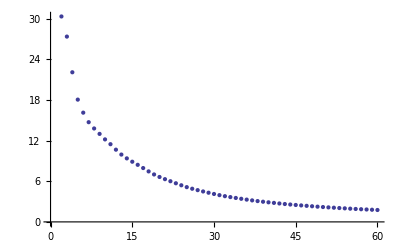

```mathematica
ListPlot[Out[383]]
```

### 1-χ Solutions (Note: χ was previously Omega in hep-th/0611001)

```mathematica
nPar=Length@AAeqs;
```

```mathematica
oneChiAASols=ParallelTable[Solve[Thread[Flatten@Delete[AAeqs,ii]==0],yvars,Integers],{ii,nPar}];
(*Export["Chi-01_AASols.mx",oneChiAASols]*)
```

Omega-01_AASols.mx

```mathematica
oneChiAASols=Import["Chi-01_AASols.mx"];
```

```mathematica
oneChiTadEqs=FactorTerms@Expand[ Tadpole/.#][[1]]&/@oneChiAASols;
```

```mathematica
oneChiTadEqs
```

{ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[16 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[32 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[64 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers]}

```mathematica
eqs=DeleteDuplicates[oneChiTadEqs]
```

{ConditionalExpression[4 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[2 (C[1]^2+2 C[1] C[2]+2 C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[2 (C[1]^2+C[2]^2),(C[1]|C[2])∈Integers],ConditionalExpression[C[1]^2+C[2]^2,(C[1]|C[2])∈Integers],ConditionalExpression[C[1]^2+2 C[1] C[2]+2 C[2]^2,(C[1]|C[2])∈Integers]}

```mathematica
sols=Table[Solve[eqs[[ii]]≤40,Variables[eqs[[ii]]],Integers],{ii,Length[eqs]}];
```

```mathematica
sols[[1]]
```

{{C[1]→-4,C[2]→1},{C[1]→-4,C[2]→2},{C[1]→-4,C[2]→3},{C[1]→-3,C[2]→0},{C[1]→-3,C[2]→1},{C[1]→-3,C[2]→2},{C[1]→-3,C[2]→3},{C[1]→-2,C[2]→-1},{C[1]→-2,C[2]→0},{C[1]→-2,C[2]→1},{C[1]→-2,C[2]→2},{C[1]→-2,C[2]→3},{C[1]→-1,C[2]→-1},{C[1]→-1,C[2]→0},{C[1]→-1,C[2]→1},{C[1]→-1,C[2]→2},{C[1]→0,C[2]→-2},{C[1]→0,C[2]→-1},{C[1]→0,C[2]→0},{C[1]→0,C[2]→1},{C[1]→0,C[2]→2},{C[1]→1,C[2]→-2},{C[1]→1,C[2]→-1},{C[1]→1,C[2]→0},{C[1]→1,C[2]→1},{C[1]→2,C[2]→-3},{C[1]→2,C[2]→-2},{C[1]→2,C[2]→-1},{C[1]→2,C[2]→0},{C[1]→2,C[2]→1},{C[1]→3,C[2]→-3},{C[1]→3,C[2]→-2},{C[1]→3,C[2]→-1},{C[1]→3,C[2]→0},{C[1]→4,C[2]→-3},{C[1]→4,C[2]→-2},{C[1]→4,C[2]→-1}}

```mathematica
Union[eqs[[1]]/.sols[[1]]]
```

{0,4,8,16,20,32,36,40}

```mathematica
tadVars=Variables[AATadEqs[[-1]]];
```

```mathematica
sols=ParallelTable[Solve[0<AATadEqs[[ii]]≤64,tadVars,Integers],{ii,nPar}];
```

```mathematica
Dimensions/@sols
```

{{4,2},{8,2},{8,2},{4,2},{8,2},{4,2},{8,2},{8,2},{8,2},{12,2},{8,2},{8,2},{8,2},{4,2},{8,2},{4,2},{8,2},{8,2},{4,2},{8,2},{8,2},{8,2},{12,2},{8,2},{8,2},{8,2},{8,2},{12,2},{8,2},{12,2},{12,2},{8,2},{8,2},{8,2},{8,2},{4,2},{8,2},{4,2},{8,2},{8,2},{4,2},{8,2},{8,2},{8,2},{4,2},{8,2},{8,2},{8,2},{12,2},{8,2},{8,2},{8,2},{8,2},{12,2},{8,2},{12,2},{12,2},{8,2},{8,2},{8,2},{8,2},{8,2},{12,2},{8,2},{12,2},{12,2},{8,2},{12,2},{12,2},{12,2},{8,2},{8,2},{8,2},{8,2},{8,2},{4,2},{8,2},{4,2},{8,2},{8,2},{4,2},{8,2},{8,2},{8,2},{4,2},{8,2},{8,2},{8,2},{8,2},{4,2},{4,2}}

```mathematica
AASols=Table[AAReIm[[2ii-1]]+I AAReIm[[2ii]],{ii,nPar}];
```

```mathematica
Dimensions@AASols
```

{91}

```mathematica
oneChiAReIm=ParallelTable[DeleteDuplicates[Expand[AAReIm/.oneOmegaAAIntCo[[ii]]/.#]&/@sols[[ii]]],{ii,Length[sols]}];
```

```mathematica
DeleteDuplicates[Select[#,#≠0&]&/@Flatten[oneOmegaRes,2]]
```

{{1/8},{ⅈ/8},{-ⅈ/8},{-1/8},{1/16+ⅈ/16},{1/16},{ⅈ/16},{1/16-ⅈ/16},{-1/16+ⅈ/16},{-ⅈ/16},{-1/16},{-1/16-ⅈ/16},{1/32-ⅈ/32},{1/32},{1/32+ⅈ/32},{-ⅈ/32},{ⅈ/32},{-1/32-ⅈ/32},{-1/32},{-1/32+ⅈ/32}}

### 2-χ Solutions

```mathematica
Binomial[91,2]
FactorInteger@Binomial[91,2]
```

4095

{{3,2},{5,1},{7,1},{13,1}}

```mathematica
SubParts=PartitionSubsets[OrbitSelect[2]]
Length@SubParts[[1]]
Length@SubParts[[2]]
```

{{{1,{{4,{1,1}}},1},{2,{{4,{1,1}}},1},{3,{{4,{1,1}}},1},{1,{{1,{1,14}}},14},{2,{{2,{1,14}}},14},{1,{{2,{1,15}}},15},{3,{{1,{1,15}}},15},{3,{{2,{1,15}}},15},{3,{{3,{1,59}}},59}},{}}

9

0

```mathematica
parts=Table[Tuples[Range[#[[2,2]]]&/@SubParts[[1,ii,2]]],{ii,Length[SubParts[[1]]]}];
(*parts=Tuples[(Range[#[[2,2,-1]]]&/@(test[[2,1,2]]))];*)
```

```mathematica
genOrbits=Flatten[Table[GenerateSubsets[orbits,SubParts[[1,jj]],parts[[jj,ii]],2],{jj,Length[SubParts[[1]]]},{ii,Length[parts[[jj]]]}],2];
```

```mathematica
Dimensions@genOrbits
```

{135,2,1}

```mathematica
CoeffTad=Last@CoefficientArrays[Tadpole,Variables[Tadpole]];
```

```mathematica
(twoChiAASols=ParallelTable[Flatten[({FactorTerms@Expand[#[[1]].CoeffTad.Transpose[#]],#}&@((yvars/.Solve[Thread[Flatten@Delete[AAeqs,genOrbits[[ii]]]==0],yvars,Integers])[[;;,;;,1]])),1],{ii,Length[genOrbits]}];)//AbsoluteTiming
```

{101.51211,Null}

```mathematica
Dimensions@twoChiAASols
```

{135,2}

```mathematica
DeleteDuplicates[twoChiAASols[[;;,1]]]
```

{32 (2 C[1]^2+4 C[1] C[2]+4 C[2]^2+2 C[2] C[3]+C[3]^2-2 C[1] C[4]-2 C[2] C[4]+C[4]^2),8 (5 C[1]^2+5 C[2]^2-2 C[1] C[3]+2 C[2] C[3]+2 C[3]^2-2 C[1] C[4]-2 C[2] C[4]+2 C[4]^2),16 (3 C[1]^2+3 C[2]^2-2 C[1] C[3]-2 C[2] C[3]+2 C[3]^2-4 C[2] C[4]+4 C[3] C[4]+4 C[4]^2),32 (C[1]^2+C[2]^2-2 C[2] C[3]+2 C[3]^2+2 C[1] C[4]-2 C[2] C[4]+4 C[3] C[4]+4 C[4]^2),32 (C[1]^2+C[2]^2-2 C[1] C[3]+2 C[3]^2-2 C[2] C[4]+2 C[4]^2),16 (C[1]^2+C[2]^2-C[1] C[3]-C[2] C[3]+C[3]^2+C[1] C[4]-C[2] C[4]+C[4]^2),16 (C[1]^2+C[2]^2-C[1] C[3]+C[2] C[3]+C[3]^2-C[1] C[4]-C[2] C[4]+C[4]^2),8 (2 C[1]^2+4 C[1] C[2]+4 C[2]^2-2 C[1] C[3]+5 C[3]^2-2 C[1] C[4]-4 C[2] C[4]+5 C[4]^2),8 (5 C[1]^2+5 C[2]^2-2 C[1] C[3]-2 C[2] C[3]+2 C[3]^2-4 C[2] C[4]+4 C[3] C[4]+4 C[4]^2),8 (5 C[1]^2+10 C[1] C[2]+10 C[2]^2-8 C[1] C[3]-6 C[2] C[3]+5 C[3]^2-2 C[1] C[4]-10 C[2] C[4]+5 C[4]^2),16 (3 C[1]^2+3 C[2]^2+2 C[1] C[3]-2 C[2] C[3]+2 C[3]^2+4 C[1] C[4]+4 C[3] C[4]+4 C[4]^2),16 (3 C[1]^2+3 C[2]^2-2 C[1] C[3]+2 C[2] C[3]+2 C[3]^2-4 C[1] C[4]+4 C[3] C[4]+4 C[4]^2),8 (3 C[1]^2+3 C[2]^2-2 C[1] C[3]+2 C[2] C[3]+2 C[3]^2-2 C[1] C[4]-2 C[2] C[4]+2 C[4]^2),8 (3 C[1]^2+4 C[1] C[2]+3 C[2]^2+4 C[1] C[3]+4 C[2] C[3]+4 C[3]^2+8 C[1] C[4]+8 C[2] C[4]+8 C[3] C[4]+8 C[4]^2),8 (3 C[1]^2+6 C[1] C[2]+6 C[2]^2-4 C[1] C[3]-2 C[2] C[3]+3 C[3]^2-2 C[1] C[4]-6 C[2] C[4]+3 C[4]^2),8 (3 C[1]^2+3 C[2]^2-4 C[1] C[3]-4 C[2] C[3]+4 C[3]^2-8 C[2] C[4]+8 C[3] C[4]+8 C[4]^2),32 (C[1]^2+C[1] C[2]+C[2]^2+C[1] C[3]+C[2] C[3]+C[3]^2+2 C[1] C[4]+2 C[2] C[4]+2 C[3] C[4]+2 C[4]^2),32 (C[1]^2+C[2]^2-C[1] C[3]+C[2] C[3]+C[3]^2-C[1] C[4]-C[2] C[4]+C[4]^2),32 (C[1]^2+2 C[1] C[2]+2 C[2]^2-C[1] C[3]+C[3]^2-C[1] C[4]-2 C[2] C[4]+C[4]^2),32 (C[1]^2+C[2]^2+C[1] C[3]-C[2] C[3]+C[3]^2+2 C[1] C[4]+2 C[3] C[4]+2 C[4]^2),32 (C[1]^2+C[2]^2-C[1] C[3]+C[2] C[3]+C[3]^2-2 C[1] C[4]+2 C[3] C[4]+2 C[4]^2),16 (C[1]^2+C[2]^2-2 C[1] C[3]+2 C[3]^2-2 C[2] C[4]+2 C[4]^2),32 (C[1]^2+2 C[1] C[2]+2 C[2]^2-C[1] C[3]+C[3]^2-2 C[1] C[4]-2 C[2] C[4]+2 C[3] C[4]+2 C[4]^2),32 (C[1]^2+C[2]^2-C[1] C[3]-C[2] C[3]+C[3]^2-2 C[2] C[4]+2 C[3] C[4]+2 C[4]^2)}

```mathematica
Export["Chi-02_AASols.mx",twoChiAASols]
```

Omegas-02_AASols_Orbits.mx

```mathematica
twoChiTadEqs=DeleteDuplicates[twoChiAASols[[;;,1]]];
```

```mathematica
tadVars2=Variables[twoChiTadEqs[[-1]]];
```

```mathematica
twoChiTadSols=ParallelTable[{twoChiTadEqs[[ii]],Solve[0<twoChiTadEqs[[ii]]≤70,tadVars2,Integers]},{ii,Length[twoChiTadEqs]}];
```

```mathematica
tadVals=Union@Flatten@Table[twoChiTadEqs[[ii]]/.twoChiTadSols[[ii,2]],{ii,Length[twoChiTadEqs]}]
```

{16,24,32,40,48,56,64}

```mathematica
twoChiTadSols[[1]]
```

{32 (2 C[1]^2+4 C[1] C[2]+4 C[2]^2+2 C[2] C[3]+C[3]^2-2 C[1] C[4]-2 C[2] C[4]+C[4]^2),{{C[1]→-2,C[2]→1,C[3]→-1,C[4]→-1},{C[1]→-1,C[2]→0,C[3]→-1,C[4]→-1},{C[1]→-1,C[2]→0,C[3]→0,C[4]→-2},{C[1]→-1,C[2]→0,C[3]→0,C[4]→-1},{C[1]→-1,C[2]→0,C[3]→0,C[4]→0},{C[1]→-1,C[2]→0,C[3]→1,C[4]→-1},{C[1]→-1,C[2]→1,C[3]→-2,C[4]→0},{C[1]→-1,C[2]→1,C[3]→-1,C[4]→-1},{C[1]→-1,C[2]→1,C[3]→-1,C[4]→0},{C[1]→-1,C[2]→1,C[3]→-1,C[4]→1},{C[1]→-1,C[2]→1,C[3]→0,C[4]→0},{C[1]→0,C[2]→-1,C[3]→1,C[4]→-1},{C[1]→0,C[2]→0,C[3]→-1,C[4]→-1},{C[1]→0,C[2]→0,C[3]→-1,C[4]→0},{C[1]→0,C[2]→0,C[3]→-1,C[4]→1},{C[1]→0,C[2]→0,C[3]→0,C[4]→-1},{C[1]→0,C[2]→0,C[3]→0,C[4]→1},{C[1]→0,C[2]→0,C[3]→1,C[4]→-1},{C[1]→0,C[2]→0,C[3]→1,C[4]→0},{C[1]→0,C[2]→0,C[3]→1,C[4]→1},{C[1]→0,C[2]→1,C[3]→-1,C[4]→1},{C[1]→1,C[2]→-1,C[3]→0,C[4]→0},{C[1]→1,C[2]→-1,C[3]→1,C[4]→-1},{C[1]→1,C[2]→-1,C[3]→1,C[4]→0},{C[1]→1,C[2]→-1,C[3]→1,C[4]→1},{C[1]→1,C[2]→-1,C[3]→2,C[4]→0},{C[1]→1,C[2]→0,C[3]→-1,C[4]→1},{C[1]→1,C[2]→0,C[3]→0,C[4]→0},{C[1]→1,C[2]→0,C[3]→0,C[4]→1},{C[1]→1,C[2]→0,C[3]→0,C[4]→2},{C[1]→1,C[2]→0,C[3]→1,C[4]→1},{C[1]→2,C[2]→-1,C[3]→1,C[4]→1}}}

```mathematica
twoChiTadAARes=Table[DeleteDuplicates[Flatten[Select[twoChiAASols,#[[1]]==twoChiTadSols[[ii,1]]&]/.twoChiTadSols[[ii,2]],1]],{ii,Length[twoChiTadSols]}];
```

```mathematica
Dimensions/@twoChiTadAARes
```

{{144,2},{192,2},{168,2},{116,2},{172,2},{1728,2},{480,2},{116,2},{116,2},{32,2},{88,2},{88,2},{560,2},{376,2},{376,2},{100,2},{648,2},{168,2},{408,2},{248,2},{248,2},{248,2},{88,2},{488,2}}

```mathematica
Dimensions[Flatten[twoChiTadAARes,1]]
Dimensions@DeleteDuplicates[Flatten[twoChiTadAARes,1]]
```

{7396,2}

{6820,2}

```mathematica
HAdS[[Flatten[orbits[[#]]]]][[1]]&/@Range[Length[orbits]]
ParallelTable[DeleteDuplicates[{#[[1]],Flux[#[[2]],orbits]}&/@(Select[Flatten[twoChiTadAARes,1],#[[1]]==tVal&])],{tVal,tadVals[[;;4]]}]
```

{{1,1,1,1,3,3},{1,1,2,2,2,2},{1,1,1,2,2,3},{3,3,3,3,3,3}}

{{{16,{{},{1/32},{},{}}},{16,{{},{-ⅈ/32},{},{}}},{16,{{},{-1/32},{},{}}},{16,{{},{ⅈ/32},{},{}}},{16,{{},{1/64-ⅈ/64,1/64-ⅈ/64},{},{}}},{16,{{},{1/64-ⅈ/64,-1/64-ⅈ/64},{},{}}},{16,{{},{1/64+ⅈ/64,1/64-ⅈ/64},{},{}}},{16,{{},{1/64+ⅈ/64,-1/64-ⅈ/64},{},{}}},{16,{{},{1/64-ⅈ/64,-1/64+ⅈ/64},{},{}}},{16,{{},{1/64+ⅈ/64,-1/64+ⅈ/64},{},{}}},{16,{{},{-1/64-ⅈ/64,1/64-ⅈ/64},{},{}}},{16,{{},{-1/64-ⅈ/64,-1/64-ⅈ/64},{},{}}},{16,{{},{-1/64-ⅈ/64,-1/64+ⅈ/64},{},{}}},{16,{{},{1/64-ⅈ/64,1/64+ⅈ/64},{},{}}},{16,{{},{-1/64+ⅈ/64,1/64-ⅈ/64},{},{}}},{16,{{},{-1/64+ⅈ/64,-1/64-ⅈ/64},{},{}}},{16,{{},{-1/64+ⅈ/64,-1/64+ⅈ/64},{},{}}},{16,{{},{1/64+ⅈ/64,1/64+ⅈ/64},{},{}}},{16,{{},{-1/64-ⅈ/64,1/64+ⅈ/64},{},{}}},{16,{{},{-1/64+ⅈ/64,1/64+ⅈ/64},{},{}}},{16,{{},{},{ⅈ/32,-ⅈ/32},{}}},{16,{{},{},{ⅈ/32,ⅈ/32},{}}},{16,{{},{},{1/32,1/32},{}}},{16,{{},{},{1/32,-1/32},{}}},{16,{{},{},{-ⅈ/32,-ⅈ/32},{}}},{16,{{},{},{-ⅈ/32,ⅈ/32},{}}},{16,{{},{},{-1/32,1/32},{}}},{16,{{},{},{-1/32,-1/32},{}}}},{{24,{{},{1/64-ⅈ/64},{1/32+ⅈ/32},{}}},{24,{{},{-1/64-ⅈ/64},{1/32+ⅈ/32},{}}},{24,{{},{-1/64+ⅈ/64},{1/32+ⅈ/32},{}}},{24,{{},{1/64+ⅈ/64},{1/32+ⅈ/32},{}}},{24,{{},{1/64-ⅈ/64},{1/32-ⅈ/32},{}}},{24,{{},{-1/64-ⅈ/64},{1/32-ⅈ/32},{}}},{24,{{},{-1/64+ⅈ/64},{1/32-ⅈ/32},{}}},{24,{{},{1/64+ⅈ/64},{1/32-ⅈ/32},{}}},{24,{{},{1/64-ⅈ/64},{-1/32+ⅈ/32},{}}},{24,{{},{-1/64-ⅈ/64},{-1/32+ⅈ/32},{}}},{24,{{},{-1/64+ⅈ/64},{-1/32+ⅈ/32},{}}},{24,{{},{1/64+ⅈ/64},{-1/32+ⅈ/32},{}}},{24,{{},{1/64-ⅈ/64},{-1/32-ⅈ/32},{}}},{24,{{},{-1/64-ⅈ/64},{-1/32-ⅈ/32},{}}},{24,{{},{-1/64+ⅈ/64},{-1/32-ⅈ/32},{}}},{24,{{},{1/64+ⅈ/64},{-1/32-ⅈ/32},{}}}},{{32,{{1/16},{},{},{1/16}}},{32,{{1/16,1/16},{},{},{}}},{32,{{1/16,-1/16},{},{},{}}},{32,{{ⅈ/16},{},{},{ⅈ/16}}},{32,{{ⅈ/16,ⅈ/16},{},{},{}}},{32,{{ⅈ/16,-ⅈ/16},{},{},{}}},{32,{{-1/16},{},{},{1/16}}},{32,{{ⅈ/16},{},{},{-ⅈ/16}}},{32,{{-ⅈ/16,ⅈ/16},{},{},{}}},{32,{{-ⅈ/16,-ⅈ/16},{},{},{}}},{32,{{-ⅈ/16},{},{},{ⅈ/16}}},{32,{{1/16},{},{},{-1/16}}},{32,{{-1/16,1/16},{},{},{}}},{32,{{-1/16,-1/16},{},{},{}}},{32,{{-ⅈ/16},{},{},{-ⅈ/16}}},{32,{{-1/16},{},{},{-1/16}}},{32,{{},{1/32-ⅈ/32},{},{}}},{32,{{},{-1/32-ⅈ/32},{},{}}},{32,{{},{-1/32+ⅈ/32},{},{}}},{32,{{},{1/32+ⅈ/32},{},{}}},{32,{{},{},{1/16},{}}},{32,{{},{},{ⅈ/16},{}}},{32,{{},{},{-ⅈ/16},{}}},{32,{{},{},{-1/16},{}}},{32,{{},{1/32,1/32},{},{}}},{32,{{},{1/32,-ⅈ/32},{},{}}},{32,{{},{1/32,-1/32},{},{}}},{32,{{},{1/32,ⅈ/32},{},{}}},{32,{{},{-ⅈ/32,-ⅈ/32},{},{}}},{32,{{},{-ⅈ/32,-1/32},{},{}}},{32,{{},{-ⅈ/32,ⅈ/32},{},{}}},{32,{{},{-ⅈ/32,1/32},{},{}}},{32,{{},{ⅈ/32,-ⅈ/32},{},{}}},{32,{{},{ⅈ/32,-1/32},{},{}}},{32,{{},{ⅈ/32,ⅈ/32},{},{}}},{32,{{},{-1/32,-ⅈ/32},{},{}}},{32,{{},{-1/32,-1/32},{},{}}},{32,{{},{-1/32,ⅈ/32},{},{}}},{32,{{},{ⅈ/32,1/32},{},{}}},{32,{{},{-1/32,1/32},{},{}}},{32,{{},{},{1/32+ⅈ/32,1/32+ⅈ/32},{}}},{32,{{},{},{1/32+ⅈ/32,1/32-ⅈ/32},{}}},{32,{{},{},{1/32+ⅈ/32,-1/32-ⅈ/32},{}}},{32,{{},{},{1/32+ⅈ/32,-1/32+ⅈ/32},{}}},{32,{{},{},{1/32-ⅈ/32,1/32+ⅈ/32},{}}},{32,{{},{},{1/32-ⅈ/32,1/32-ⅈ/32},{}}},{32,{{},{},{1/32-ⅈ/32,-1/32-ⅈ/32},{}}},{32,{{},{},{1/32-ⅈ/32,-1/32+ⅈ/32},{}}},{32,{{},{},{-1/32+ⅈ/32,1/32+ⅈ/32},{}}},{32,{{},{},{-1/32+ⅈ/32,1/32-ⅈ/32},{}}},{32,{{},{},{-1/32+ⅈ/32,-1/32-ⅈ/32},{}}},{32,{{},{},{-1/32+ⅈ/32,-1/32+ⅈ/32},{}}},{32,{{},{},{-1/32-ⅈ/32,1/32+ⅈ/32},{}}},{32,{{},{},{-1/32-ⅈ/32,1/32-ⅈ/32},{}}},{32,{{},{},{-1/32-ⅈ/32,-1/32-ⅈ/32},{}}},{32,{{},{},{-1/32-ⅈ/32,-1/32+ⅈ/32},{}}}},{{40,{{},{1/64-ⅈ/64},{},{1/16+ⅈ/16}}},{40,{{1/16+ⅈ/16},{1/64-ⅈ/64},{},{}}},{40,{{1/16+ⅈ/16},{-1/64-ⅈ/64},{},{}}},{40,{{1/16+ⅈ/16},{-1/64+ⅈ/64},{},{}}},{40,{{},{1/64+ⅈ/64},{},{1/16+ⅈ/16}}},{40,{{1/16+ⅈ/16},{1/64+ⅈ/64},{},{}}},{40,{{},{-1/64-ⅈ/64},{},{1/16+ⅈ/16}}},{40,{{},{-1/64+ⅈ/64},{},{1/16+ⅈ/16}}},{40,{{},{1/64-ⅈ/64},{},{1/16-ⅈ/16}}},{40,{{1/16-ⅈ/16},{1/64-ⅈ/64},{},{}}},{40,{{1/16-ⅈ/16},{-1/64-ⅈ/64},{},{}}},{40,{{1/16-ⅈ/16},{-1/64+ⅈ/64},{},{}}},{40,{{},{1/64+ⅈ/64},{},{1/16-ⅈ/16}}},{40,{{1/16-ⅈ/16},{1/64+ⅈ/64},{},{}}},{40,{{},{-1/64-ⅈ/64},{},{1/16-ⅈ/16}}},{40,{{},{-1/64+ⅈ/64},{},{1/16-ⅈ/16}}},{40,{{},{1/64-ⅈ/64},{},{-1/16+ⅈ/16}}},{40,{{-1/16+ⅈ/16},{1/64-ⅈ/64},{},{}}},{40,{{-1/16+ⅈ/16},{-1/64-ⅈ/64},{},{}}},{40,{{-1/16+ⅈ/16},{-1/64+ⅈ/64},{},{}}},{40,{{},{1/64+ⅈ/64},{},{-1/16+ⅈ/16}}},{40,{{-1/16+ⅈ/16},{1/64+ⅈ/64},{},{}}},{40,{{},{-1/64-ⅈ/64},{},{-1/16+ⅈ/16}}},{40,{{},{-1/64+ⅈ/64},{},{-1/16+ⅈ/16}}},{40,{{},{1/64-ⅈ/64},{},{-1/16-ⅈ/16}}},{40,{{-1/16-ⅈ/16},{1/64-ⅈ/64},{},{}}},{40,{{-1/16-ⅈ/16},{-1/64-ⅈ/64},{},{}}},{40,{{-1/16-ⅈ/16},{-1/64+ⅈ/64},{},{}}},{40,{{},{1/64+ⅈ/64},{},{-1/16-ⅈ/16}}},{40,{{-1/16-ⅈ/16},{1/64+ⅈ/64},{},{}}},{40,{{},{-1/64-ⅈ/64},{},{-1/16-ⅈ/16}}},{40,{{},{-1/64+ⅈ/64},{},{-1/16-ⅈ/16}}}}}

```mathematica
Length[Out[719]]
```

28

```mathematica
Flatten[Select[twoChiAASols,#[[1]]==twoChiTadSols[[1,1]]&]/.twoChiTadSols[[1,2]],1]
```

{{64,{-2,0,-2,0,-1,-1,-1,-1,-4,0,-4,0,-2,-2,-1,1,-2,2,-2,0,-1,1,-2,0,-1,-1,-2,0,-2,0,-1,-1,-1,1,-2,2,-2,0,-1,1,-2,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,-2,0,-2,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,-2,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,1,-1,0,-2,2,-2,2,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,-2,1,-1,0,-2,2,-2,2,0,1,-1,2,0,1,1,-1,-1,0,-2,1,-1,0,-2,2,-2,2,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},«158»,{64,{2,0,1,1,1,1,0,2,2,2,0,0,0,2,2,-2,2,2,4,0,-2,0,0,2,2,2,2,0,1,1,1,1,0,-2,2,-2,2,-2,0,0,2,0,2,0,-1,«92»,-2,-2,2,0,2,2,0,3,1,3,-1,0,-2,2,4,4,2,2,-2,-1,3,1,3,2,0,-2,2,-2,-2,-2,0,2,0,0,4,2,2,-2,0,-2,2,0,2,0,0}}}

### 3-χ Solutions

```mathematica
FactorInteger@Binomial[91,3]
```

{{3,1},{5,1},{7,1},{13,1},{89,1}}

```mathematica
7*13*89
```

8099

```mathematica
SubParts=PartitionSubsets[OrbitSelect[3]]
Length@SubParts[[1]]
Length@SubParts[[2]]
```

{{{1,{{1,{1,14}},{4,{1,1}}},14},{2,{{2,{1,14}},{4,{1,1}}},14},{1,{{2,{1,15}},{4,{1,1}}},15},{3,{{1,{1,15}},{4,{1,1}}},15},{3,{{2,{1,15}},{4,{1,1}}},15},{3,{{3,{1,59}},{4,{1,1}}},59}},{{1,{{1,{2,{13,7}}}}},{1,{{2,{2,{7,15}}}}},{2,{{1,{2,{7,15}}}}},{2,{{2,{2,{13,7}}}}},{3,{{1,{2,{7,15}}}}},{3,{{2,{2,{7,15}}}}},{3,{{3,{2,{59,29}}}}},{3,{{2,{1,{5,3}}},{1,{1,{5,3}}}}},{3,{{3,{1,{59}}},{1,{1,{5,3}}}}},{3,{{3,{1,{59}}},{2,{1,{5,3}}}}}}}

6

10

```mathematica
parts1=Table[Tuples[Range[#[[2,2]]]&/@SubParts[[1,ii,2]]],{ii,Length[SubParts[[1]]]}];
(*parts=Tuples[(Range[#[[2,2,-1]]]&/@(test[[2,1,2]]))];*)
```

```mathematica
Dimensions@parts1
```

{6}

```mathematica
genOrbits=Flatten[Table[GenerateSubsets[orbits,SubParts[[1,jj]],parts1[[jj,ii]],2],{jj,Length[SubParts[[1]]]},{ii,Length[parts1[[jj]]]}],2];
```

```mathematica
Dimensions@genOrbits
```

{132,3,1}

```mathematica
CoeffTad=Last@CoefficientArrays[Tadpole,Variables[Tadpole]];
```

```mathematica
(threeChiAASolsPart1=ParallelTable[Flatten[({FactorTerms@Expand[#[[1]].CoeffTad.Transpose[#]],#}&@((yvars/.Solve[Thread[Flatten@Delete[AAeqs,genOrbits[[ii]]]==0],yvars,Integers])[[;;,;;,1]])),1],{ii,Length[genOrbits]}];)//AbsoluteTiming
```

{101.7301,Null}

```mathematica
(threeChiAASolsPart2=Reap[Do[Block[{parts=Tuples[(Range[#[[2,2,-1]]]&/@(SubParts[[2,pickOrbit,2]]))]},Sow@Flatten[ParallelTable[Flatten[({FactorTerms@Expand[#[[1]].CoeffTad.Transpose[#]],#}&@((yvars/.Solve[Thread[Flatten@Delete[AAeqs,#]==0],yvars,Integers])[[;;,;;,1]])),1]&/@GenerateSubsets[orbits,SubParts[[2,pickOrbit]],parts[[ii]]],{ii,Length[parts]}],1];],{pickOrbit,Length[SubParts[[2]]]}]][[2,1]];)//AbsoluteTiming
```

{197.39029,Null}

```mathematica
Dimensions/@threeChiAASolsPart2
```

{{91,2,1},{105,2,1}}

```mathematica
Dimensions[Flatten[#,1]&/@Flatten[twoChiAASolsPart2,1]]
```

{196,2}

```mathematica
threeChiAASols=Join[threeChiAASolsPart1,Flatten[threeChiAASolsPart2,1]];
```

```mathematica
Dimensions@threeChiAASols
```

{328,2}

```mathematica
threeChiTadEqs=DeleteDuplicates[threeChiAASols[[;;,1]]];
```

```mathematica
tadVars3=Variables[threeChiTadEqs[[-1]]];
```

```mathematica
threeChiTadSols=ParallelTable[{threeChiTadEqs[[ii]],Solve[0<threeChiTadEqs[[ii]]≤70,tadVars3,Integers]},{ii,Length[threeChiTadEqs]}];
```

```mathematica
Union@Flatten@Table[threeChiTadEqs[[ii]]/.threeChiTadSols[[ii,2]],{ii,Length[threeChiTadEqs]}]
```

```mathematica
threeChiTadSols[[1]]
```

```mathematica
threeChiTadAARes=Table[DeleteDuplicates[Flatten[Select[threeChiAASols,#[[1]]==threeChiTadSols[[ii,1]]&]/.threeChiTadSols[[ii,2]],1]],{ii,Length[threeChiTadSols]}];
```

```mathematica
Dimensions[Flatten[threeChiTadAARes,1]]
Dimensions@DeleteDuplicates[Flatten[threeChiTadAARes,1]]
```

```mathematica
HAdS[[Flatten[orbits[[#]]]]][[1]]&/@Range[Length[orbits]]
DeleteDuplicates[{#[[1]],Flux[#[[2]],orbits]}&/@(Select[Flatten[threeChiTadAARes,1],#[[1]]==16&])]
```

### 4-χ Solutions

```mathematica
nPar=Length@AAeqs;
```

```mathematica
Binomial[91,4]
FactorInteger@Binomial[91,4]
```

2672670

{{2,1},{3,1},{5,1},{7,1},{11,1},{13,1},{89,1}}

```mathematica
89*13*3
```

3471

```mathematica
parts=Subsets[Thread[{Range[nPar]}],{4}];
```

```mathematica
Dimensions@parts
```

{2672670,4,1}

```mathematica
AbsoluteTiming[fourOmegaAAIntCo=ParallelTable[FactorTerms@Expand[Tadpole/.Solve[Thread[Flatten@Delete[AAeqs,parts[[ii]]]==0],yvars,Integers]],{ii,89(*Length[parts]*)},Method->"FinestGrained"];]
```

{113.84664,Null}

```mathematica
DeleteDuplicates[fourOmegaAAIntCo][[;;,1,1]]
```

{8 (4 C[1]^2+4 C[2]^2+8 C[1] C[3]+8 C[3]^2+8 C[2] C[4]+8 C[4]^2-8 C[1] C[5]+8 C[2] C[5]-12 C[3] C[5]+12 C[4] C[5]+12 C[5]^2-8 C[1] C[6]-8 C[2] C[6]-12 C[3] C[6]-12 C[4] C[6]+12 C[6]^2-4 C[2] C[7]-2 C[3] C[7]-6 C[4] C[7]-4 C[5] C[7]+4 C[6] C[7]+3 C[7]^2+4 C[1] C[8]-4 C[2] C[8]+4 C[3] C[8]-8 C[4] C[8]-8 C[5] C[8]+6 C[7] C[8]+6 C[8]^2),8 (5 C[1]^2+5 C[2]^2+6 C[1] C[3]+5 C[3]^2+6 C[2] C[4]+5 C[4]^2-10 C[1] C[5]+4 C[2] C[5]-10 C[3] C[5]+4 C[4] C[5]+9 C[5]^2-4 C[1] C[6]-10 C[2] C[6]-4 C[3] C[6]-10 C[4] C[6]+9 C[6]^2-6 C[1] C[7]+4 C[2] C[7]-6 C[3] C[7]+4 C[4] C[7]+10 C[5] C[7]-4 C[6] C[7]+5 C[7]^2-10 C[1] C[8]-2 C[2] C[8]-10 C[3] C[8]-2 C[4] C[8]+14 C[5] C[8]+6 C[6] C[8]+10 C[7] C[8]+10 C[8]^2),8 (5 C[1]^2+5 C[2]^2+4 C[1] C[3]+2 C[2] C[3]+3 C[3]^2-2 C[1] C[4]+4 C[2] C[4]+3 C[4]^2-10 C[1] C[5]+6 C[2] C[5]-6 C[3] C[5]+6 C[4] C[5]+10 C[5]^2-6 C[1] C[6]-10 C[2] C[6]-6 C[3] C[6]-6 C[4] C[6]+10 C[6]^2-2 C[1] C[7]+2 C[4] C[7]+2 C[5] C[7]-2 C[6] C[7]+3 C[7]^2-2 C[2] C[8]-2 C[3] C[8]+2 C[5] C[8]+2 C[6] C[8]+3 C[8]^2),16 (5 C[1]^2+5 C[2]^2+10 C[1] C[3]+2 C[2] C[3]+7 C[3]^2-2 C[1] C[4]+10 C[2] C[4]+7 C[4]^2-16 C[1] C[5]+8 C[2] C[5]-18 C[3] C[5]+14 C[4] C[5]+20 C[5]^2-8 C[1] C[6]-16 C[2] C[6]-14 C[3] C[6]-18 C[4] C[6]+20 C[6]^2+2 C[1] C[7]+4 C[2] C[7]+4 C[3] C[7]+4 C[4] C[7]-2 C[5] C[7]-10 C[6] C[7]+2 C[7]^2-4 C[1] C[8]+2 C[2] C[8]-4 C[3] C[8]+4 C[4] C[8]+10 C[5] C[8]-2 C[6] C[8]+2 C[8]^2),16 (7 C[1]^2+7 C[2]^2+10 C[1] C[3]-2 C[2] C[3]+5 C[3]^2+2 C[1] C[4]+10 C[2] C[4]+5 C[4]^2-18 C[1] C[5]+14 C[2] C[5]-16 C[3] C[5]+8 C[4] C[5]+20 C[5]^2-14 C[1] C[6]-18 C[2] C[6]-8 C[3] C[6]-16 C[4] C[6]+20 C[6]^2+4 C[1] C[7]+4 C[2] C[7]+2 C[3] C[7]+4 C[4] C[7]-2 C[5] C[7]-10 C[6] C[7]+2 C[7]^2-4 C[1] C[8]+4 C[2] C[8]-4 C[3] C[8]+2 C[4] C[8]+10 C[5] C[8]-2 C[6] C[8]+2 C[8]^2),16 (5 C[1]^2+5 C[2]^2+12 C[1] C[3]+9 C[3]^2+12 C[2] C[4]+9 C[4]^2-22 C[1] C[5]+6 C[2] C[5]-30 C[3] C[5]+10 C[4] C[5]+30 C[5]^2-6 C[1] C[6]-22 C[2] C[6]-10 C[3] C[6]-30 C[4] C[6]+30 C[6]^2+4 C[1] C[7]+8 C[2] C[7]+6 C[3] C[7]+10 C[4] C[7]-6 C[5] C[7]-22 C[6] C[7]+5 C[7]^2-8 C[1] C[8]+4 C[2] C[8]-10 C[3] C[8]+6 C[4] C[8]+22 C[5] C[8]-6 C[6] C[8]+5 C[8]^2),8 (15 C[1]^2+6 C[1] C[2]+3 C[2]^2+26 C[1] C[3]+6 C[2] C[3]+15 C[3]^2+6 C[1] C[4]+2 C[2] C[4]+6 C[3] C[4]+3 C[4]^2+2 C[1] C[5]+2 C[2] C[5]+2 C[3] C[5]+2 C[4] C[5]+2 C[5]^2-2 C[1] C[6]-2 C[2] C[6]-2 C[3] C[6]-2 C[4] C[6]+2 C[6]^2+18 C[1] C[7]+6 C[2] C[7]+18 C[3] C[7]+6 C[4] C[7]+2 C[5] C[7]-2 C[6] C[7]+9 C[7]^2+48 C[1] C[8]+12 C[2] C[8]+48 C[3] C[8]+12 C[4] C[8]+6 C[5] C[8]-2 C[6] C[8]+36 C[7] C[8]+45 C[8]^2),16 (9 C[1]^2+9 C[2]^2+12 C[1] C[3]+5 C[3]^2+12 C[2] C[4]+5 C[4]^2-30 C[1] C[5]+10 C[2] C[5]-22 C[3] C[5]+6 C[4] C[5]+30 C[5]^2-10 C[1] C[6]-30 C[2] C[6]-6 C[3] C[6]-22 C[4] C[6]+30 C[6]^2+6 C[1] C[7]+10 C[2] C[7]+4 C[3] C[7]+8 C[4] C[7]-6 C[5] C[7]-22 C[6] C[7]+5 C[7]^2-10 C[1] C[8]+6 C[2] C[8]-8 C[3] C[8]+4 C[4] C[8]+22 C[5] C[8]-6 C[6] C[8]+5 C[8]^2),16 (19 C[1]^2+20 C[1] C[2]+7 C[2]^2+38 C[1] C[3]+22 C[2] C[3]+21 C[3]^2+22 C[1] C[4]+14 C[2] C[4]+24 C[3] C[4]+9 C[4]^2+54 C[1] C[5]+30 C[2] C[5]+56 C[3] C[5]+36 C[4] C[5]+44 C[5]^2+18 C[1] C[6]+6 C[2] C[6]+16 C[3] C[6]+8 C[4] C[6]+28 C[5] C[6]+8 C[6]^2+32 C[1] C[7]+20 C[2] C[7]+34 C[3] C[7]+22 C[4] C[7]+48 C[5] C[7]+12 C[6] C[7]+16 C[7]^2+54 C[1] C[8]+30 C[2] C[8]+56 C[3] C[8]+34 C[4] C[8]+82 C[5] C[8]+26 C[6] C[8]+48 C[7] C[8]+40 C[8]^2),16 (21 C[1]^2+24 C[1] C[2]+9 C[2]^2+38 C[1] C[3]+22 C[2] C[3]+19 C[3]^2+22 C[1] C[4]+14 C[2] C[4]+20 C[3] C[4]+7 C[4]^2+56 C[1] C[5]+36 C[2] C[5]+54 C[3] C[5]+30 C[4] C[5]+44 C[5]^2+16 C[1] C[6]+8 C[2] C[6]+18 C[3] C[6]+6 C[4] C[6]+28 C[5] C[6]+8 C[6]^2+34 C[1] C[7]+22 C[2] C[7]+32 C[3] C[7]+20 C[4] C[7]+48 C[5] C[7]+12 C[6] C[7]+16 C[7]^2+56 C[1] C[8]+34 C[2] C[8]+54 C[3] C[8]+30 C[4] C[8]+82 C[5] C[8]+26 C[6] C[8]+48 C[7] C[8]+40 C[8]^2),16 (7 C[1]^2+7 C[2]^2+14 C[1] C[3]+2 C[2] C[3]+9 C[3]^2-2 C[1] C[4]+14 C[2] C[4]+9 C[4]^2-24 C[1] C[5]+8 C[2] C[5]-26 C[3] C[5]+14 C[4] C[5]+26 C[5]^2-8 C[1] C[6]-24 C[2] C[6]-14 C[3] C[6]-26 C[4] C[6]+26 C[6]^2+2 C[1] C[7]+8 C[2] C[7]+4 C[3] C[7]+8 C[4] C[7]-16 C[6] C[7]+3 C[7]^2-8 C[1] C[8]+2 C[2] C[8]-8 C[3] C[8]+4 C[4] C[8]+16 C[5] C[8]+3 C[8]^2),8 (16 C[1]^2+8 C[1] C[2]+4 C[2]^2+28 C[1] C[3]+8 C[2] C[3]+16 C[3]^2+8 C[1] C[4]+4 C[2] C[4]+8 C[3] C[4]+4 C[4]^2+24 C[1] C[5]+12 C[2] C[5]+24 C[3] C[5]+12 C[4] C[5]+18 C[5]^2+16 C[1] C[6]+4 C[2] C[6]+16 C[3] C[6]+4 C[4] C[6]+20 C[5] C[6]+10 C[6]^2+20 C[1] C[7]+8 C[2] C[7]+20 C[3] C[7]+8 C[4] C[7]+24 C[5] C[7]+16 C[6] C[7]+10 C[7]^2+36 C[1] C[8]+12 C[2] C[8]+36 C[3] C[8]+12 C[4] C[8]+38 C[5] C[8]+26 C[6] C[8]+30 C[7] C[8]+25 C[8]^2),16 (9 C[1]^2+9 C[2]^2+14 C[1] C[3]-2 C[2] C[3]+7 C[3]^2+2 C[1] C[4]+14 C[2] C[4]+7 C[4]^2-26 C[1] C[5]+14 C[2] C[5]-24 C[3] C[5]+8 C[4] C[5]+26 C[5]^2-14 C[1] C[6]-26 C[2] C[6]-8 C[3] C[6]-24 C[4] C[6]+26 C[6]^2+4 C[1] C[7]+8 C[2] C[7]+2 C[3] C[7]+8 C[4] C[7]-16 C[6] C[7]+3 C[7]^2-8 C[1] C[8]+4 C[2] C[8]-8 C[3] C[8]+2 C[4] C[8]+16 C[5] C[8]+3 C[8]^2),16 (7 C[1]^2+2 C[1] C[2]+C[2]^2+13 C[1] C[3]+3 C[2] C[3]+8 C[3]^2+3 C[1] C[4]+C[2] C[4]+4 C[3] C[4]+2 C[4]^2+2 C[4] C[5]+2 C[5]^2-2 C[1] C[6]-2 C[2] C[6]-4 C[3] C[6]-2 C[4] C[6]+2 C[6]^2+8 C[1] C[7]+2 C[2] C[7]+9 C[3] C[7]+3 C[4] C[7]-2 C[6] C[7]+4 C[7]^2+22 C[1] C[8]+4 C[2] C[8]+23 C[3] C[8]+7 C[4] C[8]+2 C[5] C[8]-4 C[6] C[8]+16 C[7] C[8]+20 C[8]^2),16 (8 C[1]^2+4 C[1] C[2]+2 C[2]^2+13 C[1] C[3]+3 C[2] C[3]+7 C[3]^2+3 C[1] C[4]+C[2] C[4]+2 C[3] C[4]+C[4]^2+2 C[2] C[5]+2 C[5]^2-4 C[1] C[6]-2 C[2] C[6]-2 C[3] C[6]-2 C[4] C[6]+2 C[6]^2+9 C[1] C[7]+3 C[2] C[7]+8 C[3] C[7]+2 C[4] C[7]-2 C[6] C[7]+4 C[7]^2+23 C[1] C[8]+7 C[2] C[8]+22 C[3] C[8]+4 C[4] C[8]+2 C[5] C[8]-4 C[6] C[8]+16 C[7] C[8]+20 C[8]^2),16 (25 C[1]^2+28 C[1] C[2]+9 C[2]^2+48 C[1] C[3]+28 C[2] C[3]+25 C[3]^2+28 C[1] C[4]+16 C[2] C[4]+28 C[3] C[4]+9 C[4]^2+60 C[1] C[5]+36 C[2] C[5]+60 C[3] C[5]+36 C[4] C[5]+44 C[5]^2+8 C[1] C[6]+4 C[2] C[6]+8 C[3] C[6]+4 C[4] C[6]+16 C[5] C[6]+4 C[6]^2+38 C[1] C[7]+22 C[2] C[7]+38 C[3] C[7]+22 C[4] C[7]+44 C[5] C[7]+4 C[6] C[7]+16 C[7]^2+62 C[1] C[8]+36 C[2] C[8]+62 C[3] C[8]+36 C[4] C[8]+80 C[5] C[8]+12 C[6] C[8]+48 C[7] C[8]+40 C[8]^2),16 (3 C[1]^2+3 C[2]^2+6 C[1] C[3]+5 C[3]^2+6 C[2] C[4]+5 C[4]^2-8 C[1] C[5]+6 C[2] C[5]-12 C[3] C[5]+8 C[4] C[5]+12 C[5]^2-6 C[1] C[6]-8 C[2] C[6]-8 C[3] C[6]-12 C[4] C[6]+12 C[6]^2+2 C[2] C[7]+4 C[4] C[7]+2 C[5] C[7]-6 C[6] C[7]+2 C[7]^2-2 C[1] C[8]+2 C[2] C[8]-4 C[3] C[8]+4 C[4] C[8]+8 C[5] C[8]-4 C[6] C[8]+4 C[7] C[8]+4 C[8]^2),16 (5 C[1]^2+5 C[2]^2+6 C[1] C[3]+3 C[3]^2+6 C[2] C[4]+3 C[4]^2-12 C[1] C[5]+8 C[2] C[5]-8 C[3] C[5]+6 C[4] C[5]+12 C[5]^2-8 C[1] C[6]-12 C[2] C[6]-6 C[3] C[6]-8 C[4] C[6]+12 C[6]^2+4 C[2] C[7]+2 C[4] C[7]+2 C[5] C[7]-6 C[6] C[7]+2 C[7]^2-4 C[1] C[8]+4 C[2] C[8]-2 C[3] C[8]+2 C[4] C[8]+8 C[5] C[8]-4 C[6] C[8]+4 C[7] C[8]+4 C[8]^2),16 (2 C[1]^2+2 C[2]^2+4 C[1] C[3]-2 C[2] C[3]+4 C[3]^2+2 C[1] C[4]+4 C[2] C[4]+4 C[4]^2-8 C[1] C[5]+6 C[2] C[5]-14 C[3] C[5]+4 C[4] C[5]+17 C[5]^2-6 C[1] C[6]-8 C[2] C[6]-4 C[3] C[6]-14 C[4] C[6]+17 C[6]^2+2 C[1] C[7]+4 C[2] C[7]+6 C[4] C[7]+2 C[5] C[7]-16 C[6] C[7]+5 C[7]^2-2 C[1] C[8]+6 C[2] C[8]-6 C[3] C[8]+6 C[4] C[8]+18 C[5] C[8]-14 C[6] C[8]+10 C[7] C[8]+10 C[8]^2),8 (3 C[1]^2+3 C[2]^2+2 C[1] C[3]+3 C[3]^2+2 C[2] C[4]+3 C[4]^2-8 C[1] C[5]+2 C[2] C[5]-8 C[3] C[5]+2 C[4] C[5]+13 C[5]^2-2 C[1] C[6]-8 C[2] C[6]-2 C[3] C[6]-8 C[4] C[6]+13 C[6]^2+6 C[2] C[7]+6 C[4] C[7]+2 C[5] C[7]-20 C[6] C[7]+9 C[7]^2-6 C[1] C[8]+6 C[2] C[8]-6 C[3] C[8]+6 C[4] C[8]+22 C[5] C[8]-18 C[6] C[8]+18 C[7] C[8]+18 C[8]^2),16 (4 C[1]^2+4 C[2]^2+4 C[1] C[3]+2 C[2] C[3]+2 C[3]^2-2 C[1] C[4]+4 C[2] C[4]+2 C[4]^2-14 C[1] C[5]+4 C[2] C[5]-8 C[3] C[5]+6 C[4] C[5]+17 C[5]^2-4 C[1] C[6]-14 C[2] C[6]-6 C[3] C[6]-8 C[4] C[6]+17 C[6]^2+6 C[2] C[7]+2 C[3] C[7]+4 C[4] C[7]+2 C[5] C[7]-16 C[6] C[7]+5 C[7]^2-6 C[1] C[8]+6 C[2] C[8]-2 C[3] C[8]+6 C[4] C[8]+18 C[5] C[8]-14 C[6] C[8]+10 C[7] C[8]+10 C[8]^2),16 (5 C[1]^2+5 C[2]^2+8 C[1] C[3]+2 C[2] C[3]+5 C[3]^2-2 C[1] C[4]+8 C[2] C[4]+5 C[4]^2-18 C[1] C[5]+2 C[2] C[5]-16 C[3] C[5]+6 C[4] C[5]+18 C[5]^2-2 C[1] C[6]-18 C[2] C[6]-6 C[3] C[6]-16 C[4] C[6]+18 C[6]^2-6 C[1] C[7]+10 C[2] C[7]-4 C[3] C[7]+10 C[4] C[7]+14 C[5] C[7]-18 C[6] C[7]+8 C[7]^2-16 C[1] C[8]+4 C[2] C[8]-14 C[3] C[8]+6 C[4] C[8]+32 C[5] C[8]-4 C[6] C[8]+16 C[7] C[8]+16 C[8]^2),16 (5 C[1]^2+5 C[2]^2+8 C[1] C[3]-2 C[2] C[3]+5 C[3]^2+2 C[1] C[4]+8 C[2] C[4]+5 C[4]^2-16 C[1] C[5]+6 C[2] C[5]-18 C[3] C[5]+2 C[4] C[5]+18 C[5]^2-6 C[1] C[6]-16 C[2] C[6]-2 C[3] C[6]-18 C[4] C[6]+18 C[6]^2-4 C[1] C[7]+10 C[2] C[7]-6 C[3] C[7]+10 C[4] C[7]+14 C[5] C[7]-18 C[6] C[7]+8 C[7]^2-14 C[1] C[8]+6 C[2] C[8]-16 C[3] C[8]+4 C[4] C[8]+32 C[5] C[8]-4 C[6] C[8]+16 C[7] C[8]+16 C[8]^2),8 (36 C[1]^2+36 C[1] C[2]+12 C[2]^2+72 C[1] C[3]+40 C[2] C[3]+40 C[3]^2+40 C[1] C[4]+24 C[2] C[4]+44 C[3] C[4]+16 C[4]^2+100 C[1] C[5]+52 C[2] C[5]+104 C[3] C[5]+64 C[4] C[5]+78 C[5]^2+36 C[1] C[6]+12 C[2] C[6]+32 C[3] C[6]+16 C[4] C[6]+52 C[5] C[6]+14 C[6]^2+60 C[1] C[7]+36 C[2] C[7]+64 C[3] C[7]+40 C[4] C[7]+88 C[5] C[7]+24 C[6] C[7]+30 C[7]^2+102 C[1] C[8]+54 C[2] C[8]+106 C[3] C[8]+62 C[4] C[8]+150 C[5] C[8]+50 C[6] C[8]+90 C[7] C[8]+75 C[8]^2),8 (40 C[1]^2+44 C[1] C[2]+16 C[2]^2+72 C[1] C[3]+40 C[2] C[3]+36 C[3]^2+40 C[1] C[4]+24 C[2] C[4]+36 C[3] C[4]+12 C[4]^2+104 C[1] C[5]+64 C[2] C[5]+100 C[3] C[5]+52 C[4] C[5]+78 C[5]^2+32 C[1] C[6]+16 C[2] C[6]+36 C[3] C[6]+12 C[4] C[6]+52 C[5] C[6]+14 C[6]^2+64 C[1] C[7]+40 C[2] C[7]+60 C[3] C[7]+36 C[4] C[7]+88 C[5] C[7]+24 C[6] C[7]+30 C[7]^2+106 C[1] C[8]+62 C[2] C[8]+102 C[3] C[8]+54 C[4] C[8]+150 C[5] C[8]+50 C[6] C[8]+90 C[7] C[8]+75 C[8]^2),16 (8 C[1]^2+20 C[1] C[2]+17 C[2]^2+14 C[1] C[3]+20 C[2] C[3]+8 C[3]^2+20 C[1] C[4]+32 C[2] C[4]+20 C[3] C[4]+17 C[4]^2+4 C[1] C[5]+10 C[2] C[5]+4 C[3] C[5]+10 C[4] C[5]+3 C[5]^2-6 C[1] C[6]-6 C[2] C[6]-6 C[3] C[6]-6 C[4] C[6]+3 C[6]^2+20 C[1] C[7]+24 C[2] C[7]+20 C[3] C[7]+24 C[4] C[7]+4 C[5] C[7]-10 C[6] C[7]+15 C[7]^2+6 C[1] C[8]+20 C[2] C[8]+6 C[3] C[8]+20 C[4] C[8]+10 C[5] C[8]+4 C[6] C[8]+15 C[8]^2),16 (5 C[1]^2+4 C[1] C[2]+5 C[2]^2+10 C[1] C[3]+6 C[2] C[3]+7 C[3]^2+4 C[1] C[4]+8 C[2] C[4]+6 C[3] C[4]+5 C[4]^2+8 C[1] C[5]+8 C[2] C[5]+10 C[3] C[5]+10 C[4] C[5]+8 C[5]^2+14 C[1] C[6]+2 C[2] C[6]+14 C[3] C[6]+4 C[4] C[6]+14 C[5] C[6]+14 C[6]^2+10 C[1] C[7]+10 C[2] C[7]+12 C[3] C[7]+10 C[4] C[7]+14 C[5] C[7]+14 C[6] C[7]+8 C[7]^2+16 C[1] C[8]+4 C[2] C[8]+18 C[3] C[8]+6 C[4] C[8]+16 C[5] C[8]+28 C[6] C[8]+16 C[7] C[8]+16 C[8]^2),16 (7 C[1]^2+6 C[1] C[2]+5 C[2]^2+10 C[1] C[3]+4 C[2] C[3]+5 C[3]^2+6 C[1] C[4]+8 C[2] C[4]+4 C[3] C[4]+5 C[4]^2+10 C[1] C[5]+10 C[2] C[5]+8 C[3] C[5]+8 C[4] C[5]+8 C[5]^2+14 C[1] C[6]+4 C[2] C[6]+14 C[3] C[6]+2 C[4] C[6]+14 C[5] C[6]+14 C[6]^2+12 C[1] C[7]+10 C[2] C[7]+10 C[3] C[7]+10 C[4] C[7]+14 C[5] C[7]+14 C[6] C[7]+8 C[7]^2+18 C[1] C[8]+6 C[2] C[8]+16 C[3] C[8]+4 C[4] C[8]+16 C[5] C[8]+28 C[6] C[8]+16 C[7] C[8]+16 C[8]^2),16 (8 C[1]^2+20 C[1] C[2]+17 C[2]^2+14 C[1] C[3]+20 C[2] C[3]+8 C[3]^2+20 C[1] C[4]+32 C[2] C[4]+20 C[3] C[4]+17 C[4]^2+4 C[1] C[5]+10 C[2] C[5]+4 C[3] C[5]+10 C[4] C[5]+3 C[5]^2+14 C[1] C[6]+18 C[2] C[6]+14 C[3] C[6]+18 C[4] C[6]+4 C[5] C[6]+8 C[6]^2+20 C[1] C[7]+24 C[2] C[7]+20 C[3] C[7]+24 C[4] C[7]+4 C[5] C[7]+20 C[6] C[7]+15 C[7]^2+6 C[1] C[8]+20 C[2] C[8]+6 C[3] C[8]+20 C[4] C[8]+10 C[5] C[8]+4 C[6] C[8]+15 C[8]^2),16 (2 C[1]^2+2 C[2]^2+4 C[1] C[3]+4 C[3]^2+4 C[2] C[4]+4 C[4]^2-6 C[1] C[5]+2 C[2] C[5]-10 C[3] C[5]+4 C[4] C[5]+9 C[5]^2-2 C[1] C[6]-6 C[2] C[6]-4 C[3] C[6]-10 C[4] C[6]+9 C[6]^2-2 C[1] C[7]+2 C[2] C[7]-2 C[3] C[7]+4 C[4] C[7]+4 C[5] C[7]-6 C[6] C[7]+3 C[7]^2-4 C[1] C[8]-6 C[3] C[8]+2 C[4] C[8]+10 C[5] C[8]-2 C[6] C[8]+6 C[7] C[8]+6 C[8]^2),8 (5 C[1]^2+4 C[1] C[2]+4 C[2]^2+6 C[1] C[3]+4 C[2] C[3]+5 C[3]^2+4 C[1] C[4]+4 C[2] C[4]+4 C[3] C[4]+4 C[4]^2+4 C[2] C[5]+4 C[4] C[5]+4 C[5]^2+5 C[6]^2+4 C[1] C[7]+4 C[2] C[7]+4 C[3] C[7]+4 C[4] C[7]+6 C[6] C[7]+5 C[7]^2+6 C[1] C[8]+4 C[2] C[8]+6 C[3] C[8]+4 C[4] C[8]+4 C[5] C[8]+5 C[8]^2),16 (4 C[1]^2+4 C[2]^2+4 C[1] C[3]+2 C[3]^2+4 C[2] C[4]+2 C[4]^2-10 C[1] C[5]+4 C[2] C[5]-6 C[3] C[5]+2 C[4] C[5]+9 C[5]^2-4 C[1] C[6]-10 C[2] C[6]-2 C[3] C[6]-6 C[4] C[6]+9 C[6]^2-2 C[1] C[7]+4 C[2] C[7]-2 C[3] C[7]+2 C[4] C[7]+4 C[5] C[7]-6 C[6] C[7]+3 C[7]^2-6 C[1] C[8]+2 C[2] C[8]-4 C[3] C[8]+10 C[5] C[8]-2 C[6] C[8]+6 C[7] C[8]+6 C[8]^2),16 (C[1]^2+C[2]^2+C[1] C[3]+C[2] C[3]+2 C[3]^2-C[1] C[4]+C[2] C[4]+2 C[4]^2-4 C[1] C[5]-5 C[3] C[5]+3 C[4] C[5]+8 C[5]^2-4 C[2] C[6]-3 C[3] C[6]-5 C[4] C[6]+8 C[6]^2+2 C[2] C[7]+C[3] C[7]+3 C[4] C[7]-10 C[6] C[7]+4 C[7]^2-2 C[1] C[8]+2 C[2] C[8]-2 C[3] C[8]+4 C[4] C[8]+10 C[5] C[8]-10 C[6] C[8]+8 C[7] C[8]+8 C[8]^2),16 (2 C[1]^2+2 C[2]^2+C[1] C[3]-C[2] C[3]+C[3]^2+C[1] C[4]+C[2] C[4]+C[4]^2-5 C[1] C[5]+3 C[2] C[5]-4 C[3] C[5]+8 C[5]^2-3 C[1] C[6]-5 C[2] C[6]-4 C[4] C[6]+8 C[6]^2+C[1] C[7]+3 C[2] C[7]+2 C[4] C[7]-10 C[6] C[7]+4 C[7]^2-2 C[1] C[8]+4 C[2] C[8]-2 C[3] C[8]+2 C[4] C[8]+10 C[5] C[8]-10 C[6] C[8]+8 C[7] C[8]+8 C[8]^2),16 (3 C[1]^2+3 C[2]^2+4 C[1] C[3]+3 C[3]^2+4 C[2] C[4]+3 C[4]^2-12 C[1] C[5]+2 C[2] C[5]-12 C[3] C[5]+2 C[4] C[5]+16 C[5]^2-2 C[1] C[6]-12 C[2] C[6]-2 C[3] C[6]-12 C[4] C[6]+16 C[6]^2-2 C[1] C[7]+8 C[2] C[7]-2 C[3] C[7]+8 C[4] C[7]+8 C[5] C[7]-20 C[6] C[7]+8 C[7]^2-10 C[1] C[8]+6 C[2] C[8]-10 C[3] C[8]+6 C[4] C[8]+28 C[5] C[8]-12 C[6] C[8]+16 C[7] C[8]+16 C[8]^2),16 (9 C[1]^2+6 C[1] C[2]+3 C[2]^2+16 C[1] C[3]+6 C[2] C[3]+9 C[3]^2+6 C[1] C[4]+4 C[2] C[4]+6 C[3] C[4]+3 C[4]^2+8 C[1] C[5]+4 C[2] C[5]+8 C[3] C[5]+4 C[4] C[5]+4 C[5]^2-4 C[2] C[6]-4 C[4] C[6]+4 C[6]^2+14 C[1] C[7]+8 C[2] C[7]+14 C[3] C[7]+8 C[4] C[7]+8 C[5] C[7]-4 C[6] C[7]+8 C[7]^2+36 C[1] C[8]+14 C[2] C[8]+36 C[3] C[8]+14 C[4] C[8]+20 C[5] C[8]+32 C[7] C[8]+40 C[8]^2),16 (2 C[1]^2+4 C[1] C[2]+5 C[2]^2+4 C[1] C[3]+4 C[2] C[3]+4 C[3]^2+6 C[1] C[4]+12 C[2] C[4]+6 C[3] C[4]+9 C[4]^2+2 C[1] C[5]+10 C[2] C[5]-2 C[3] C[5]+14 C[4] C[5]+12 C[5]^2-2 C[1] C[6]-2 C[2] C[6]-4 C[3] C[6]-4 C[4] C[6]+4 C[5] C[6]+5 C[6]^2+4 C[1] C[7]+8 C[2] C[7]+6 C[3] C[7]+10 C[4] C[7]+4 C[5] C[7]-2 C[6] C[7]+5 C[7]^2+2 C[1] C[8]+4 C[2] C[8]+6 C[4] C[8]+12 C[5] C[8]+4 C[6] C[8]+5 C[8]^2),8 (15 C[1]^2+6 C[1] C[2]+3 C[2]^2+26 C[1] C[3]+6 C[2] C[3]+15 C[3]^2+6 C[1] C[4]+2 C[2] C[4]+6 C[3] C[4]+3 C[4]^2+2 C[1] C[5]+2 C[2] C[5]+2 C[3] C[5]+2 C[4] C[5]+2 C[5]^2+16 C[1] C[6]+4 C[2] C[6]+16 C[3] C[6]+4 C[4] C[6]+2 C[5] C[6]+9 C[6]^2+18 C[1] C[7]+6 C[2] C[7]+18 C[3] C[7]+6 C[4] C[7]+2 C[5] C[7]+16 C[6] C[7]+9 C[7]^2+30 C[1] C[8]+6 C[2] C[8]+30 C[3] C[8]+6 C[4] C[8]+4 C[5] C[8]+18 C[6] C[8]+18 C[7] C[8]+18 C[8]^2),16 (4 C[1]^2+6 C[1] C[2]+9 C[2]^2+4 C[1] C[3]+6 C[2] C[3]+2 C[3]^2+4 C[1] C[4]+12 C[2] C[4]+4 C[3] C[4]+5 C[4]^2-2 C[1] C[5]+14 C[2] C[5]+2 C[3] C[5]+10 C[4] C[5]+12 C[5]^2-4 C[1] C[6]-4 C[2] C[6]-2 C[3] C[6]-2 C[4] C[6]+4 C[5] C[6]+5 C[6]^2+6 C[1] C[7]+10 C[2] C[7]+4 C[3] C[7]+8 C[4] C[7]+4 C[5] C[7]-2 C[6] C[7]+5 C[7]^2+6 C[2] C[8]+2 C[3] C[8]+4 C[4] C[8]+12 C[5] C[8]+4 C[6] C[8]+5 C[8]^2),8 (9 C[1]^2+18 C[1] C[2]+12 C[2]^2+18 C[1] C[3]+22 C[2] C[3]+13 C[3]^2+18 C[1] C[4]+24 C[2] C[4]+22 C[3] C[4]+16 C[4]^2+8 C[1] C[5]+16 C[2] C[5]+8 C[3] C[5]+24 C[4] C[5]+20 C[5]^2-2 C[1] C[6]-6 C[2] C[6]-6 C[3] C[6]-6 C[4] C[6]-4 C[5] C[6]+3 C[6]^2+18 C[1] C[7]+18 C[2] C[7]+22 C[3] C[7]+18 C[4] C[7]-4 C[5] C[7]-2 C[6] C[7]+15 C[7]^2+12 C[1] C[8]+18 C[2] C[8]+12 C[3] C[8]+22 C[4] C[8]+32 C[5] C[8]-4 C[6] C[8]+15 C[8]^2),8 (13 C[1]^2+22 C[1] C[2]+16 C[2]^2+18 C[1] C[3]+18 C[2] C[3]+9 C[3]^2+22 C[1] C[4]+24 C[2] C[4]+18 C[3] C[4]+12 C[4]^2+8 C[1] C[5]+24 C[2] C[5]+8 C[3] C[5]+16 C[4] C[5]+20 C[5]^2-6 C[1] C[6]-6 C[2] C[6]-2 C[3] C[6]-6 C[4] C[6]-4 C[5] C[6]+3 C[6]^2+22 C[1] C[7]+18 C[2] C[7]+18 C[3] C[7]+18 C[4] C[7]-4 C[5] C[7]-2 C[6] C[7]+15 C[7]^2+12 C[1] C[8]+22 C[2] C[8]+12 C[3] C[8]+18 C[4] C[8]+32 C[5] C[8]-4 C[6] C[8]+15 C[8]^2),16 (8 C[1]^2+20 C[1] C[2]+17 C[2]^2+14 C[1] C[3]+20 C[2] C[3]+8 C[3]^2+20 C[1] C[4]+32 C[2] C[4]+20 C[3] C[4]+17 C[4]^2+10 C[1] C[5]+30 C[2] C[5]+10 C[3] C[5]+30 C[4] C[5]+28 C[5]^2-6 C[1] C[6]-6 C[2] C[6]-6 C[3] C[6]-6 C[4] C[6]+4 C[5] C[6]+3 C[6]^2+20 C[1] C[7]+24 C[2] C[7]+20 C[3] C[7]+24 C[4] C[7]+4 C[5] C[7]-10 C[6] C[7]+15 C[7]^2+6 C[1] C[8]+20 C[2] C[8]+6 C[3] C[8]+20 C[4] C[8]+40 C[5] C[8]+4 C[6] C[8]+15 C[8]^2),8 (15 C[1]^2+38 C[1] C[2]+32 C[2]^2+26 C[1] C[3]+38 C[2] C[3]+15 C[3]^2+38 C[1] C[4]+60 C[2] C[4]+38 C[3] C[4]+32 C[4]^2+8 C[1] C[5]+18 C[2] C[5]+8 C[3] C[5]+18 C[4] C[5]+5 C[5]^2-10 C[1] C[6]-10 C[2] C[6]-10 C[3] C[6]-10 C[4] C[6]+5 C[6]^2+38 C[1] C[7]+46 C[2] C[7]+38 C[3] C[7]+46 C[4] C[7]+8 C[5] C[7]-18 C[6] C[7]+29 C[7]^2+12 C[1] C[8]+38 C[2] C[8]+12 C[3] C[8]+38 C[4] C[8]+18 C[5] C[8]+8 C[6] C[8]+29 C[8]^2),16 (80 C[1]^2+126 C[1] C[2]+52 C[2]^2+158 C[1] C[3]+126 C[2] C[3]+80 C[3]^2+126 C[1] C[4]+102 C[2] C[4]+126 C[3] C[4]+52 C[4]^2+24 C[1] C[5]+20 C[2] C[5]+24 C[3] C[5]+20 C[4] C[5]+3 C[5]^2+2 C[1] C[6]-2 C[2] C[6]+2 C[3] C[6]-2 C[4] C[6]+3 C[6]^2+152 C[1] C[7]+124 C[2] C[7]+152 C[3] C[7]+124 C[4] C[7]+24 C[5] C[7]-2 C[6] C[7]+75 C[7]^2+218 C[1] C[8]+174 C[2] C[8]+218 C[3] C[8]+174 C[4] C[8]+34 C[5] C[8]+2 C[6] C[8]+210 C[7] C[8]+150 C[8]^2),16 (49 C[1]^2+68 C[1] C[2]+25 C[2]^2+98 C[1] C[3]+70 C[2] C[3]+51 C[3]^2+72 C[1] C[4]+52 C[2] C[4]+74 C[3] C[4]+29 C[4]^2+2 C[1] C[5]+2 C[2] C[5]+2 C[3] C[5]+4 C[4] C[5]+2 C[5]^2-6 C[1] C[6]-6 C[2] C[6]-8 C[3] C[6]-6 C[4] C[6]+2 C[6]^2+86 C[1] C[7]+62 C[2] C[7]+88 C[3] C[7]+66 C[4] C[7]+2 C[5] C[7]-6 C[6] C[7]+40 C[7]^2+124 C[1] C[8]+88 C[2] C[8]+126 C[3] C[8]+94 C[4] C[8]+4 C[5] C[8]-8 C[6] C[8]+112 C[7] C[8]+80 C[8]^2),16 (51 C[1]^2+74 C[1] C[2]+29 C[2]^2+98 C[1] C[3]+72 C[2] C[3]+49 C[3]^2+70 C[1] C[4]+52 C[2] C[4]+68 C[3] C[4]+25 C[4]^2+2 C[1] C[5]+4 C[2] C[5]+2 C[3] C[5]+2 C[4] C[5]+2 C[5]^2-8 C[1] C[6]-6 C[2] C[6]-6 C[3] C[6]-6 C[4] C[6]+2 C[6]^2+88 C[1] C[7]+66 C[2] C[7]+86 C[3] C[7]+62 C[4] C[7]+2 C[5] C[7]-6 C[6] C[7]+40 C[7]^2+126 C[1] C[8]+94 C[2] C[8]+124 C[3] C[8]+88 C[4] C[8]+4 C[5] C[8]-8 C[6] C[8]+112 C[7] C[8]+80 C[8]^2),16 (24 C[1]^2+26 C[1] C[2]+8 C[2]^2+46 C[1] C[3]+26 C[2] C[3]+24 C[3]^2+26 C[1] C[4]+14 C[2] C[4]+26 C[3] C[4]+8 C[4]^2+56 C[1] C[5]+32 C[2] C[5]+56 C[3] C[5]+32 C[4] C[5]+39 C[5]^2+8 C[1] C[6]+4 C[2] C[6]+8 C[3] C[6]+4 C[4] C[6]+14 C[5] C[6]+3 C[6]^2+36 C[1] C[7]+20 C[2] C[7]+36 C[3] C[7]+20 C[4] C[7]+40 C[5] C[7]+4 C[6] C[7]+15 C[7]^2+118 C[1] C[8]+66 C[2] C[8]+118 C[3] C[8]+66 C[4] C[8]+146 C[5] C[8]+22 C[6] C[8]+90 C[7] C[8]+150 C[8]^2),16 (9 C[1]^2+6 C[1] C[2]+3 C[2]^2+16 C[1] C[3]+6 C[2] C[3]+9 C[3]^2+6 C[1] C[4]+4 C[2] C[4]+6 C[3] C[4]+3 C[4]^2+8 C[1] C[5]+4 C[2] C[5]+8 C[3] C[5]+4 C[4] C[5]+4 C[5]^2+14 C[1] C[6]+4 C[2] C[6]+14 C[3] C[6]+4 C[4] C[6]+8 C[5] C[6]+8 C[6]^2+14 C[1] C[7]+8 C[2] C[7]+14 C[3] C[7]+8 C[4] C[7]+8 C[5] C[7]+12 C[6] C[7]+8 C[7]^2+22 C[1] C[8]+6 C[2] C[8]+22 C[3] C[8]+6 C[4] C[8]+12 C[5] C[8]+20 C[6] C[8]+16 C[7] C[8]+16 C[8]^2),16 (3 C[1]^2+3 C[2]^2+4 C[1] C[3]+3 C[3]^2+4 C[2] C[4]+3 C[4]^2-10 C[1] C[5]+6 C[2] C[5]-10 C[3] C[5]+6 C[4] C[5]+16 C[5]^2-6 C[1] C[6]-10 C[2] C[6]-6 C[3] C[6]-10 C[4] C[6]+16 C[6]^2+2 C[1] C[7]+2 C[2] C[7]+2 C[3] C[7]+2 C[4] C[7]-4 C[5] C[7]-8 C[6] C[7]+2 C[7]^2-2 C[1] C[8]+2 C[2] C[8]-2 C[3] C[8]+2 C[4] C[8]+8 C[5] C[8]-4 C[6] C[8]+2 C[8]^2),8 (4 C[1]^2+4 C[2]^2+4 C[3]^2+4 C[4]^2-4 C[3] C[5]+4 C[4] C[5]+4 C[5]^2-4 C[3] C[6]-4 C[4] C[6]+4 C[6]^2-4 C[2] C[7]-2 C[3] C[7]-2 C[4] C[7]+3 C[7]^2+4 C[1] C[8]-4 C[2] C[8]-4 C[4] C[8]+6 C[7] C[8]+6 C[8]^2)}

### 5-χ Solutions

### 6-χ Solutions

```mathematica
Binomial[91,9]
```

783768050065

```mathematica
FactorInteger[Binomial[91,5]]
```

{{2,1},{3,2},{7,1},{11,1},{13,1},{29,1},{89,1}}

```mathematica
89*29*13
```

33553

```mathematica
11*7*2
```

154